## Pulse Plot

```mathematica
ω0=2.35;(*carrier wave frequency in rad/fs*)
```

## Gate data

```mathematica
gatedata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/Pulse Data/Gate_ETemporal.dat","Table"];
```

```mathematica
gatedata[[All,1]]
```

{-232.854,-231.035,-229.216,-227.397,-225.577,-223.758,-221.939,-220.12,-218.301,-216.482,-214.662,-212.843,-211.024,-209.205,-207.386,-205.567,-203.747,-201.928,-200.109,-198.29,-196.471,-194.651,-192.832,-191.013,-189.194,-187.375,-185.556,-183.736,-181.917,-180.098,-178.279,-176.46,-174.641,-172.821,-171.002,-169.183,-167.364,-165.545,-163.726,-161.906,-160.087,-158.268,-156.449,-154.63,-152.811,-150.991,-149.172,-147.353,-145.534,-143.715,-141.895,-140.076,-138.257,-136.438,-134.619,-132.8,-130.98,-129.161,-127.342,-125.523,-123.704,-121.885,-120.065,-118.246,-116.427,-114.608,-112.789,-110.97,-109.15,-107.331,-105.512,-103.693,-101.874,-100.055,-98.2353,-96.4162,-94.597,-92.7778,-90.9586,-89.1395,-87.3203,-85.5011,-83.6819,-81.8628,-80.0436,-78.2244,-76.4053,-74.5861,-72.7669,-70.9477,-69.1286,-67.3094,-65.4902,-63.671,-61.8519,-60.0327,-58.2135,-56.3944,-54.5752,-52.756,-50.9368,-49.1177,-47.2985,-45.4793,-43.6601,-41.841,-40.0218,-38.2026,-36.3835,-34.5643,-32.7451,-30.9259,-29.1068,-27.2876,-25.4684,-23.6492,-21.8301,-20.0109,-18.1917,-16.3726,-14.5534,-12.7342,-10.915,-9.09586,-7.27669,-5.45752,-3.63835,-1.81917,0.,1.81917,3.63835,5.45752,7.27669,9.09586,10.915,12.7342,14.5534,16.3726,18.1917,20.0109,21.8301,23.6492,25.4684,27.2876,29.1068,30.9259,32.7451,34.5643,36.3835,38.2026,40.0218,41.841,43.6601,45.4793,47.2985,49.1177,50.9368,52.756,54.5752,56.3944,58.2135,60.0327,61.8519,63.671,65.4902,67.3094,69.1286,70.9477,72.7669,74.5861,76.4053,78.2244,80.0436,81.8628,83.6819,85.5011,87.3203,89.1395,90.9586,92.7778,94.597,96.4162,98.2353,100.055,101.874,103.693,105.512,107.331,109.15,110.97,112.789,114.608,116.427,118.246,120.065,121.885,123.704,125.523,127.342,129.161,130.98,132.8,134.619,136.438,138.257,140.076,141.895,143.715,145.534,147.353,149.172,150.991,152.811,154.63,156.449,158.268,160.087,161.906,163.726,165.545,167.364,169.183,171.002,172.821,174.641,176.46,178.279,180.098,181.917,183.736,185.556,187.375,189.194,191.013,192.832,194.651,196.471,198.29,200.109,201.928,203.747,205.567,207.386,209.205,211.024,212.843,214.662,216.482,218.301,220.12,221.939,223.758,225.577,227.397,229.216,231.035}

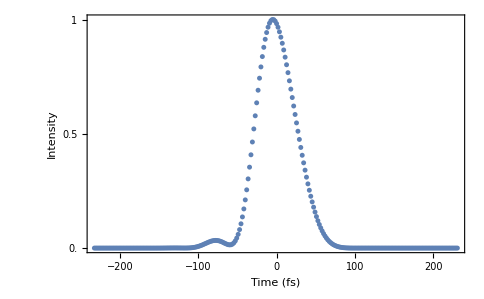

```mathematica
ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,2]]}],PlotRange->Full, Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Intensity",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {0.0,0.5,1}}]
```

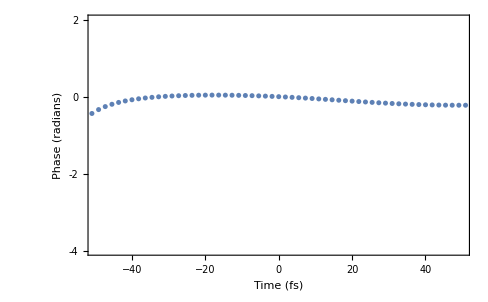

```mathematica
ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,3]]}],PlotRange->{{-50,50},{-4,2}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Phase (radians)",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {-4,-2,0,2}}]
```

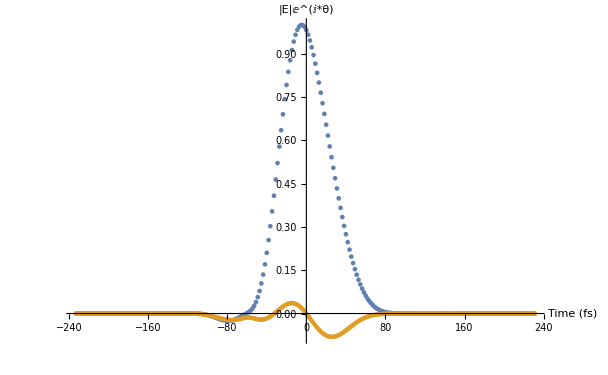

```mathematica
ListPlot[{Transpose[{gatedata[[All,1]],Re[gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]]}],Transpose[{gatedata[[All,1]],Im[gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","|E|ⅇ^(ⅈ*θ)"}]
```

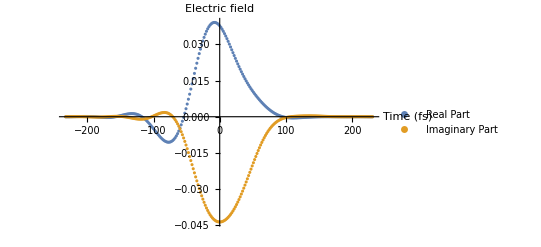

```mathematica
ListPlot[{Transpose[{gatedata[[All,1]],gatedata[[All,4]]}],Transpose[{gatedata[[All,1]],gatedata[[All,5]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","Electric field"},PlotLegends->{"Real Part","Imaginary Part"}]
```

```mathematica
gate1TimeDomain=gatedata[[All,1]];
```

```mathematica
gate1Efield=Interpolation[Transpose[{gate1TimeDomain,gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
N[gate1Efield[2.6]*Exp[ⅈ*ω0*2.6]]
```

0.941697-0.176535 ⅈ

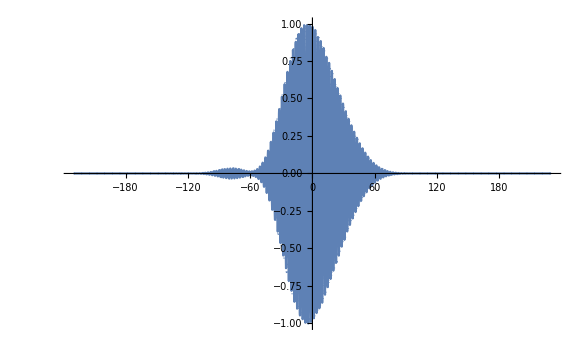

```mathematica
ReImPlot[gate1Efield[t]*Exp[ⅈ*ω0*t],{t,-230,230},PlotRange->Full]
```

```mathematica
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/gate_efield.csv",Range[-150,150,1]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/gate_efield.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/gate_efield.csv"],ParallelMap[gate1Efield[#]*Exp[ⅈ*ω0*#]&,Range[-150,150,1]]}]];
```

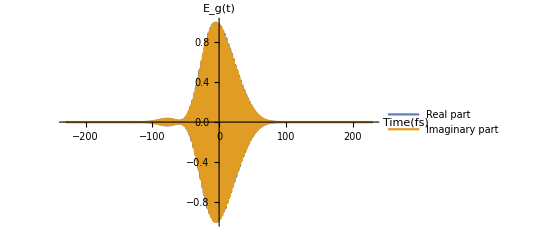

```mathematica
Plot[{Re[gate1Efield[t]*Exp[ⅈ*ω0*t]],Im[gate1Efield[t]*Exp[ⅈ*ω0*t]]},{t,-230,230},PlotRange->All,PlotLegends->{"Real part","Imaginary part"},AxesLabel->{"Time(fs)","E_g(t)"}]
```

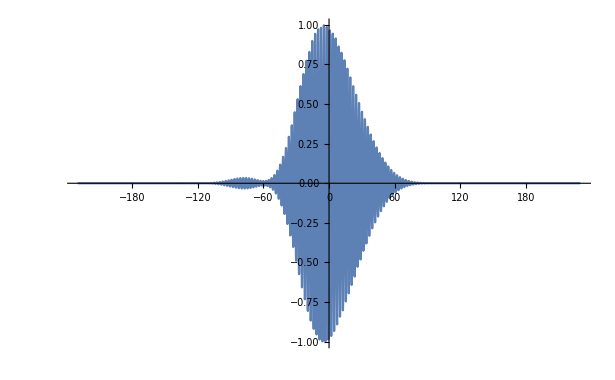

```mathematica
Plot[Im[gate1Efield[t]*Exp[ⅈ*ω0*t]],{t,-230,230},PlotRange->All]
```

```mathematica
(*gateAvector[t_]=Piecewise[{{0, t<Min[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^t gateEfield[x]ⅆx, Min[gateTimeDomain]<=t<=Max[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^Max[gateTimeDomain] gateEfield[x]ⅆx, t>Max[gateTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[gateAvector[t],{t,-330,300}]//AbsoluteTiming*)
```

```mathematica
(*,Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->10}*)
```

```mathematica
gate1Avector[t_]:=-NIntegrate[gate1Efield[x]*Exp[ⅈ*ω0*x],{x,Min[gate1TimeDomain],t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"}}]
```

```mathematica
gate1Avector[40]//AbsoluteTiming
```

{0.170368,0.0555645+0.106174 ⅈ}

```mathematica
(*timeRange=Join[Range[-200,-100,1],Range[-100,-50,0.5],Range[-50,50,0.1],Range[50,100,0.5],Range[100,200,1]];*)
```

```mathematica
gate1TimeRange=Range[Min[gate1TimeDomain],Max[gate1TimeDomain],0.1];
```

```mathematica
AbsoluteTiming[gate1Adata=ParallelMap[gate1Avector[#]&,gate1TimeRange];]
```

$Aborted

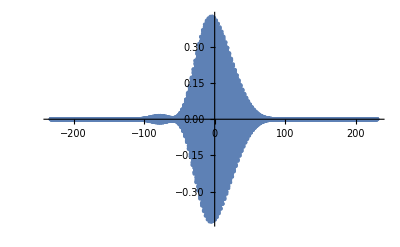

```mathematica
ListLinePlot[Transpose[{gate1TimeRange,Re[gate1Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

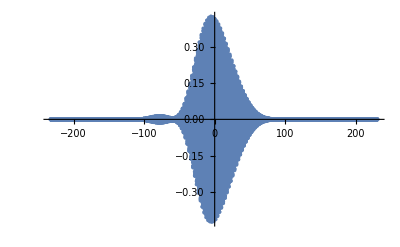

```mathematica
ListLinePlot[Transpose[{gate1TimeRange,Im[gate1Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

```mathematica
(*gateAreal=MapAt[Re,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*gateAimag=MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*ListPlot[{gateAreal,MapAt[Im,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
(*ListPlot[{gateAimag,MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
gate1Aenvelopdata=gate1Adata*Exp[-ⅈ*ω0*gate1TimeRange];
```

```mathematica
gate1Aenvelopdata[[100]]
```

-1.18286×10^-7-1.79791×10^-7 ⅈ

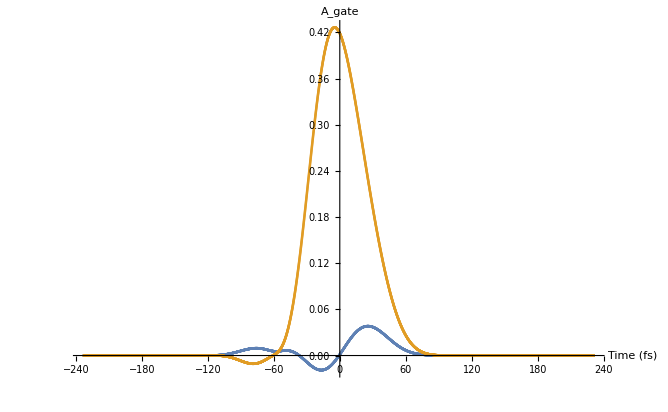

```mathematica
ListPlot[{Transpose[{gate1TimeRange,Re[gate1Aenvelopdata]}],Transpose[{gate1TimeRange,Im[gate1Aenvelopdata]}]},PlotRange->Full,AxesLabel->{"Time (fs)", "A_gate"}]
```

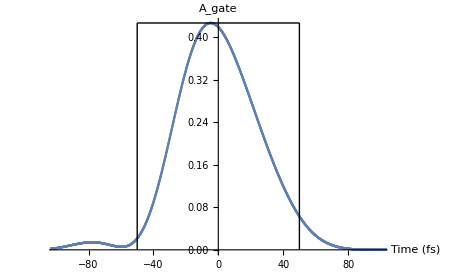

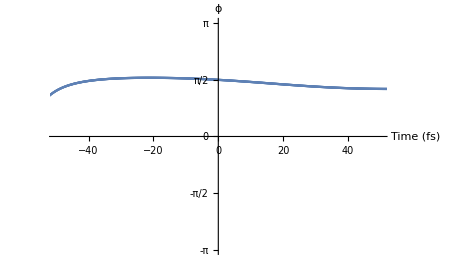

```mathematica
ListPlot[Transpose[{gate1TimeRange,Abs[gate1Aenvelopdata]}],AxesLabel->{"Time (fs)", "A_gate"},PlotRange->{{-100,100},Full},Epilog->{Line[{{-50,0},{-50,Max[Abs[gate1Aenvelopdata]]}}],Line[{{-50,Max[Abs[gate1Aenvelopdata]]},{50,Max[Abs[gate1Aenvelopdata]]}}],Line[{{50,0},{50,Max[Abs[gate1Aenvelopdata]]}}]}]
ListPlot[Transpose[{gate1TimeRange,Arg[gate1Aenvelopdata]}],AxesLabel->{"Time (fs)", "ϕ"},Ticks->{Automatic,π/2 Range[-2,2,1]},PlotRange->{{-50,50},Automatic}]
```

```mathematica
gate1Aenvelopfn=Interpolation[Transpose[{gate1TimeRange,gate1Aenvelopdata}]]
```

InterpolatingFunction[…]

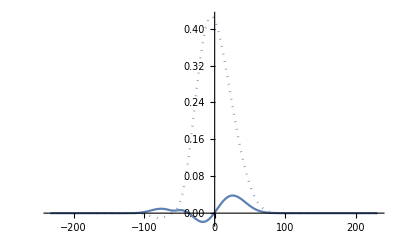

```mathematica
ReImPlot[gate1Aenvelopfn[x],{x,-232.85411740473393,230.94588259526608},PlotRange->Full]
```

```mathematica
gate1Afull[t_]:=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gate1Aenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
gate1Afull[10]
```

0.0223872+0.362602 ⅈ

## Gate 2 data (*Conjugate of Gate 1*)

```mathematica
(*gatedata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/Pulse Data/Gate_ETemporal.dat","Table"];*)
```

```mathematica
(*gatedata[[All,1]]*)
```

```mathematica
(*ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,2]]}],PlotRange->Full,AxesLabel->{"Time (fs)","Intensity"}]*)
```

```mathematica
(*ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,3]]}],PlotRange->Full,AxesLabel->{"Time (fs)","Phase (radians)"}]*)
```

```mathematica
(*ListPlot[{Transpose[{gatedata[[All,1]],Re[gatedata[[All,2]]*Exp[-ⅈ*gatedata[[All,3]]]]}],Transpose[{gatedata[[All,1]],Im[gatedata[[All,2]]*Exp[-ⅈ*gatedata[[All,3]]]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","|E|ⅇ^(ⅈ*θ)"}]*)
```

```mathematica
(*ListPlot[{Transpose[{gatedata[[All,1]],gatedata[[All,4]]}],Transpose[{gatedata[[All,1]],gatedata[[All,5]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","Electric field"},PlotLegends->{"Real Part","Imaginary Part"}]*)
```

```mathematica
(*gate2TimeDomain=gatedata[[All,1]];*)
```

```mathematica
(*gate2Efield=Interpolation[Transpose[{gate2TimeDomain,gatedata[[All,2]]*Exp[-ⅈ*gatedata[[All,3]]]}]]*)
```

```mathematica
(*ReImPlot[gate2Efield[t]*Exp[-ⅈ*ω0*t],{t,-230,230},PlotRange->Full]*)
```

```mathematica
(*gateAvector[t_]=Piecewise[{{0, t<Min[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^t gateEfield[x]ⅆx, Min[gateTimeDomain]<=t<=Max[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^Max[gateTimeDomain] gateEfield[x]ⅆx, t>Max[gateTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[gateAvector[t],{t,-330,300}]//AbsoluteTiming*)
```

```mathematica
(*gate2Avector[t_]:=-NIntegrate[gate2Efield[x]*Exp[-ⅈ*ω0*x],{x,Min[gate2TimeDomain],t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"}}]*)
```

```mathematica
(*gate2Avector[100]//AbsoluteTiming*)
```

```mathematica
(*timeRange=Join[Range[-200,-100,1],Range[-100,-50,0.5],Range[-50,50,0.1],Range[50,100,0.5],Range[100,200,1]];*)
```

```mathematica
(*gate2TimeRange=Range[Min[gate2TimeDomain],Max[gate2TimeDomain],0.1];*)
```

```mathematica
(*gate2Adata=ParallelMap[gate2Avector[#]&,gate2TimeRange];*)
```

```mathematica
(*ListLinePlot[Transpose[{gate2TimeRange,Re[gate2Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]*)
```

```mathematica
(*ListLinePlot[Transpose[{gate2TimeRange,Im[gate2Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]*)
```

```mathematica
(*gateAreal=MapAt[Re,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*gateAimag=MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*ListPlot[{gateAreal,MapAt[Im,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
(*ListPlot[{gateAimag,MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
(*gate2Aenvelopdata=gate2Adata*Exp[ⅈ*ω0*gate2TimeRange];*)
```

```mathematica
(*ListPlot[{Transpose[{gate2TimeRange,Re[gate2Aenvelopdata]}],Transpose[{gate2TimeRange,Im[gate2Aenvelopdata]}]},PlotRange->Full]*)
```

```mathematica
(*gate2Aenvelopfn=Interpolation[Transpose[{gate2TimeRange,gate2Aenvelopdata}]]*)
```

```mathematica
(*ReImPlot[gate2Aenvelopfn[x],{x,-232.85411740473393,230.94588259526608},PlotRange->Full]*)
```

```mathematica
(*gate2Afull[t_]:=Piecewise[{{0.0, t<Min[gate2TimeDomain]}, {gate2Aenvelopfn[t], Min[gate2TimeDomain]<=t<=Max[gate2TimeDomain]}, {0.0, t>Max[gate2TimeDomain]}}];*)
```

## Probe Data

```mathematica
probedata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/Pulse Data/Probe_ETemporal.dat","Table"];
```

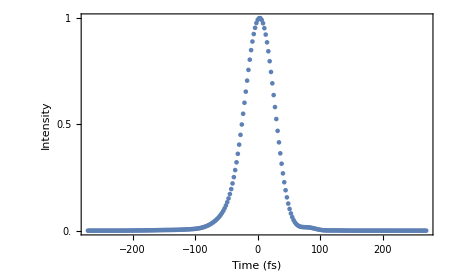

```mathematica
ListPlot[Transpose[{probedata[[All,1]],probedata[[All,2]]}],PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Intensity",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {0.0,0.5,1}}]
```

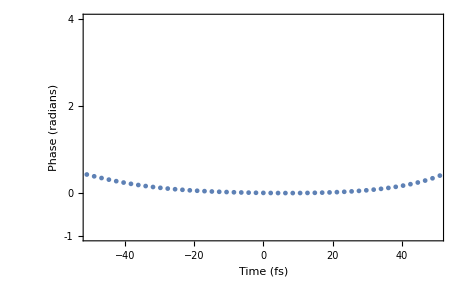

```mathematica
ListPlot[Transpose[{probedata[[All,1]],probedata[[All,3]]}],PlotRange->{{-50,50},{-1,4}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Phase (radians)",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {-1,0,2,4}}]
```

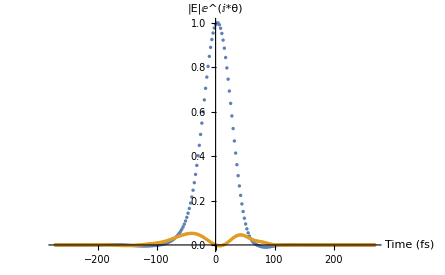

```mathematica
ListPlot[{Transpose[{probedata[[All,1]],Re[probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]]}],Transpose[{probedata[[All,1]],Im[probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","|E|ⅇ^(ⅈ*θ)"}]
```

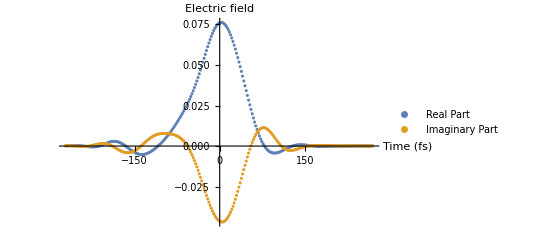

```mathematica
ListPlot[{Transpose[{probedata[[All,1]],probedata[[All,4]]}],Transpose[{probedata[[All,1]],probedata[[All,5]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","Electric field"},PlotLegends->{"Real Part","Imaginary Part"}]
```

```mathematica
probeTimeDomain=probedata[[All,1]];
```

```mathematica
probeEfield=Interpolation[Transpose[{probeTimeDomain,probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

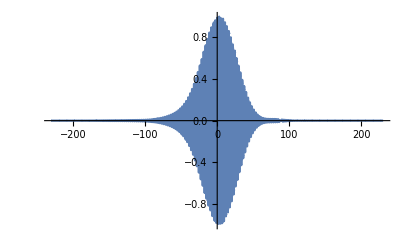

```mathematica
ReImPlot[probeEfield[t]*Exp[ⅈ*ω0*t],{t,-230,230},PlotRange->Full]
```

```mathematica
(*probeAvector[t_]=Piecewise[{{0, t<Min[probeTimeDomain]}, {-∫_Min[probeTimeDomain]^t probeEfield[x]ⅆx, Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {-∫_Min[probeTimeDomain]^Max[probeTimeDomain] probeEfield[x]ⅆx, t>Max[probeTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[probeAvector[t],{t,-300,300}]//AbsoluteTiming*)
```

```mathematica
probeAvector[t_]:=-NIntegrate[probeEfield[x]*Exp[ⅈ*ω0*x],{x,Min[probeTimeDomain],t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
probeAvector[100]//AbsoluteTiming
```

{0.209694,0.00123928+0.00110043 ⅈ}

```mathematica
probeTimeRange=Range[Min[probeTimeDomain],Max[probeTimeDomain],0.1];
```

```mathematica
probeAdata=ParallelMap[probeAvector[#]&,probeTimeRange];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

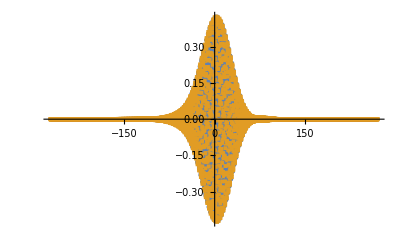

```mathematica
ListLinePlot[{Transpose[{probeTimeRange,Re[probeAdata]}],Transpose[{probeTimeRange,Im[probeAdata]}]},PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

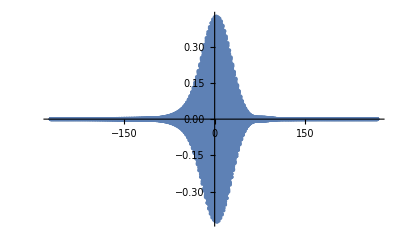

```mathematica
ListLinePlot[Transpose[{probeTimeRange,Im[probeAdata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

```mathematica
probeAenvelopdata=probeAdata*Exp[-ⅈ*ω0*probeTimeRange];
```

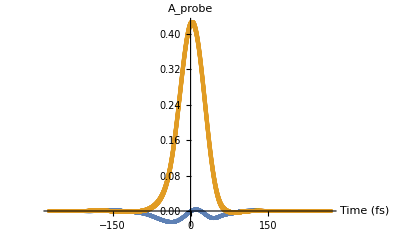

```mathematica
ListLinePlot[{Transpose[{probeTimeRange,Re[probeAenvelopdata]}],Transpose[{probeTimeRange,Im[probeAenvelopdata]}]},PlotMarkers->{Automatic,Tiny},PlotRange->Full, AxesLabel->{"Time (fs)","A_probe"}]
```

```mathematica
probeAenvelopfn=Interpolation[Transpose[{probeTimeRange,probeAenvelopdata}]]
```

InterpolatingFunction[…]

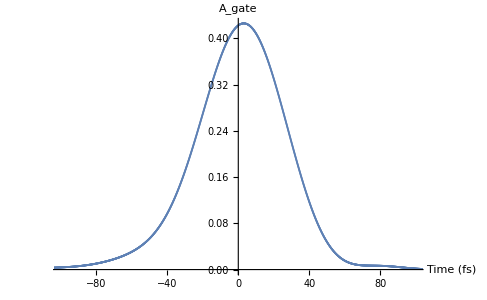

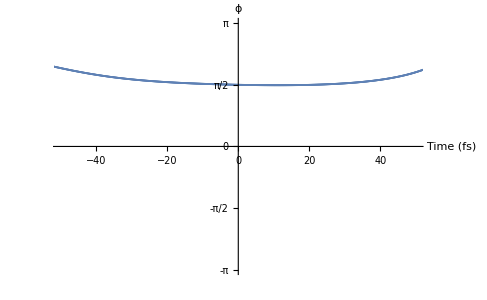

```mathematica
ListPlot[Transpose[{probeTimeRange,Abs[probeAenvelopdata]}],AxesLabel->{"Time (fs)", "A_gate"},PlotRange->{{-100,100},Full}]
ListPlot[Transpose[{probeTimeRange,Arg[probeAenvelopdata]}],AxesLabel->{"Time (fs)", "ϕ"},Ticks->{Automatic,π/2 Range[-2,2,1]},PlotRange->{{-50,50},Automatic}]
```

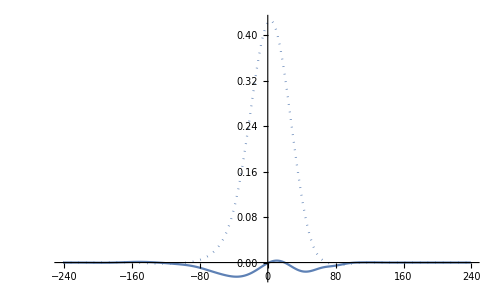

```mathematica
ReImPlot[probeAenvelopfn[x],{x,-241.25273991741625,239.34726008258377},PlotRange->Full]
```

```mathematica
probeAfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeAenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

```mathematica
probeAfull[231]//AbsoluteTiming
```

{0.00002,5.53043×10^-7-4.44303×10^-7 ⅈ}

```mathematica
probeAfull[230.94912098899835]
```

4.78745×10^-7-2.70602×10^-7 ⅈ

```mathematica
test[t_]:=Piecewise[{{0.0,t<Min[probeTimeDomain]},{probeAenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]},{0.0,t>Max[probeTimeDomain]}}]
```

```mathematica
test[10]
```

## Gaussian Electric Pulse

```mathematica
ω0=2.35;(*carrier wave frequency in rad/fs*)
```

```mathematica
EGaussian[t_]:=Block[{τ=25},Exp[-t^2/τ^2]](*The FWHM of gaussian envelop is 25fs*)
```

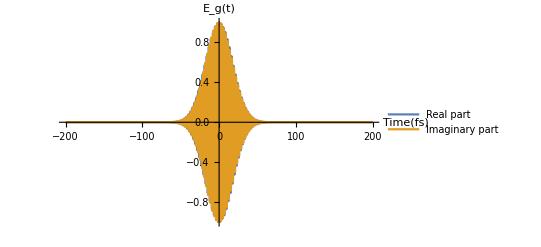

```mathematica
Plot[{Re[EGaussian[t]*Exp[ⅈ*ω0*t]],Im[EGaussian[t]*Exp[ⅈ*ω0*t]]},{t,-200,200},PlotRange->All,PlotLegends->{"Real part","Imaginary part"},AxesLabel->{"Time(fs)","E_g(t)"}]
```

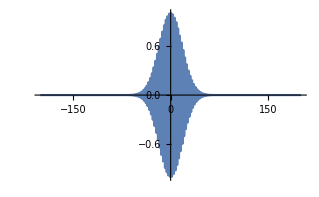

```mathematica
Plot[Im[EGaussian[t]*Exp[ⅈ*ω0*t]],{t,-200,200},PlotRange->All]
```

```mathematica
(*gateAvector[t_]=Piecewise[{{0, t<Min[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^t gateEfield[x]ⅆx, Min[gateTimeDomain]<=t<=Max[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^Max[gateTimeDomain] gateEfield[x]ⅆx, t>Max[gateTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[gateAvector[t],{t,-330,300}]//AbsoluteTiming*)
```

```mathematica
(*,Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->10}*)
```

```mathematica
Avector[t_]:=-NIntegrate[EGaussian[x]*Exp[ⅈ*ω0*x],{x,-200,t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"}}]
```

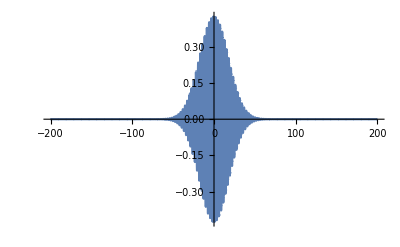

```mathematica
ReImPlot[Avector[t],{t,-200,200},PlotRange->Full]
```

```mathematica
(*timeRange=Join[Range[-200,-100,1],Range[-100,-50,0.5],Range[-50,50,0.1],Range[50,100,0.5],Range[100,200,1]];*)
```

```mathematica
TimeRange=Range[-200,200,0.1];
```

```mathematica
AbsoluteTiming[Adata=ParallelMap[Avector[#]&,TimeRange];]
```

{3.56704,Null}

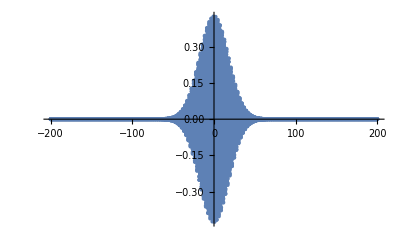

```mathematica
ListLinePlot[Transpose[{TimeRange,Re[Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

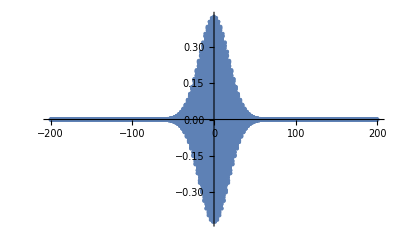

```mathematica
ListLinePlot[Transpose[{TimeRange,Im[Adata]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

```mathematica
(*gateAreal=MapAt[Re,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*gateAimag=MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*ListPlot[{gateAreal,MapAt[Im,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
(*ListPlot[{gateAimag,MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
Aenvelopdata=Adata*Exp[-ⅈ*ω0*TimeRange];
```

```mathematica
Aenvelopdata[[100]]
```

-7.94662×10^-27+3.09153×10^-26 ⅈ

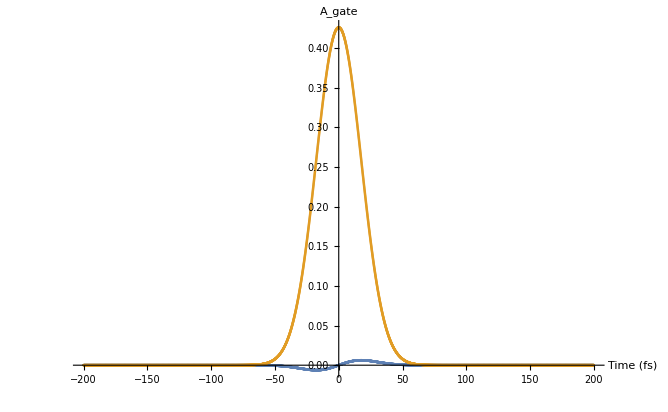

```mathematica
ListPlot[{Transpose[{TimeRange,Re[Aenvelopdata]}],Transpose[{TimeRange,Im[Aenvelopdata]}]},PlotRange->Full,AxesLabel->{"Time (fs)", "A_gate"}]
```

```mathematica
Aenvelopfn=Interpolation[Transpose[{TimeRange,Aenvelopdata}]]
```

InterpolatingFunction[…]

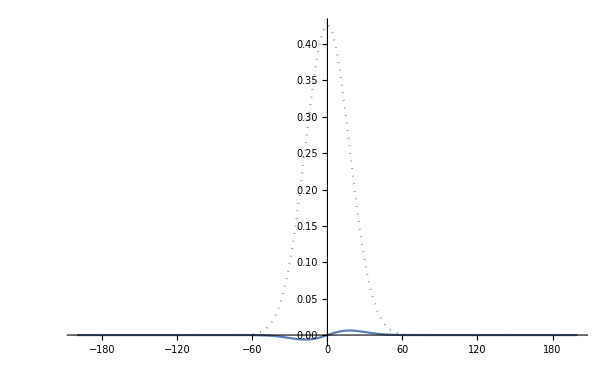

```mathematica
ReImPlot[Aenvelopfn[x],{x,-200,200},PlotRange->Full]
```

```mathematica
Afull[t_]:=Piecewise[{{0.0, t<-200}, {Aenvelopfn[t], -200<=t<=200}, {0.0, t>200}}];
```

## Electric fields

```mathematica
gateEenvelopfn=Interpolation[Transpose[{gatedata[[All,1]],gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
gateEfull[t_]=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gateEenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

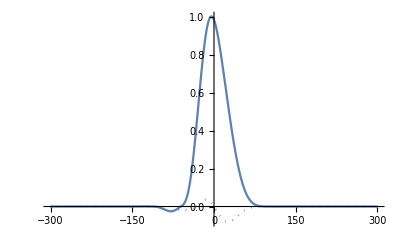

```mathematica
ReImPlot[gateEfull[t],{t,-300,300},PlotRange->All]
```

```mathematica
probeEenvelopfn=Interpolation[Transpose[{probedata[[All,1]],probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
probeEfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeEenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

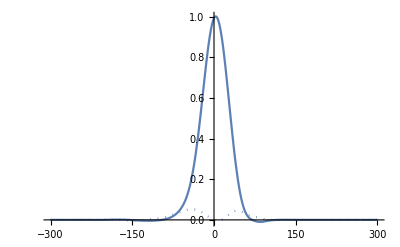

```mathematica
ReImPlot[probeEfull[t],{t,-300,300},PlotRange->All]
```

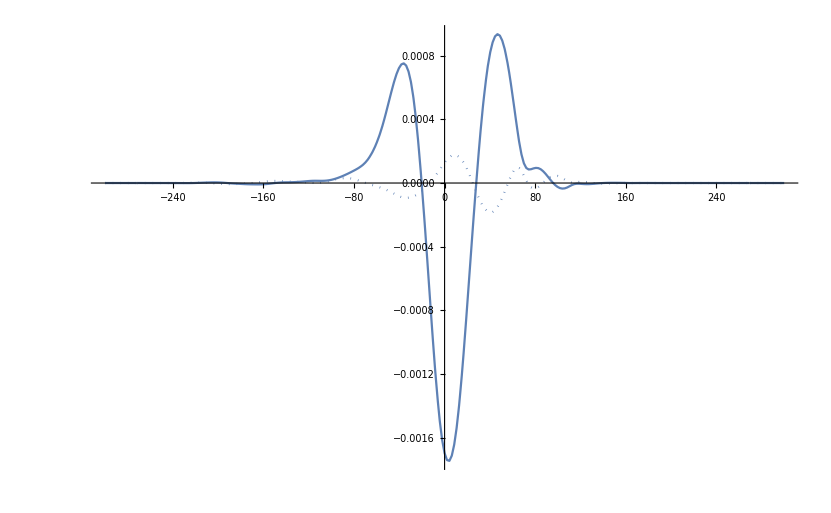

```mathematica
ReImPlot[probeEfull''[t],{t,-300,300},PlotRange->All]
```

# Kubo Formula

## Time delay = 0

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of ZnO in fs^-1*)*)
Ω=7.77/ℏ
```

11.8085

## Term 1

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.087623,-0.000110798-0.0295871 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{64.7225,Null}

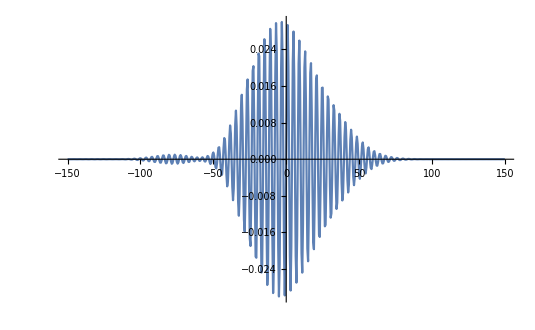

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

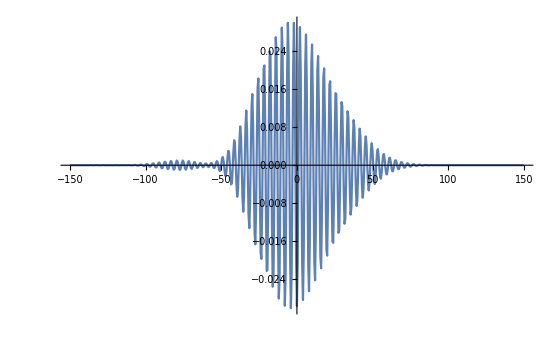

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

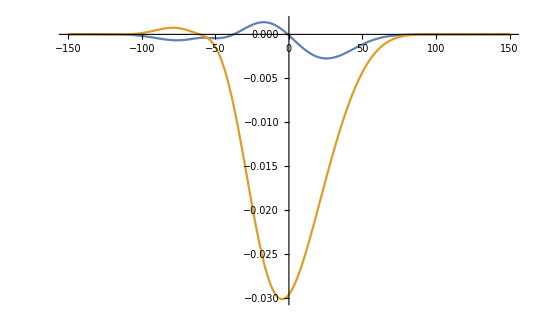

```mathematica
ListLinePlot[{Transpose[{timeRange,Re[dataint1*Exp[-ⅈ*(Ω+ω0)*timeRange]]}],Transpose[{timeRange,Im[dataint1*Exp[-ⅈ*(Ω+ω0)*timeRange]]}]},PlotRange->Full]
```

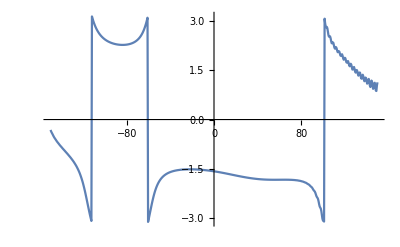

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[dataint1*Exp[-ⅈ*(Ω+ω0)*timeRange]]}],PlotRange->Full]
```

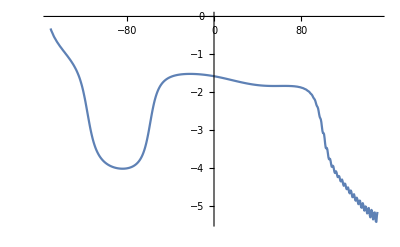

```mathematica
ListLinePlot[Transpose[{timeRange,ResourceFunction["PhaseUnwrap"][Arg[dataint1*Exp[-ⅈ*(Ω+ω0)*timeRange]]]}],PlotRange->Full]
```

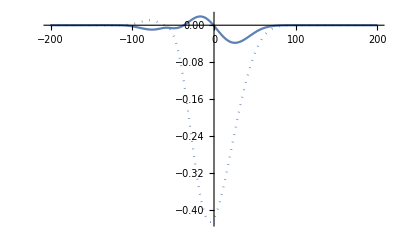

```mathematica
ReImPlot[-gate1Afull[x],{x,-200,200},PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.0038449+0.0253813 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.458047,-0.000695688+0.000564456 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{144.261,Null}

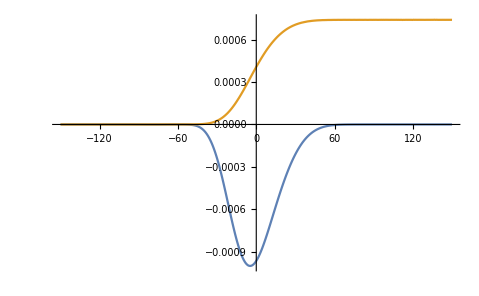

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

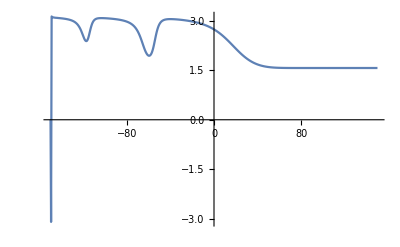

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[dataint2]}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{151.911,Null}

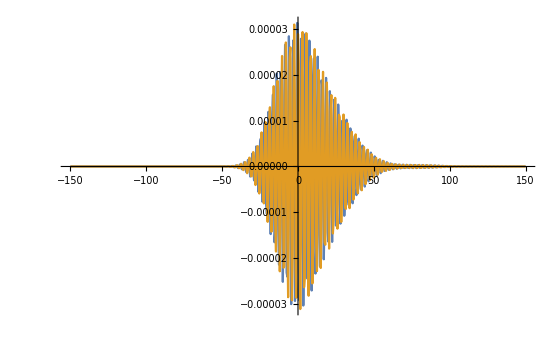

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

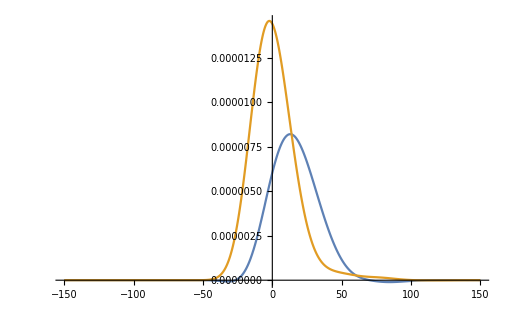

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

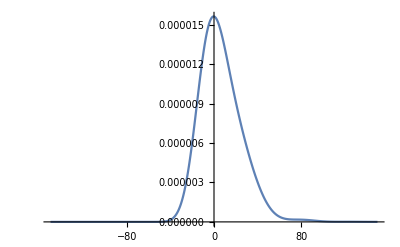

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

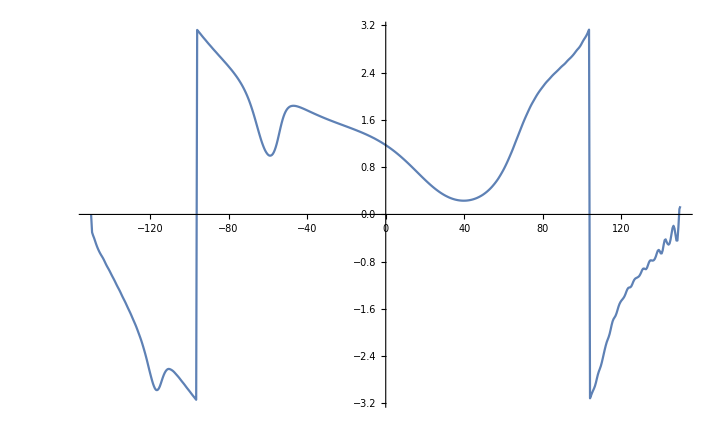

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

## Term 2

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.038786,-0.000106859+0.0442505 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{64.8274,Null}

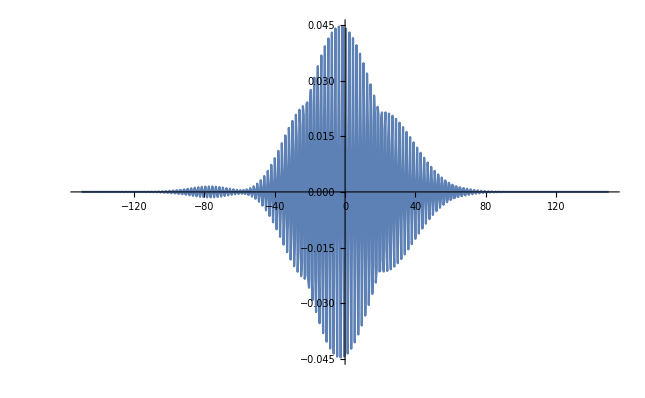

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

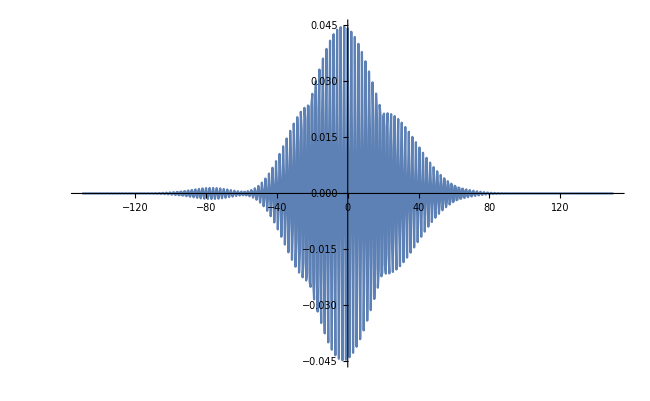

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.342149,-0.00132538+0.0230394 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{112.094,Null}

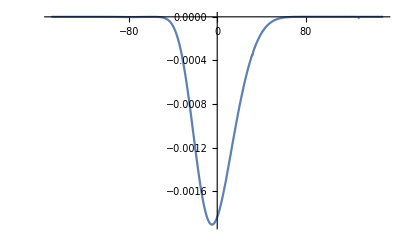

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

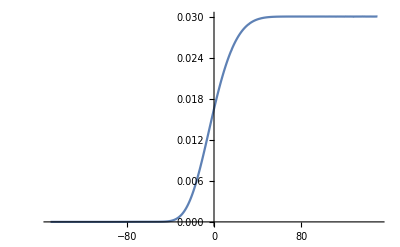

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{122.8,Null}

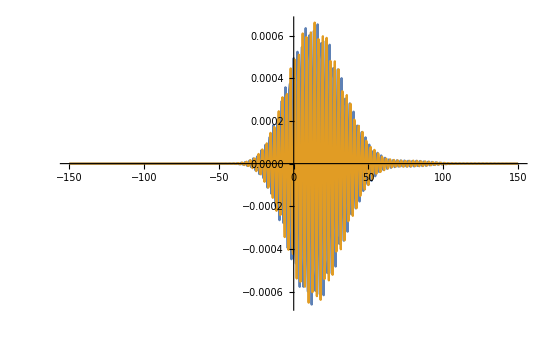

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term2envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

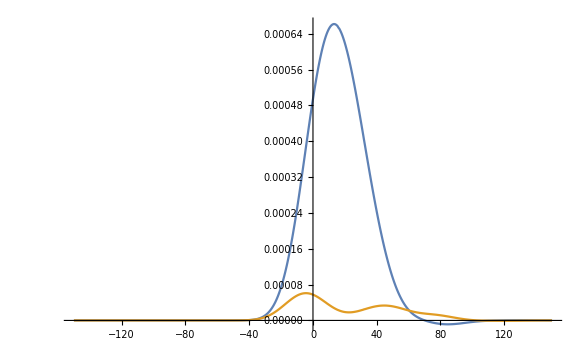

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

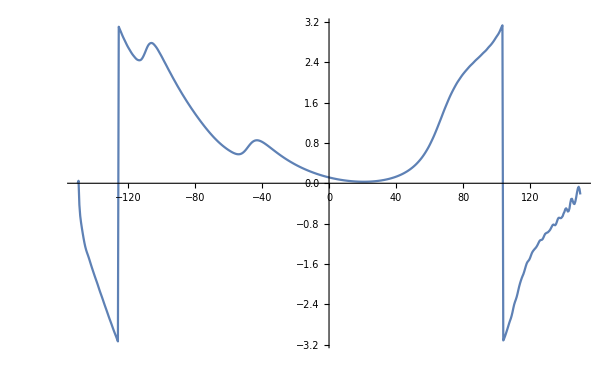

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

## Term 3

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.052125,0.0000803043-0.0298522 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{21.9298,Null}

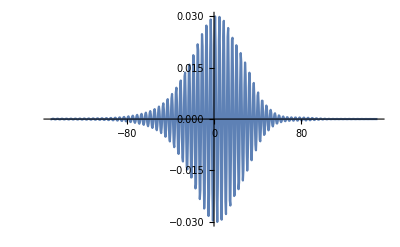

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

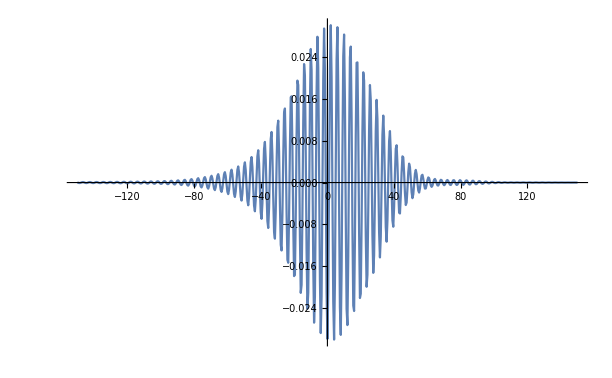

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.396499,1.53063×10^-7+1.33837×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{109.554,Null}

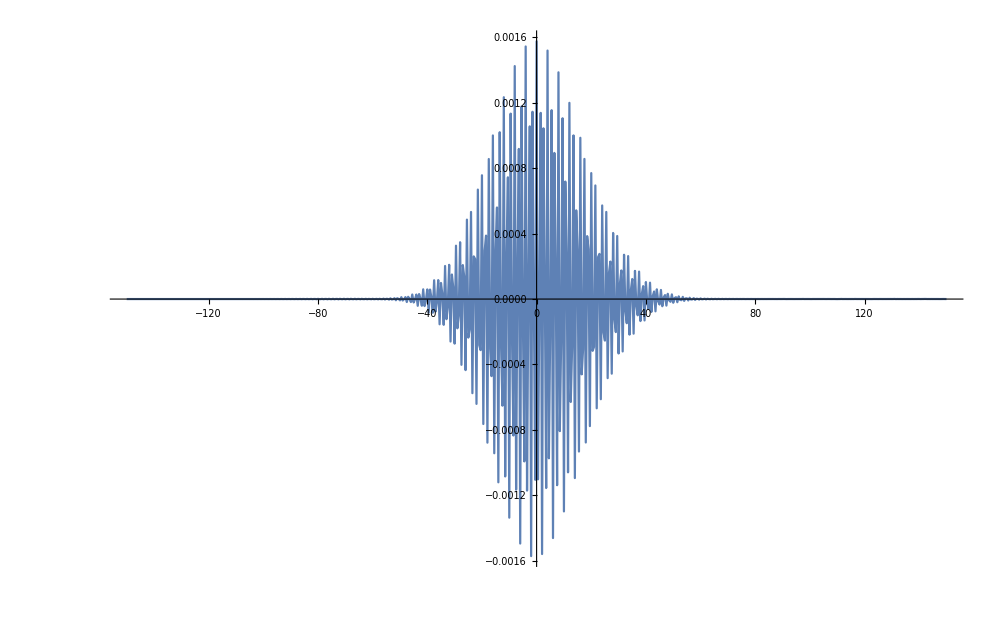

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

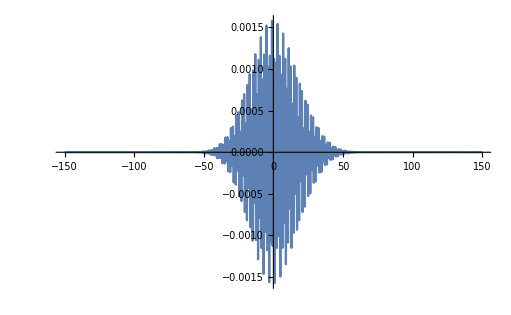

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{109.373,Null}

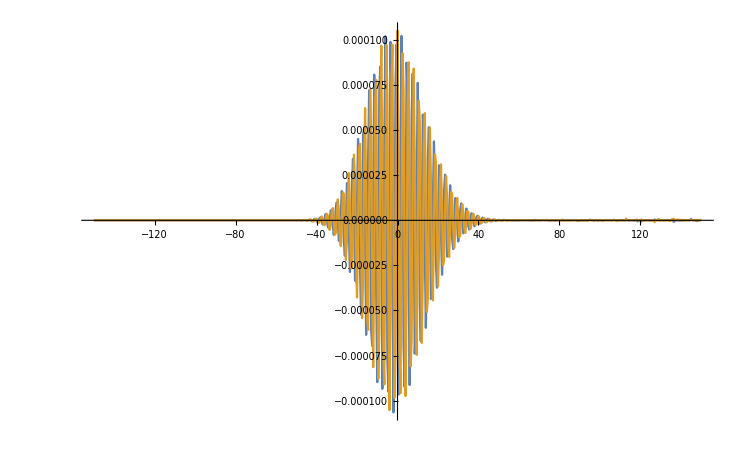

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

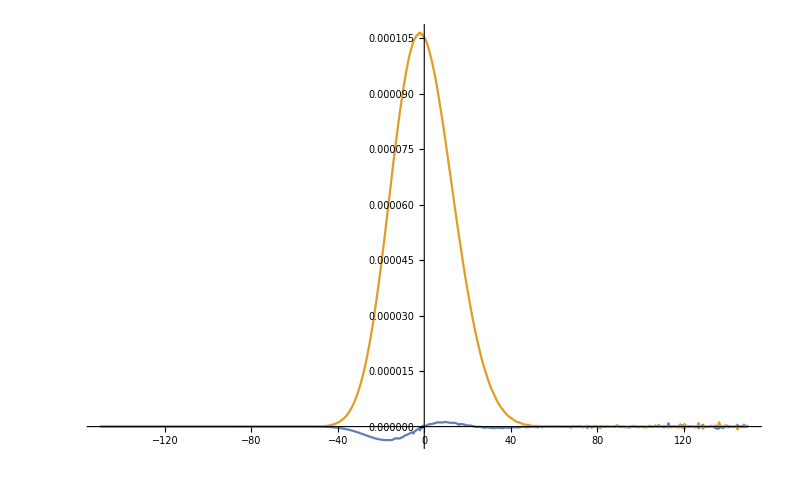

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

## Term 4

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.051278,0.0000803043-0.0298522 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{21.8976,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.511445,-0.0000378061+0.000719592 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{119.399,Null}

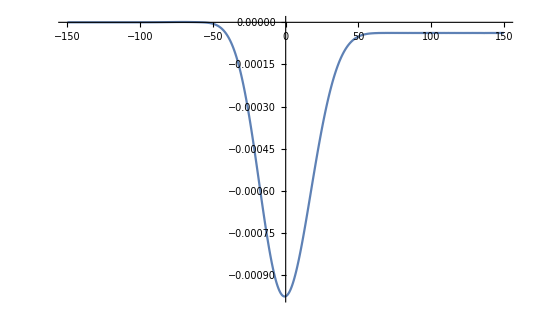

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

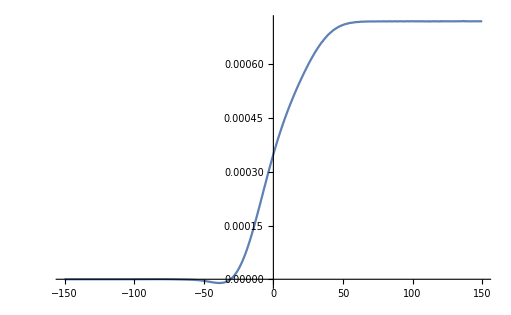

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{104.935,Null}

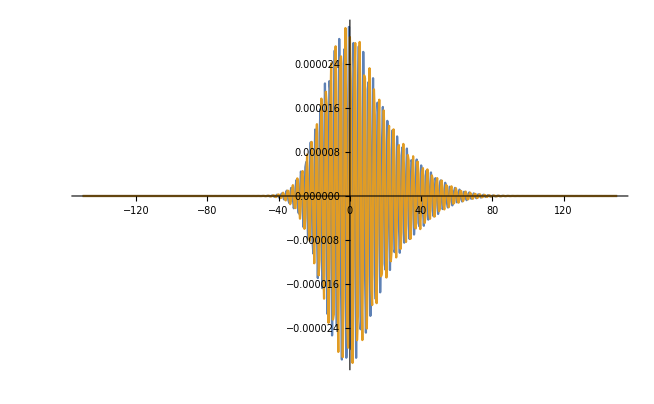

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

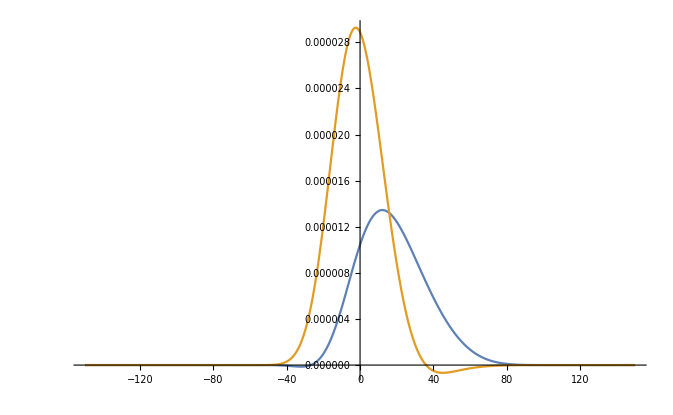

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

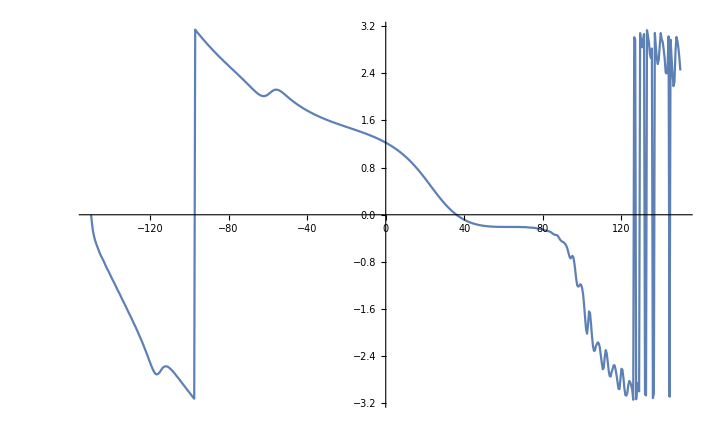

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

## Term 5

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.041745,-0.000110798-0.0295871 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{65.3264,Null}

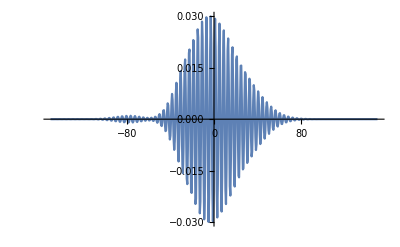

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

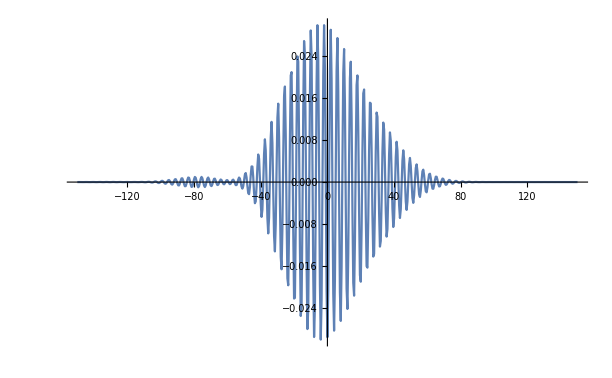

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.388016,1.58537×10^-7+1.42357×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{128.923,Null}

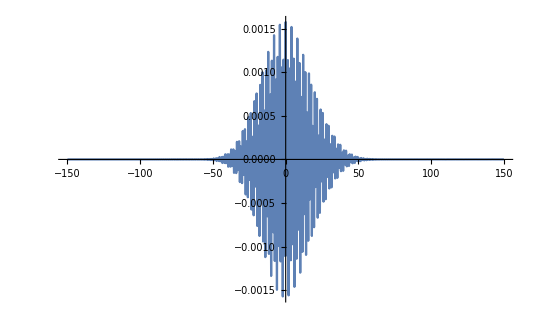

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

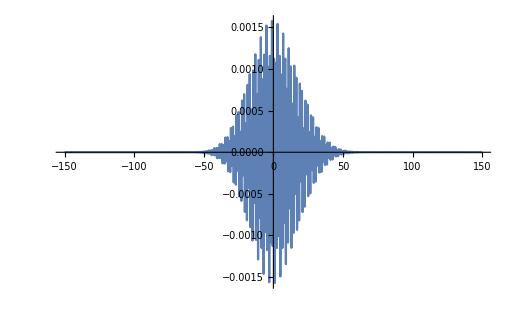

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{109.425,Null}

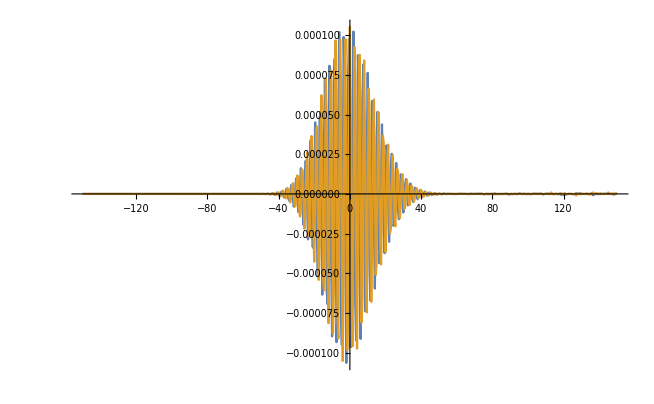

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

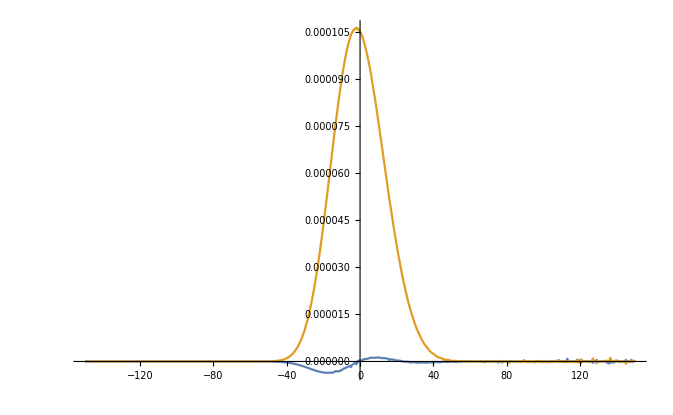

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

## Term 6

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.037111,-0.000106859+0.0442505 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{65.2785,Null}

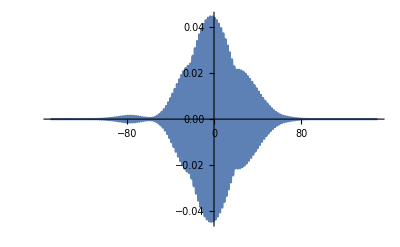

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

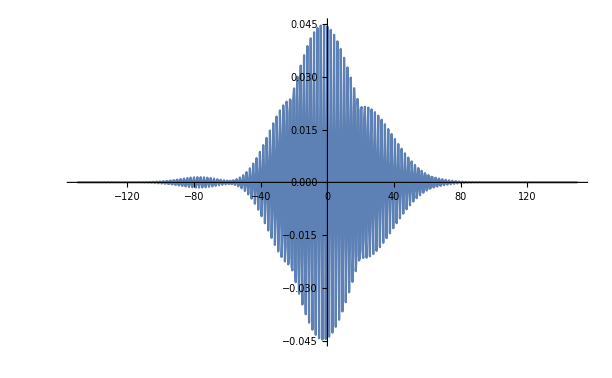

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.452224,-0.00160717+0.0293398 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{135.368,Null}

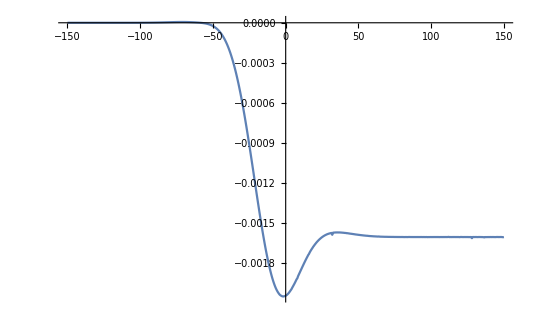

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

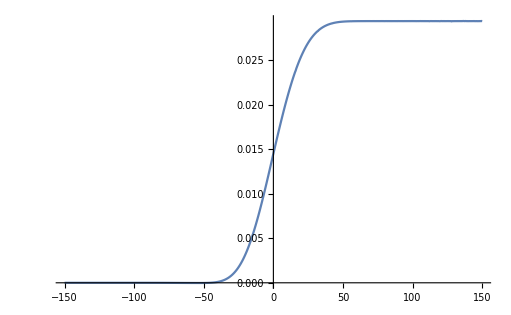

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{100.959,Null}

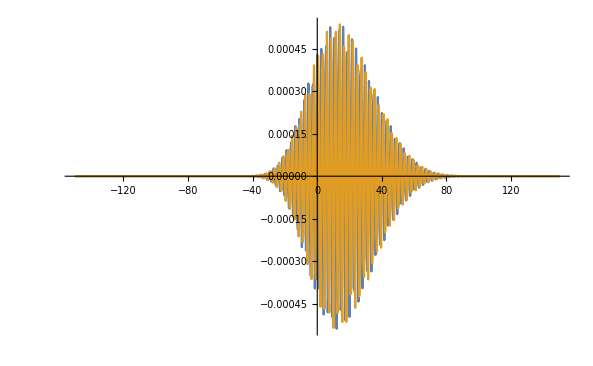

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

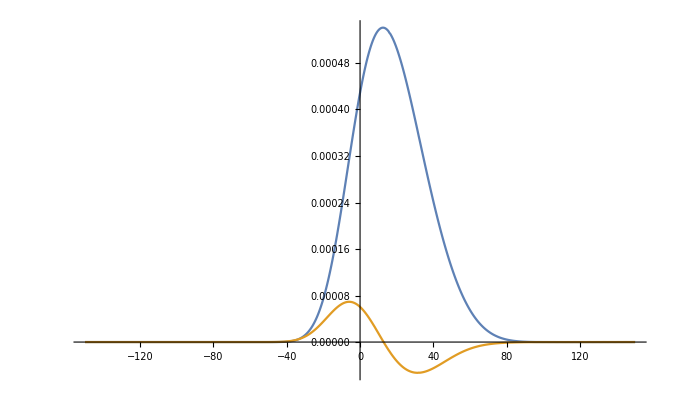

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

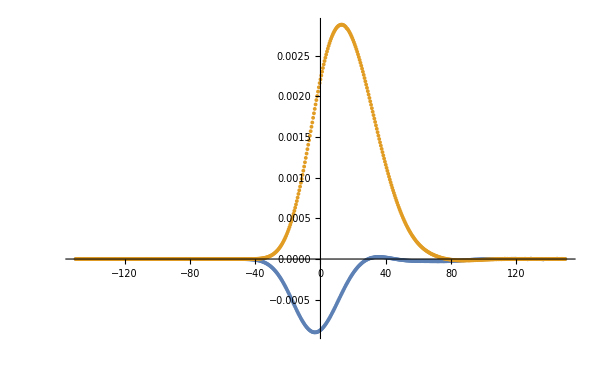

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

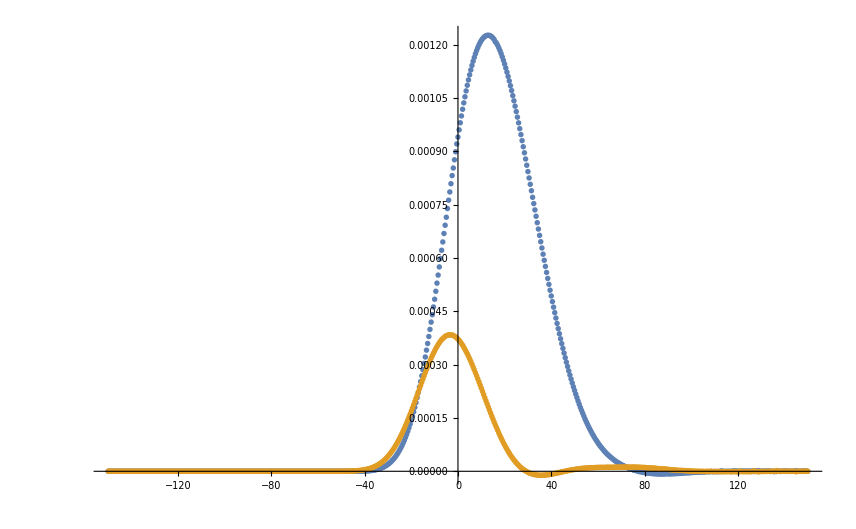

```mathematica
ListPlot[{Transpose[{timeRange,Re@totalenvelop}],Transpose[{timeRange,Im@totalenvelop}]},PlotRange->Full]
```

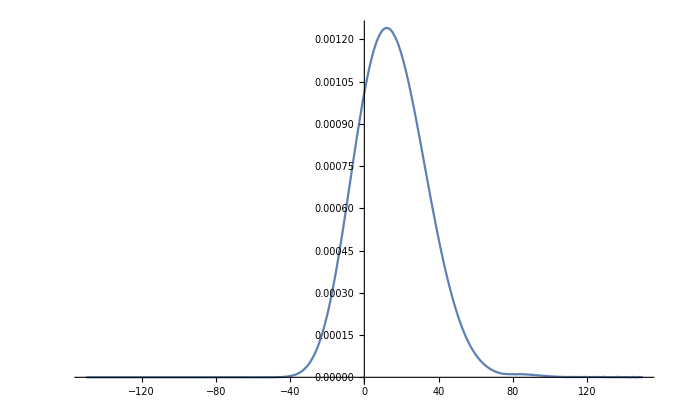

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

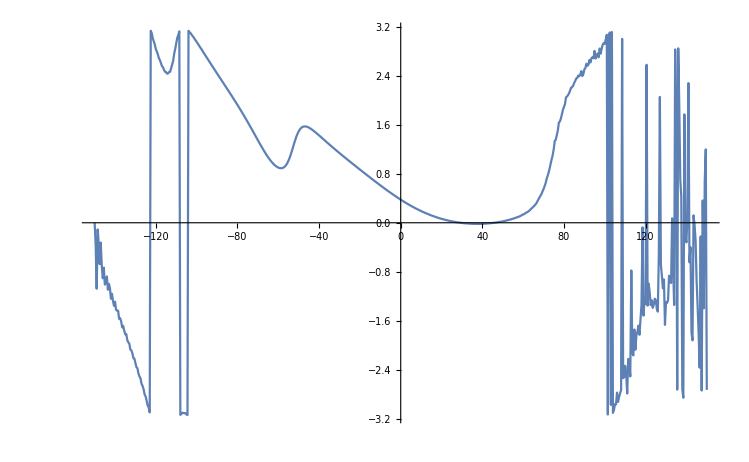

```mathematica
ListLinePlot[Transpose[{timeRange,Arg@totalenvelop}],PlotRange->Full]
```

```mathematica
N@ArcTan[-10^7]
```

-1.5708

## Time delay = τ

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
Ω=7.77/ℏ(*The band gap/ℏ of MgO in fs^-1*)
```

11.8085

## Term 1

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.042385,-0.000110798-0.0295871 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{64.9418,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.0038449+0.0253813 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.466408,-0.000695688+0.000564456 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{121.425,Null}

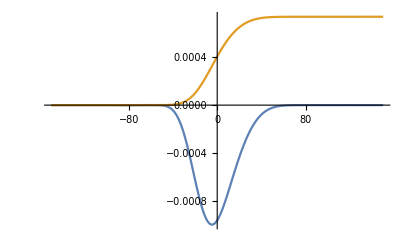

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{122.22,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

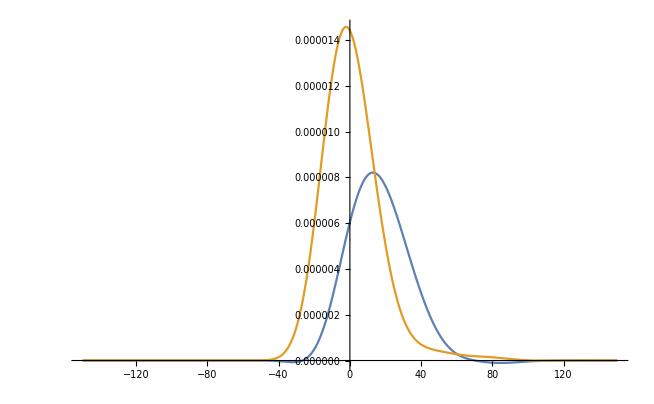

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.040133,-0.000106859+0.0442505 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t1 near {t1} = {-14.553382337795870394736530698355661959968113322199067401345315191}. NIntegrate obtained 0.00109124+0.0225103 ⅈ and 3.44126×10^-12 for the integral and error estimates.

{64.8151,Null}

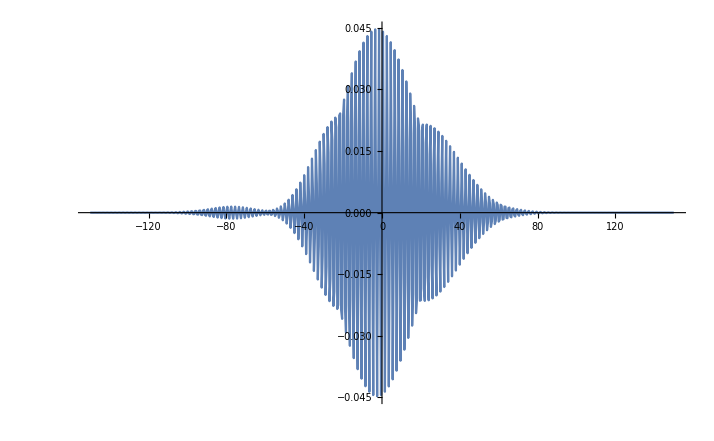

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

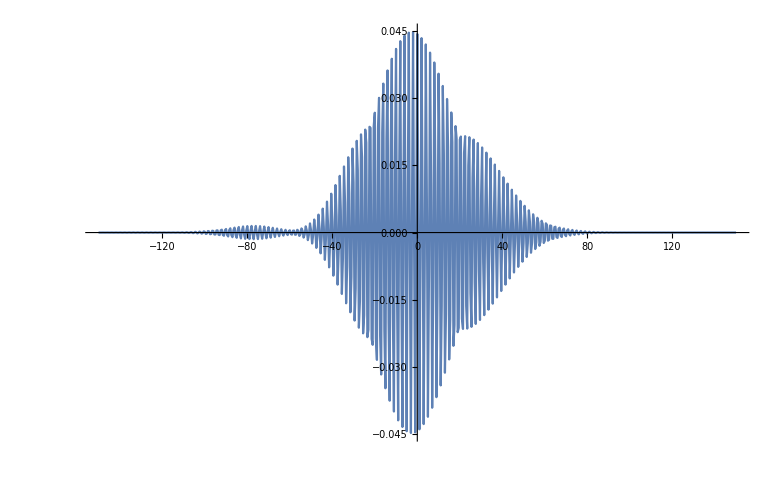

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.348163,-0.00132538+0.0230394 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{113.32,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{124.214,Null}

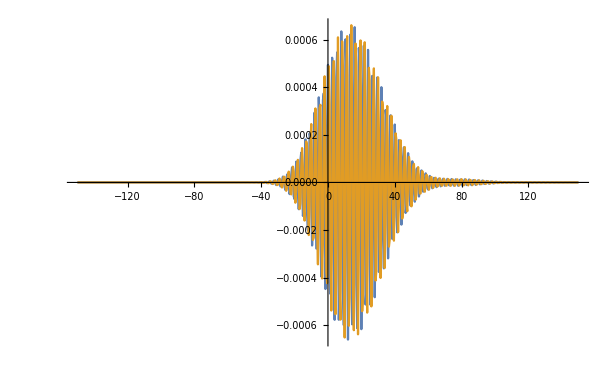

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

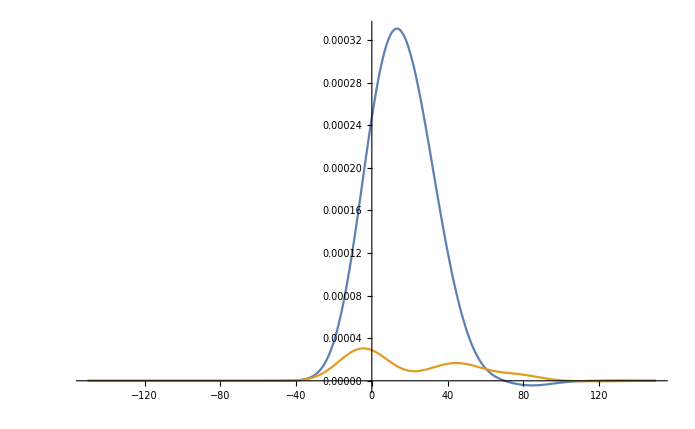

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

## Term 3

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1-τ]*Exp[ⅈ*Ω*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.055021,0.0000803043-0.0298522 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.283,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.407444,1.53063×10^-7+1.33837×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{109.612,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{109.363,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

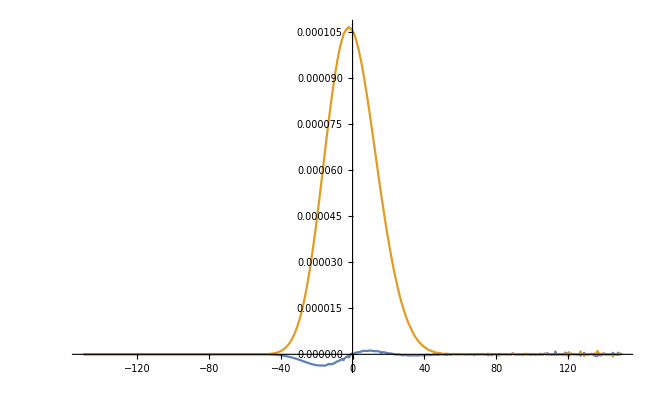

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

## Term 4

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1-τ]*Exp[ⅈ*Ω*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.053353,0.0000803043-0.0298522 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.2615,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.530245,-0.0000378061+0.000719592 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{119.918,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{104.692,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.042927,-0.000110798-0.0295871 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{66.4427,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.413066,1.58537×10^-7+1.42357×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{134.263,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{111.022,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-150,150,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.041378,-0.000106859+0.0442505 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{67.0561,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.468313,-0.00160717+0.0293398 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{135.483,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{100.443,Null}

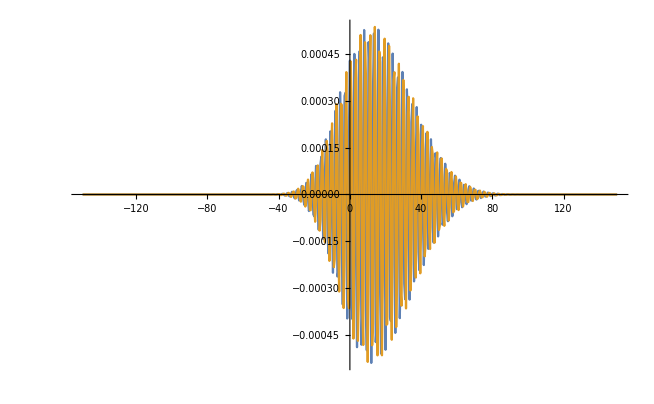

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

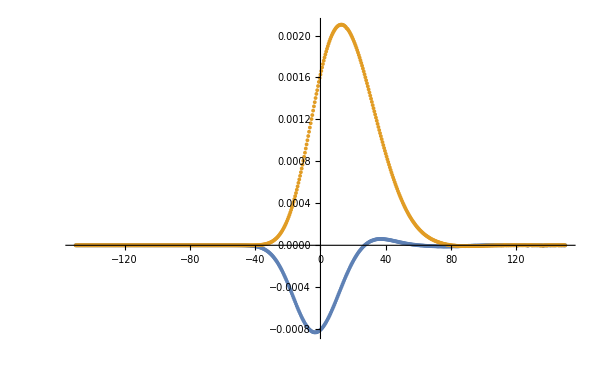

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

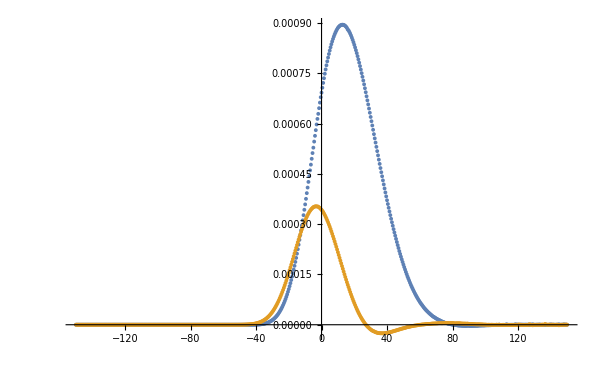

```mathematica
ListPlot[{Transpose[{timeRange,Re@totalenvelop}],Transpose[{timeRange,Im@totalenvelop}]},PlotRange->Full]
```

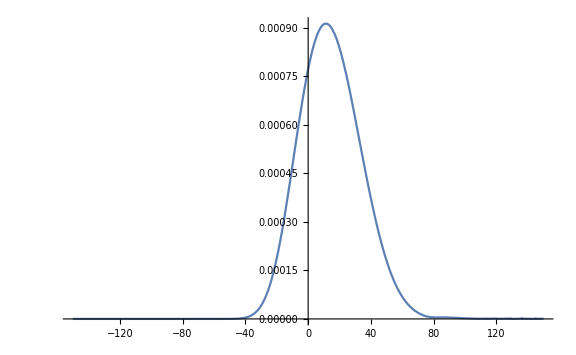

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

```mathematica
Total[Abs@totalenvelop]
```

0.0900871

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
testData=ToExpression[Import["/Users/shashank/Desktop/datafile.csv","CSV"]];
```

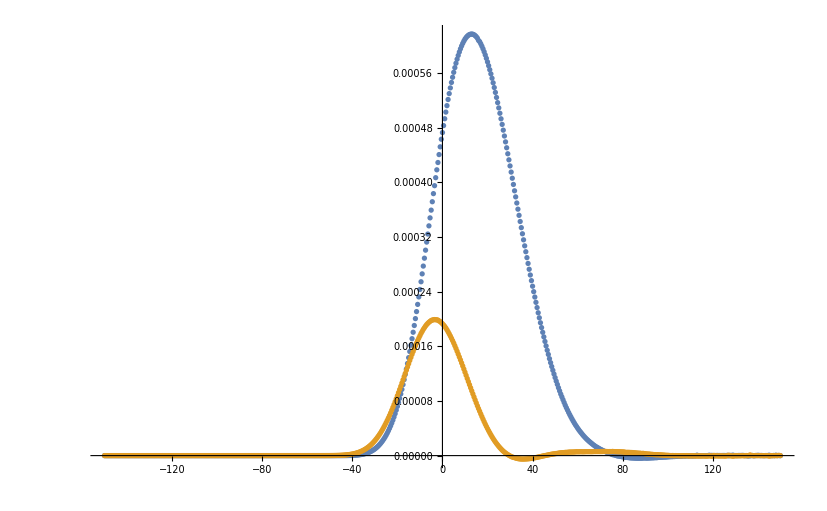

```mathematica
ListPlot[{Transpose[{testData[[All,1]],Re[testData[[All,2]]]}],Transpose[{testData[[All,1]],Im[testData[[All,2]]]}]},PlotRange->All]
```

## Time dependent integration

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
Ω=3.37/ℏ(*The band gap/ℏ of ZnO in fs^-1*)
```

5.12158

```mathematica
th[t_,t1_,t2_,t3_]:=gate1Afull[t1]*gate2Afull[t2]*probeAfull[t3]*Exp[ⅈ*(Ω*t+Ω*t1-Ω*t+Ω*t + ω0*(t1-t2+t3))]
```

```mathematica
th[1,1,1,1]//AbsoluteTiming
```

{0.000072,(-0.176281-0.0033512 ⅈ) gate2Afull[1]}

```mathematica
int[t_]:=NIntegrate[gate1Afull[t1]*gate2Afull[t2]*probeAfull[t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->"LocalAdaptive"]
```

```mathematica
int[0]//AbsoluteTiming
```

NIntegrate::inumr: The integrand gate2Afull[t2] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,937300222/4056963},{0,1},{0,345059/1280}}.

{0.073461,NIntegrate[gate1Afull[t1] gate2Afull[t2] probeAfull[t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→LocalAdaptive]}

```mathematica
NIntegrate[Cos[(Ω*(t1+t2+t3)+(-Ω)*(t1)+Ω*(t1+t2))+ω0*(-t3-t1)],{t1,0,100},{t2,0,100},{t3,0,100}]
```

0.000664609

```mathematica
testint[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*(Ω*(t1+t2+t3)+(-Ω)*(t1)+Ω*(t1+t2))+ⅈ*ω0*(-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
test2int[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*(Ω-ω0)*t1]*Exp[ⅈ*(Ω)*2*t2]*Exp[ⅈ*(Ω-ω0)*t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
test3int[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*((Ω-ω0)*t1+(Ω)*2*t2+(Ω-ω0)*t3)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
testint[0]//AbsoluteTiming
```

NIntegrate::inumrexpr: Expression {(5270347210 (5270347210-5270347210 t1) (5270347210-5270347210 t1+(-5270347210+5270347210 t1) t2) gate2Afull[-((5270347210-5270347210 t1) t2)/22633687-((5270347210-5270347210 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (5270347210 ⅇ^((9611532206877 ⅈ t1)/14892966046+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) (5270347210-5270347210 t1) («1») gate2Afull[-((5270347210-«1») t2)/22633687-((«1»)«1»«2»)/22633687] «1» «1»[-(5270347210 t1)/22633687-((5270347210-5270347210 t1) t2)/22633687-((5270347210-5270347210 t1-(5270347210+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-t2-t3] ({ | «1») (Piecewise[{{0., -t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},{5,15,0,{5413},{4},0,0,0,0,Automatic,«3»},{{-271.7,-271.6,-271.5,-271.4,-271.3,-271.2,-271.1,-271.,-270.9,-270.8,«5403»}},«1»,{Automatic}][-t3], -271.7≤-t3≤269.577}, {0., -t3>269.577}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(5270347210 (5270347210-5270347210 t1) (5270347210-5270347210 t1+(-5270347210+5270347210 t1) t2) gate2Afull[-((5270347210-5270347210 t1) t2)/22633687-((5270347210-5270347210 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (5270347210 ⅇ^((9611532206877 ⅈ t1)/14892966046+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) (5270347210-5270347210 t1) («1») gate2Afull[-((5270347210-«1») t2)/22633687-((«1»)«1»«2»)/22633687] «1» «1»[-(5270347210 t1)/22633687-((5270347210-5270347210 t1) t2)/22633687-((5270347210-5270347210 t1-(5270347210+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-t2-t3] ({ | «1») (Piecewise[{{0., -t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},{5,15,0,{5413},{4},0,0,0,0,Automatic,«3»},{{-271.7,-271.6,-271.5,-271.4,-271.3,-271.2,-271.1,-271.,-270.9,-270.8,«5403»}},«1»,{Automatic}][-t3], -271.7≤-t3≤269.577}, {0., -t3>269.577}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

{0.134971,NIntegrate[gate1Afull[0-t3-t2-t1] gate2Afull[0-t3-t2] probeAfull[0-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}]}

```mathematica
test2int[-14]//AbsoluteTiming
```

NIntegrate::inumrexpr: Expression {(4953475592 (4953475592-4953475592 t1) (4953475592-4953475592 t1+(-4953475592+4953475592 t1) t2) gate2Afull[-14-((4953475592-4953475592 t1) t2)/22633687-((4953475592-4953475592 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (4953475592 ⅇ^((22584133592826 ⅈ t1)/37232415115+(«1»)/(7«7»23)+(18237 ⅈ («1») t3)/148929660460) «3» «1»[-14-((«1») t3)/22633687] «1»[-14-(4953475592 t1)/22633687-((4953475592-4953475592 t1) t2)/22633687-((4953475592-4953475592 t1-(4953475592+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.77158 ⅈ) t1+(0.+10.2432 ⅈ) t2+(0.+2.77158 ⅈ) t3) gate2Afull[-14-t2-t3] (Piecewise[{{0., -14-t3<-271.7}, {«1»[-14-t3], -271.7≤-14-t3≤269.577}, {0., -14-t3>269.577}, {0, True}}]) (Piecewise[{{0., -14-t1-t2-t3<-232.854}, {«1», -232.854≤-14-t1-t2-t3≤231.035}, {0., -14-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(4953475592 (4953475592-4953475592 t1) (4953475592-4953475592 t1+(-4953475592+4953475592 t1) t2) gate2Afull[-14-((4953475592-4953475592 t1) t2)/22633687-((4953475592-4953475592 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (4953475592 ⅇ^((22584133592826 ⅈ t1)/37232415115+(«1»)/(7«7»23)+(18237 ⅈ («1») t3)/148929660460) «3» «1»[-14-((«1») t3)/22633687] «1»[-14-(4953475592 t1)/22633687-((4953475592-4953475592 t1) t2)/22633687-((4953475592-4953475592 t1-(4953475592+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.77158 ⅈ) t1+(0.+10.2432 ⅈ) t2+(0.+2.77158 ⅈ) t3) gate2Afull[-14-t2-t3] (Piecewise[{{0., -14-t3<-271.7}, {«1»[-14-t3], -271.7≤-14-t3≤269.577}, {0., -14-t3>269.577}, {0, True}}]) (Piecewise[{{0., -14-t1-t2-t3<-232.854}, {«1», -232.854≤-14-t1-t2-t3≤231.035}, {0., -14-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

{0.057893,NIntegrate[gate1Afull[-14-t3-t2-t1] gate2Afull[-14-t3-t2] probeAfull[-14-t3] Exp[ⅈ (Ω-ω0) t1] Exp[ⅈ Ω 2 t2] Exp[ⅈ (Ω-ω0) t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}]}

```mathematica
test3int[10]//AbsoluteTiming
```

NIntegrate::inumrexpr: Expression {(5496684080 (5496684080-5496684080 t1) (5496684080-5496684080 t1+(-5496684080+5496684080 t1) t2) gate2Afull[10-((5496684080-5496684080 t1) t2)/22633687-((5496684080-5496684080 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (5496684080 ⅇ^((5012151378348 ⅈ t1)/7446483023+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) (5496684080-5496684080 t1) «1»«1»«10»[«1»] «1»[10-((5496684080-«1»-(5496684080+«1») t2) «2»)/22633687] «1»[10-(5496684080 t1)/22633687-((5496684080-5496684080 t1) t2)/22633687-((5496684080-5496684080 t1-(5496684080+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^(ⅈ (2.77158 t1+10.2432 t2+2.77158 t3)) gate2Afull[10-t2-t3] (Piecewise[{{0., 10-t3<-271.7}, {«1»[10-t3], -271.7≤10-t3≤269.577}, {0., 10-t3>269.577}, {0, True}}]) (Piecewise[{{0., 10-t1-t2-t3<-232.854}, {InterpolatingFunction[{{-232.854,230.946}},{5,15,0,{4639},{4},0,0,0,0,Automatic,«3»},{{-232.854,-232.754,-232.654,-232.554,-232.454,-232.354,-232.254,-232.154,-232.054,-231.954,«4629»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«4630»},«1»},{Automatic}][10-t1-t2-t3], -232.854≤10-t1-t2-t3≤231.035}, {0., 10-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(5496684080 (5496684080-5496684080 t1) (5496684080-5496684080 t1+(-5496684080+5496684080 t1) t2) gate2Afull[10-((5496684080-5496684080 t1) t2)/22633687-((5496684080-5496684080 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (5496684080 ⅇ^((5012151378348 ⅈ t1)/7446483023+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) (5496684080-5496684080 t1) «1»«1»«10»[«1»] «1»[10-((5496684080-«1»-(5496684080+«1») t2) «2»)/22633687] «1»[10-(5496684080 t1)/22633687-((5496684080-5496684080 t1) t2)/22633687-((5496684080-5496684080 t1-(5496684080+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^(ⅈ (2.77158 t1+10.2432 t2+2.77158 t3)) gate2Afull[10-t2-t3] (Piecewise[{{0., 10-t3<-271.7}, {«1»[10-t3], -271.7≤10-t3≤269.577}, {0., 10-t3>269.577}, {0, True}}]) (Piecewise[{{0., 10-t1-t2-t3<-232.854}, {InterpolatingFunction[{{-232.854,230.946}},{5,15,0,{4639},{4},0,0,0,0,Automatic,«3»},{{-232.854,-232.754,-232.654,-232.554,-232.454,-232.354,-232.254,-232.154,-232.054,-231.954,«4629»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«4630»},«1»},{Automatic}][10-t1-t2-t3], -232.854≤10-t1-t2-t3≤231.035}, {0., 10-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

{0.058186,NIntegrate[gate1Afull[10-t3-t2-t1] gate2Afull[10-t3-t2] probeAfull[10-t3] Exp[ⅈ ((Ω-ω0) t1+Ω 2 t2+(Ω-ω0) t3)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}]}

```mathematica
it[t_]:=NIntegrate[gate1Afull[0]*gate2Afull[t1]*probeAfull[t1+t2]*Exp[ⅈ*(Ω*t+Ω*(t-t3-t2-t1)+(-Ω)*(t-t3-t2)+Ω*(t-t3))+ⅈ*ω0*(-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
it[0]//AbsoluteTiming
```

NIntegrate::inumrexpr: Expression {((296241087857/1045391346483200+(20001730365903 ⅈ)/226793385164800) «3»)/(1-t3)^2} derived from integrand ((296241087857/1045391346483200+(20001730365903 ⅈ)/226793385164800) «3» InterpolatingFunction[{{-271.7,269.5}},{5,15,0,{5413},{4},0,0,0,0,Automatic,«3»},{{«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5404»},{0.+0. ⅈ,4.69683×10^-8-5.69635×10^-7 ⅈ,«8»,«5403»}},{Automatic}][(«1»)/(«4»)+«1»])/(1-t3)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand (0.00134553+0.418759 ⅈ) ⅇ^(ⅈ (0.-5.12158 (Times[«2»]+Times[«2»])+5.12158 (Times[«2»]+Times[«2»]+Times[«2»])-5.12158 t3)+(0.+2.35 ⅈ) (-t1-t3)) gate2Afull[t1] ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {((296241087857/1045391346483200+(20001730365903 ⅈ)/226793385164800) «3»)/(1-t3)^2} derived from integrand ((296241087857/1045391346483200+(20001730365903 ⅈ)/226793385164800) «3» InterpolatingFunction[{{-271.7,269.5}},{5,15,0,{5413},{4},0,0,0,0,Automatic,«3»},{{«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«5404»},{0.+0. ⅈ,4.69683×10^-8-5.69635×10^-7 ⅈ,«8»,«5403»}},{Automatic}][(«1»)/(«4»)+«1»])/(1-t3)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand (0.00134553+0.418759 ⅈ) ⅇ^(ⅈ (0.-5.12158 (Times[«2»]+Times[«2»])+5.12158 (Times[«2»]+Times[«2»]+Times[«2»])-5.12158 t3)+(0.+2.35 ⅈ) (-t1-t3)) gate2Afull[t1] ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

{0.035577,NIntegrate[gate1Afull[0] gate2Afull[t1] probeAfull[t1+t2] Exp[ⅈ (Ω 0+Ω (0-t3-t2-t1)-Ω (0-t3-t2)+Ω (0-t3))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}]}

```mathematica
signalTime=Join[Range[-200,-60,20],Range[-40,40,2],Range[60,200,20]];
```

```mathematica
AbsoluteTiming[data=ParallelMap[Quiet[testint[#]]&,signalTime]]
```

NIntegrate::inumrexpr: Expression {(743609810 (743609810-743609810 t1) (743609810-743609810 t1+(-743609810+743609810 t1) t2) gate2Afull[-200-((743609810-743609810 t1) t2)/22633687-((743609810-743609810 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (743609810 ⅇ^((1356121210497 ⅈ t1)/14892966046+(3370 «3»)/7446483023+(18237 ⅈ («1») t3)/148929660460) («1») («1») «1» InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-200-((«1») t3)/22633687] «1»[-200-(743609810 t1)/22633687-((743609810-743609810 t1) t2)/22633687-((743609810-743609810 t1-(743609810+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (3006978510 ⅇ^((5483826708687 ⅈ t1)/14892966046+(3370 ⅈ (3«8»0-«1») t2)/7446483023+(18237 ⅈ (3006978510-«9»0 «2»-(3006978510+«1») t2) t3)/148929660460) (3006978510-3006978510 t1) («1») gate2Afull[-100-((3«8»0-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-100-((3006978510-3006978510 t1-(3006978510+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4455534478 ⅇ^((40627791137643 ⅈ t1)/74464830230+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (4455534478-«9»8 «2»-(4455534478+«1») t2) t3)/148929660460) (4455534478-4455534478 t1) («1») gate2Afull[-36-((4«7»78-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-36-((4455534478-4455534478 t1-(4455534478+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4681871348 ⅇ^((64880917761 ⅈ t1)/113168435+(3370 ⅈ (4«7»48-«1») t2)/7446483023+(18237 ⅈ (4681871348-«1»-(4681871348+Times[«1»]) t2) t3)/148929660460) (4681871348-4681871348 t1) (4681871348-«1»-(«1») t2) gate2Afull[-26-((4681871348-«9»8 «2») t2)/22633687-((4681871348-4681871348 t1-(4681871348+Times[«2»]) t2) t3)/22633687] «1» «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (1196283550 «5» «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (3459652250 ⅇ^((6309367808325 ⅈ t1)/14892966046+(3370 ⅈ (3«8»0-«1») t2)/7446483023+(18237 ⅈ (3459652250-«9»0 «2»-(3459652250+«1») t2) t3)/148929660460) (3459652250-3459652250 t1) («1») gate2Afull[-80-((3«7»50-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-80-((3459652250-3459652250 t1-(3459652250+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4500801852 ⅇ^((20520280843731 ⅈ t1)/37232415115+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (4500801852-«9»2 «2»-(4500801852+«1») t2) t3)/148929660460) (4500801852-4500801852 t1) («1») gate2Afull[-34-((4«7»52-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-34-((4500801852-4500801852 t1-(4500801852+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4727138722 ⅇ^((43104414436557 ⅈ t1)/74464830230+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (4727138722-«9»2 «2»-(4727138722+«1») t2) t3)/148929660460) (4727138722-4727138722 t1) («1») gate2Afull[-24-((4«7»22-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-24-((4727138722-4727138722 t1-(4727138722+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (1648957290 ⅇ^((3007203409773 ⅈ t1)/14892966046+(3370 ⅈ (1«8»0-«1») t2)/7446483023+(18237 ⅈ (1648957290-«9»0 «2»-(1648957290+«1») t2) t3)/148929660460) (1648957290-1648957290 t1) («1») gate2Afull[-160-((1«8»0-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-160-((1648957290-1648957290 t1-(1648957290+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (3912325990 ⅇ^((7134908907963 ⅈ t1)/14892966046+(3370 ⅈ (3«8»0-«1») t2)/7446483023+(18237 ⅈ (3912325990-«9»0 «2»-(3912325990+«1») t2) t3)/148929660460) (3912325990-3912325990 t1) («1») gate2Afull[-60-((3«7»90-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-60-((3912325990-3912325990 t1-(3912325990+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4546069226 ⅇ^((41453332237281 ⅈ t1)/74464830230+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (4546069226-«9»6 «2»-(4546069226+«1») t2) t3)/148929660460) (4546069226-4546069226 t1) («1») gate2Afull[-32-((4«7»26-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-32-((4546069226-4546069226 t1-(4546069226+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4772406096 ⅇ^((21758592493188 ⅈ t1)/37232415115+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (4772406096-«9»6 «2»-(4772406096+«1») t2) t3)/148929660460) (4772406096-4772406096 t1) («1») gate2Afull[-22-((4«7»96-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-22-((4772406096-4772406096 t1-(4772406096+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4908208218 ⅇ^((44755496635833 ⅈ t1)/74464830230+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (4908208218-«9»8 «2»-(4908208218+«1») t2) t3)/148929660460) (4908208218-4908208218 t1) («1») gate2Afull[-16-((4«7»18-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-16-((4908208218-4908208218 t1-(4908208218+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5587218828 ⅇ^((25473527441559 ⅈ t1)/37232415115+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (5587218828-«9»8 «2»-(5587218828+«1») t2) t3)/148929660460) (5587218828-5587218828 t1) («1») gate2Afull[14-(«1»)/(22«4»87)-((5587218828-«1»-«1»)«1»«2»)/22633687] «1»[14-((5587218828-5587218828 t1-(5587218828+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5134545088 ⅇ^((23409674692464 ⅈ t1)/37232415115+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (5134545088-«9»8 «2»-(5134545088+«1») t2) t3)/148929660460) (5134545088-5134545088 t1) («1») gate2Afull[-6-(«1»)/(22«4»87)-((5134545088-«1»-«1»)«1»«2»)/22633687] «1»[-6-((5134545088-5134545088 t1-(5134545088+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5360881958 ⅇ^((48883202134023 ⅈ t1)/74464830230+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (5360881958-«9»8 «2»-(5360881958+«1») t2) t3)/148929660460) (5360881958-5360881958 t1) («1») gate2Afull[4-((53«5»958-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[4-((5360881958-5360881958 t1-(5360881958+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4953475592 ⅇ^((22584133592826 ⅈ t1)/37232415115+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (4953475592-«9»2 «2»-(4953475592+«1») t2) t3)/148929660460) (4953475592-4953475592 t1) («1») gate2Afull[-14-((4«7»92-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-14-((4953475592-4953475592 t1-(4953475592+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[14-t2-t3] (Piecewise[{{0., 14-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][14-t3], -271.7≤14-t3≤269.577}, {0., 14-t3>269.577}, {0, True}}]) (Piecewise[{{0., 14-t1-t2-t3<-232.854}, {«1», -232.854≤14-t1-t2-t3≤231.035}, {0., 14-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-6-t2-t3] (Piecewise[{{0., -6-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-6-t3], -271.7≤-6-t3≤269.577}, {0., -6-t3>269.577}, {0, True}}]) (Piecewise[{{0., -6-t1-t2-t3<-232.854}, {«1», -232.854≤-6-t1-t2-t3≤231.035}, {0., -6-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[4-t2-t3] (Piecewise[{{0., 4-t3<-271.7}, {«1»[4-t3], -271.7≤4-t3≤269.577}, {0., 4-t3>269.577}, {0, True}}]) ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5632486202 ⅇ^((7337117918991 ⅈ t1)/10637832890+(3370 ⅈ (5«8»2-«1») t2)/7446483023+(18237 ⅈ (5632486202-«9»2 «2»-(5632486202+«1») t2) t3)/148929660460) (5632486202-5632486202 t1) («1») gate2Afull[16-(«1»)/(22«4»87)-((5632486202-«1»-«1»)«1»«2»)/22633687] «1»[16-((5632486202-5632486202 t1-(5632486202+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5179812462 ⅇ^((47232119934747 ⅈ t1)/74464830230+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (5179812462-«9»2 «2»-(5179812462+«1») t2) t3)/148929660460) (5179812462-5179812462 t1) («1») gate2Afull[-4-(«1»)/(22«4»87)-((5179812462-«1»-«1»)«1»«2»)/22633687] «1»[-4-((5179812462-5179812462 t1-(5179812462+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5406149332 ⅇ^((24647986341921 ⅈ t1)/37232415115+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (5406149332-«9»2 «2»-(5406149332+«1») t2) t3)/148929660460) (5406149332-5406149332 t1) («1») gate2Afull[6-((54«5»332-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[6-((5406149332-5406149332 t1-(5406149332+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (4998742966 ⅇ^((6511576819353 ⅈ t1)/10637832890+(3370 ⅈ (4«8»6-«1») t2)/7446483023+(18237 ⅈ (4998742966-«9»6 «2»-(4998742966+«1») t2) t3)/148929660460) (4998742966-4998742966 t1) («1») gate2Afull[-12-((4«7»66-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-12-((4998742966-4998742966 t1-(4998742966+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[16-t2-t3] (Piecewise[{{0., 16-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][16-t3], -271.7≤16-t3≤269.577}, {0., 16-t3>269.577}, {0, True}}]) (Piecewise[{{0., 16-t1-t2-t3<-232.854}, {«1», -232.854≤16-t1-t2-t3≤231.035}, {0., 16-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-4-t2-t3] (Piecewise[{{0., -4-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-4-t3], -271.7≤-4-t3≤269.577}, {0., -4-t3>269.577}, {0, True}}]) (Piecewise[{{0., -4-t1-t2-t3<-232.854}, {«1», -232.854≤-4-t1-t2-t3≤231.035}, {0., -4-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[6-t2-t3] (Piecewise[{{0., 6-t3<-271.7}, {«1»[6-t3], -271.7≤6-t3≤269.577}, {0., 6-t3>269.577}, {0, True}}]) ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5677753576 ⅇ^((25886297991378 ⅈ t1)/37232415115+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (5677753576-«9»6 «2»-(5677753576+«1») t2) t3)/148929660460) (5677753576-5677753576 t1) («1») gate2Afull[18-(«1»)/(22«4»87)-((5677753576-«1»-«1»)«1»«2»)/22633687] «1»[18-((5677753576-5677753576 t1-(5677753576+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5225079836 ⅇ^((23822445242283 ⅈ t1)/37232415115+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (5225079836-«9»6 «2»-(5225079836+«1») t2) t3)/148929660460) (5225079836-5225079836 t1) («1») gate2Afull[-2-(«1»)/(22«4»87)-((5225079836-«1»-«1»)«1»«2»)/22633687] «1»[-2-((5225079836-5225079836 t1-(5225079836+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5451416706 ⅇ^((49708743233661 ⅈ t1)/74464830230+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (5451416706-«9»6 «2»-(5451416706+«1») t2) t3)/148929660460) (5451416706-5451416706 t1) («1») gate2Afull[8-((54«5»706-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[8-((5451416706-5451416706 t1-(5451416706+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[18-t2-t3] (Piecewise[{{0., 18-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][18-t3], -271.7≤18-t3≤269.577}, {0., 18-t3>269.577}, {0, True}}]) (Piecewise[{{0., 18-t1-t2-t3<-232.854}, {«1», -232.854≤18-t1-t2-t3≤231.035}, {0., 18-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-2-t2-t3] (Piecewise[{{0., -2-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-2-t3], -271.7≤-2-t3≤269.577}, {0., -2-t3>269.577}, {0, True}}]) (Piecewise[{{0., -2-t1-t2-t3<-232.854}, {«1», -232.854≤-2-t1-t2-t3≤231.035}, {0., -2-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[8-t2-t3] (Piecewise[{{0., 8-t3<-271.7}, {«1»[8-t3], -271.7≤8-t3≤269.577}, {0., 8-t3>269.577}, {0, True}}]) ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5813555698 ⅇ^((53010907632213 ⅈ t1)/74464830230+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (5813555698-«9»8 «2»-(5813555698+«1») t2) t3)/148929660460) (5813555698-5813555698 t1) («1») gate2Afull[24-(«1»)/(22«4»87)-((5813555698-«1»-«1»)«1»«2»)/22633687] «1»[24-((5813555698-5813555698 t1-(5813555698+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (6039892568 ⅇ^((27537380190654 ⅈ t1)/37232415115+(3370 ⅈ («9»8-«1») t2)/7446483023+(18237 ⅈ (6039892568-«9»8 «2»-(6039892568+«1») t2) t3)/148929660460) (6039892568-6039892568 t1) («1») gate2Afull[34-(«1»)/(22«4»87)-((6039892568-«1»-«1»)«1»«2»)/22633687] «1»[34-((6039892568-6039892568 t1-(6039892568+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (8439063390 ⅇ^((15390319904343 ⅈ t1)/14892966046+(3370 ⅈ («9»0-«1») t2)/7446483023+(18237 ⅈ (8439063390-«9»0 «2»-(8439063390+«1») t2) t3)/148929660460) (8439063390-8439063390 t1) («1») gate2Afull[140-((8«7»90-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[140-((8439063390-8439063390 t1-(8439063390+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (6628368430 ⅇ^((12088155505791 ⅈ t1)/14892966046+(3370 ⅈ («9»0-«1») t2)/7446483023+(18237 ⅈ (6628368430-«9»0 «2»-(6628368430+«1») t2) t3)/148929660460) (6628368430-6628368430 t1) («1») gate2Afull[60-(«1»)/(22«4»87)-((6628368430-«1»-«1»)«1»«2»)/22633687] «1»[60-((6628368430-6628368430 t1-(6628368430+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[24-t2-t3] (Piecewise[{{0., 24-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][24-t3], -271.7≤24-t3≤269.577}, {0., 24-t3>269.577}, {0, True}}]) (Piecewise[{{0., 24-t1-t2-t3<-232.854}, {«1», -232.854≤24-t1-t2-t3≤231.035}, {0., 24-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5858823072 ⅇ^((26711839091016 ⅈ t1)/37232415115+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (5858823072-«9»2 «2»-(5858823072+«1») t2) t3)/148929660460) (5858823072-5858823072 t1) («1») gate2Afull[26-(«1»)/(22«4»87)-((5858823072-«1»-«1»)«1»«2»)/22633687] «1»[26-((5858823072-5858823072 t1-(5858823072+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[34-t2-t3] (Piecewise[{{0., 34-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][34-t3], -271.7≤34-t3≤269.577}, {0., 34-t3>269.577}, {0, True}}]) (Piecewise[{{0., 34-t1-t2-t3<-232.854}, {«1», -232.854≤34-t1-t2-t3≤231.035}, {0., 34-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[60-t2-t3] (Piecewise[{{0., 60-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][60-t3], -271.7≤60-t3≤269.577}, {0., 60-t3>269.577}, {0, True}}]) (Piecewise[{{0., 60-t1-t2-t3<-232.854}, {«1», -232.854≤60-t1-t2-t3≤231.035}, {0., 60-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (6085159942 ⅇ^((55487530931127 ⅈ t1)/74464830230+(3370 ⅈ («9»2-«1») t2)/7446483023+(18237 ⅈ (6085159942-«9»2 «2»-(6085159942+«1») t2) t3)/148929660460) (6085159942-6085159942 t1) («1») gate2Afull[36-(«1»)/(22«4»87)-((6085159942-«1»-«1»)«1»«2»)/22633687] «1»[36-((6085159942-6085159942 t1-(6085159942+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (8891737130 ⅇ^((16215861003981 ⅈ t1)/14892966046+(3370 ⅈ («9»0-«1») t2)/7446483023+(18237 ⅈ (8891737130-«9»0 «2»-(8891737130+«1») t2) t3)/148929660460) (8891737130-8891737130 t1) («1») gate2Afull[160-((8«7»30-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[160-((8891737130-8891737130 t1-(8891737130+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (7081042170 ⅇ^((12913696605429 ⅈ t1)/14892966046+(3370 ⅈ («9»0-«1») t2)/7446483023+(18237 ⅈ (7081042170-«9»0 «2»-(7081042170+«1») t2) t3)/148929660460) (7081042170-7081042170 t1) («1») gate2Afull[80-(«1»)/(22«4»87)-((7081042170-«1»-«1»)«1»«2»)/22633687] «1»[80-((7081042170-7081042170 t1-(7081042170+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[26-t2-t3] (Piecewise[{{0., 26-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][26-t3], -271.7≤26-t3≤269.577}, {0., 26-t3>269.577}, {0, True}}]) (Piecewise[{{0., 26-t1-t2-t3<-232.854}, {«1», -232.854≤26-t1-t2-t3≤231.035}, {0., 26-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (5904090446 ⅇ^((53836448731851 ⅈ t1)/74464830230+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (5904090446-«9»6 «2»-(5904090446+«1») t2) t3)/148929660460) (5904090446-5904090446 t1) («1») gate2Afull[28-(«1»)/(22«4»87)-((5904090446-«1»-«1»)«1»«2»)/22633687] «1»[28-((5904090446-5904090446 t1-(5904090446+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[36-t2-t3] (Piecewise[{{0., 36-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][36-t3], -271.7≤36-t3≤269.577}, {0., 36-t3>269.577}, {0, True}}]) (Piecewise[{{0., 36-t1-t2-t3<-232.854}, {«1», -232.854≤36-t1-t2-t3≤231.035}, {0., 36-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[80-t2-t3] (Piecewise[{{0., 80-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][80-t3], -271.7≤80-t3≤269.577}, {0., 80-t3>269.577}, {0, True}}]) (Piecewise[{{0., 80-t1-t2-t3<-232.854}, {«1», -232.854≤80-t1-t2-t3≤231.035}, {0., 80-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (6130427316 ⅇ^((27950150740473 ⅈ t1)/37232415115+(3370 ⅈ («9»6-«1») t2)/7446483023+(18237 ⅈ (6130427316-«9»6 «2»-(6130427316+«1») t2) t3)/148929660460) (6130427316-6130427316 t1) («1») gate2Afull[38-(«1»)/(22«4»87)-((6130427316-«1»-«1»)«1»«2»)/22633687] «1»[38-((6130427316-6130427316 t1-(6130427316+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (9344410870 ⅇ^((17041402103619 ⅈ t1)/14892966046+(3370 ⅈ («9»0-«1») t2)/7446483023+(18237 ⅈ (9344410870-«9»0 «2»-(9344410870+«1») t2) t3)/148929660460) (9344410870-9344410870 t1) («1») gate2Afull[180-((9«7»70-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[180-((9344410870-9344410870 t1-(9344410870+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::inumrexpr: Expression {(«1»)/11594870894975576373703} derived from integrand (7533715910 ⅇ^((1962748243581 ⅈ t1)/2127566578+(3370 ⅈ (75«5»910-«1») t2)/7446483023+(18237 ⅈ (7533715910-7533715910 t1-(«1») t2) t3)/148929660460) (7533715910-7533715910 t1) («1») gate2Afull[100-((75«5»910-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[100-((7533715910-7533715910 t1-(7533715910+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[28-t2-t3] (Piecewise[{{0., 28-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][28-t3], -271.7≤28-t3≤269.577}, {0., 28-t3>269.577}, {0, True}}]) (Piecewise[{{0., 28-t1-t2-t3<-232.854}, {«1», -232.854≤28-t1-t2-t3≤231.035}, {0., 28-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[38-t2-t3] (Piecewise[{{0., 38-t3<-271.7}, {InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][38-t3], -271.7≤38-t3≤269.577}, {0., 38-t3>269.577}, {0, True}}]) (Piecewise[{{0., 38-t1-t2-t3<-232.854}, {«1», -232.854≤38-t1-t2-t3≤231.035}, {0., 38-t1-t2-t3>231.035}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression {(743609810 (743609810-743609810 t1) (743609810-743609810 t1+(«1») t2) «10»[«1»] InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-200-((743609810-743609810 t1-Plus[«2»] t2) t3)/22633687] «1»[-200-(743609810 t1)/22633687-((743609810-743609810 t1) t2)/22633687-((743609810-743609810 t1-Plus[«2»] t2) t3)/22633687])/11594870894975576373703} derived from integrand (743609810 ⅇ^((1356121210497 ⅈ t1)/14892966046+(3370 ⅈ («1») t2)/7446483023+(18237 ⅈ (743609810-«1»-(743609810+Times[«1»]) t2) t3)/148929660460) (743609810-743609810 t1) («1») gate2Afull[-200-((743609810-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-200-((743609810-743609810 t1-(743609810+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-200-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(1196283550 (1196283550-1196283550 t1) (1196283550-1196283550 t1+(-1196283550+1196283550 t1) t2) gate2Afull[-180-((1196283550-1196283550 t1) t2)/22633687-((1196283550-1196283550 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (1196283550 ⅇ^((311666044305 ⅈ t1)/2127566578+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) «3» InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-180-((«1») t3)/22633687] «1»[-180-(1196283550 t1)/22633687-((1196283550-1196283550 t1) t2)/22633687-((1196283550-1196283550 t1-(1196283550+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-180-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(1648957290 (1648957290-1648957290 t1) (1648957290-1648957290 t1+(-1648957290+1648957290 t1) t2) gate2Afull[-160-((1648957290-1648957290 t1) t2)/22633687-((1648957290-1648957290 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (1648957290 ⅇ^((3007203409773 ⅈ t1)/14892966046+(«1»)/(7«7»23)+(18237 ⅈ («1») t3)/148929660460) (1648957290-1648957290 t1) («1») gate2Afull[-160-(«1»)/(«8»)-(«1»)/(22«4»87)] «1»[-160-((«1») t3)/22633687] «1»[-160-(1648957290 t1)/22633687-((1648957290-1648957290 t1) t2)/22633687-((1648957290-1648957290 t1-(1648957290+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-160-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{22.4431,{NIntegrate[gate1Afull[-200-t3-t2-t1] gate2Afull[-200-t3-t2] probeAfull[-200-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-180-t3-t2-t1] gate2Afull[-180-t3-t2] probeAfull[-180-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-160-t3-t2-t1] gate2Afull[-160-t3-t2] probeAfull[-160-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-140-t3-t2-t1] gate2Afull[-140-t3-t2] probeAfull[-140-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-120-t3-t2-t1] gate2Afull[-120-t3-t2] probeAfull[-120-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-100-t3-t2-t1] gate2Afull[-100-t3-t2] probeAfull[-100-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-80-t3-t2-t1] gate2Afull[-80-t3-t2] probeAfull[-80-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-60-t3-t2-t1] gate2Afull[-60-t3-t2] probeAfull[-60-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-40-t3-t2-t1] gate2Afull[-40-t3-t2] probeAfull[-40-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-38-t3-t2-t1] gate2Afull[-38-t3-t2] probeAfull[-38-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-36-t3-t2-t1] gate2Afull[-36-t3-t2] probeAfull[-36-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-34-t3-t2-t1] gate2Afull[-34-t3-t2] probeAfull[-34-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-32-t3-t2-t1] gate2Afull[-32-t3-t2] probeAfull[-32-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-30-t3-t2-t1] gate2Afull[-30-t3-t2] probeAfull[-30-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-28-t3-t2-t1] gate2Afull[-28-t3-t2] probeAfull[-28-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-26-t3-t2-t1] gate2Afull[-26-t3-t2] probeAfull[-26-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-24-t3-t2-t1] gate2Afull[-24-t3-t2] probeAfull[-24-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-22-t3-t2-t1] gate2Afull[-22-t3-t2] probeAfull[-22-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-20-t3-t2-t1] gate2Afull[-20-t3-t2] probeAfull[-20-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-18-t3-t2-t1] gate2Afull[-18-t3-t2] probeAfull[-18-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-16-t3-t2-t1] gate2Afull[-16-t3-t2] probeAfull[-16-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-14-t3-t2-t1] gate2Afull[-14-t3-t2] probeAfull[-14-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-12-t3-t2-t1] gate2Afull[-12-t3-t2] probeAfull[-12-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-10-t3-t2-t1] gate2Afull[-10-t3-t2] probeAfull[-10-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-8-t3-t2-t1] gate2Afull[-8-t3-t2] probeAfull[-8-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-6-t3-t2-t1] gate2Afull[-6-t3-t2] probeAfull[-6-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-4-t3-t2-t1] gate2Afull[-4-t3-t2] probeAfull[-4-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[-2-t3-t2-t1] gate2Afull[-2-t3-t2] probeAfull[-2-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[0-t3-t2-t1] gate2Afull[0-t3-t2] probeAfull[0-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[2-t3-t2-t1] gate2Afull[2-t3-t2] probeAfull[2-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[4-t3-t2-t1] gate2Afull[4-t3-t2] probeAfull[4-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[6-t3-t2-t1] gate2Afull[6-t3-t2] probeAfull[6-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[8-t3-t2-t1] gate2Afull[8-t3-t2] probeAfull[8-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[10-t3-t2-t1] gate2Afull[10-t3-t2] probeAfull[10-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[12-t3-t2-t1] gate2Afull[12-t3-t2] probeAfull[12-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[14-t3-t2-t1] gate2Afull[14-t3-t2] probeAfull[14-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[16-t3-t2-t1] gate2Afull[16-t3-t2] probeAfull[16-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[18-t3-t2-t1] gate2Afull[18-t3-t2] probeAfull[18-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[20-t3-t2-t1] gate2Afull[20-t3-t2] probeAfull[20-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[22-t3-t2-t1] gate2Afull[22-t3-t2] probeAfull[22-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[24-t3-t2-t1] gate2Afull[24-t3-t2] probeAfull[24-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[26-t3-t2-t1] gate2Afull[26-t3-t2] probeAfull[26-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[28-t3-t2-t1] gate2Afull[28-t3-t2] probeAfull[28-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[30-t3-t2-t1] gate2Afull[30-t3-t2] probeAfull[30-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[32-t3-t2-t1] gate2Afull[32-t3-t2] probeAfull[32-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[34-t3-t2-t1] gate2Afull[34-t3-t2] probeAfull[34-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[36-t3-t2-t1] gate2Afull[36-t3-t2] probeAfull[36-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[38-t3-t2-t1] gate2Afull[38-t3-t2] probeAfull[38-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[40-t3-t2-t1] gate2Afull[40-t3-t2] probeAfull[40-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[60-t3-t2-t1] gate2Afull[60-t3-t2] probeAfull[60-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[80-t3-t2-t1] gate2Afull[80-t3-t2] probeAfull[80-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[100-t3-t2-t1] gate2Afull[100-t3-t2] probeAfull[100-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[120-t3-t2-t1] gate2Afull[120-t3-t2] probeAfull[120-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[140-t3-t2-t1] gate2Afull[140-t3-t2] probeAfull[140-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[160-t3-t2-t1] gate2Afull[160-t3-t2] probeAfull[160-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[180-t3-t2-t1] gate2Afull[180-t3-t2] probeAfull[180-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}],NIntegrate[gate1Afull[200-t3-t2-t1] gate2Afull[200-t3-t2] probeAfull[200-t3] Exp[ⅈ (Ω (t1+t2+t3)-Ω t1+Ω (t1+t2))+ⅈ ω0 (-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method→{LevinRule,LevinFunctions→{ExpRelated},Points→2}]}}

```mathematica
ListLinePlot[{Transpose[{signalTime,Re[data]}],Transpose[{signalTime,Im[data]}]},PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

NIntegrate::inumrexpr: Expression {(743609810 (743609810-743609810 t1) (743609810-743609810 t1+(«1») t2) «10»[«1»] InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-200-((743609810-743609810 t1-Plus[«2»] t2) t3)/22633687] «1»[-200-(743609810 t1)/22633687-((743609810-743609810 t1) t2)/22633687-((743609810-743609810 t1-Plus[«2»] t2) t3)/22633687])/11594870894975576373703} derived from integrand (743609810 ⅇ^((1356121210497 ⅈ t1)/14892966046+(3370 ⅈ («1») t2)/7446483023+(18237 ⅈ (743609810-«1»-(743609810+Times[«1»]) t2) t3)/148929660460) (743609810-743609810 t1) («1») gate2Afull[-200-((743609810-«1»)«1»«2»)/22633687-((«1») t3)/22633687] «1»[-200-((743609810-743609810 t1-(743609810+Times[«2»]) t2) t3)/22633687] «1»)/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-200-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(1196283550 (1196283550-1196283550 t1) (1196283550-1196283550 t1+(-1196283550+1196283550 t1) t2) gate2Afull[-180-((1196283550-1196283550 t1) t2)/22633687-((1196283550-1196283550 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (1196283550 ⅇ^((311666044305 ⅈ t1)/2127566578+(«1»)/(74«6»23)+(18237 ⅈ («1») t3)/148929660460) «3» InterpolatingFunction[{{-271.7,269.5}},«3»,{Automatic}][-180-((«1») t3)/22633687] «1»[-180-(1196283550 t1)/22633687-((1196283550-1196283550 t1) t2)/22633687-((1196283550-1196283550 t1-(1196283550+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-180-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumrexpr: Expression {(1648957290 (1648957290-1648957290 t1) (1648957290-1648957290 t1+(-1648957290+1648957290 t1) t2) gate2Afull[-160-((1648957290-1648957290 t1) t2)/22633687-((1648957290-1648957290 t1-Plus[«2»] t2) t3)/22633687] «1» «1»)/11594870894975576373703} derived from integrand (1648957290 ⅇ^((3007203409773 ⅈ t1)/14892966046+(«1»)/(7«7»23)+(18237 ⅈ («1») t3)/148929660460) (1648957290-1648957290 t1) («1») gate2Afull[-160-(«1»)/(«8»)-(«1»)/(22«4»87)] «1»[-160-((«1») t3)/22633687] «1»[-160-(1648957290 t1)/22633687-((1648957290-1648957290 t1) t2)/22633687-((1648957290-1648957290 t1-(1648957290+Times[«2»]) t2) t3)/22633687])/11594870894975576373703 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.03709,0.96291},{0.03709,0.96291},{0.03709,0.96291}}.

General::stop: Further output of NIntegrate::inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^((0.+2.35 ⅈ) (-t1-t3)+ⅈ (-5.12158 t1+5.12158 (t1+t2)+5.12158 (t1+t2+t3))) gate2Afull[-160-t2-t3] ({ | «1») ({ | «1») has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
(*Mean[ParallelMap[gateAvector[t-#[[3]]-#[[2]]-#[[1]]]*gateAvector[t-#[[3]]-#[[2]]]*probeAvector[t-#[[3]]]/.t->0&,RandomReal[{0,230},{n,3}]]]*(230)^3//AbsoluteTiming*)
```

```mathematica
microcurrent=Interpolation[Transpose[{signalTime,data}]]
```

InterpolatingFunction[…]

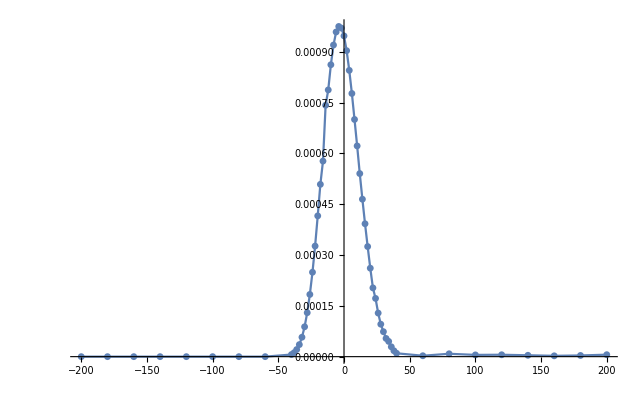

```mathematica
ListLinePlot[Transpose[{signalTime,AbsArg[data][[All,1]]}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

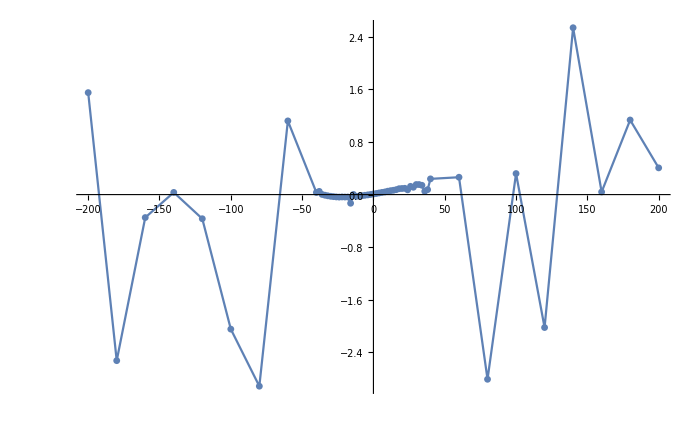

```mathematica
ListPlot[Transpose[{signalTime, AbsArg[data][[All,2]]}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

## Gate delay = τ

```mathematica
τ=50;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
Ω=3.37/ℏ(*The band gap/ℏ of ZnO in fs^-1*)
```

5.12158

## Term 1

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*Exp[ⅈ*Ω*t1+ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.086632,0.00284884+0.0000741484 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{40.4582,Null}

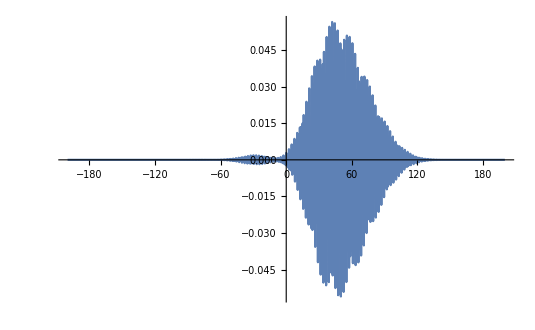

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

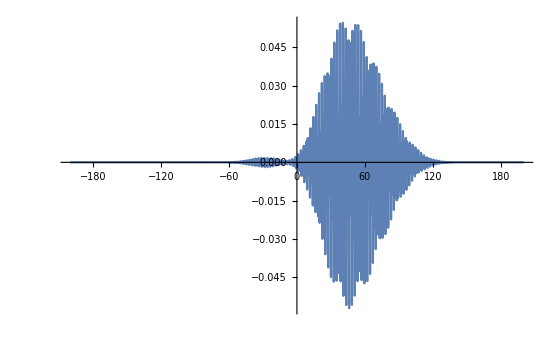

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.011037-0.00455834 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*Exp[-ⅈ*Ω*t2-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.140298,-0.00018717+0.00131802 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{60.8504,Null}

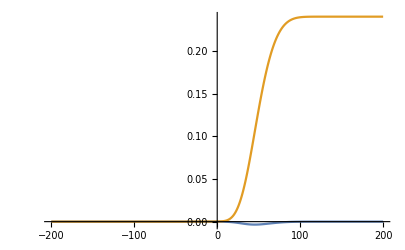

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{146.298,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**Exp[ⅈ*Ω*t1-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.027106,0.00112709+0.000167783 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{37.4899,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2+ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.099381,-6.96736×10^-6+0.000172839 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{45.316,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{127.144,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.054159,-0.0000954213-0.0568234 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{94.4668,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2+ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.27769,-6.87398×10^-9-1.40232×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{56.6173,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*Exp[ⅈ*Ω*t3-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{51.6255,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.060837,-0.0000954213-0.0568234 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{95.1061,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*Exp[-ⅈ*Ω*t2-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.293587,0.0559442-0.0163845 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{64.6028,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3+ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{50.0522,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*Exp[ⅈ*Ω*t1+ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.048175,0.000426465-0.0000332978 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{40.1616,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.425665,-3.78182×10^-8+4.72249×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{122.513,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*Exp[ⅈ*Ω*t3-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{50.9723,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**Exp[ⅈ*Ω*t1-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.054412,0.00786374+0.000488851 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{39.5647,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.328191,0.644883-0.140679 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{117.463,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3+ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{50.8168,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{timeRange,Re@totalenvelop}],Transpose[{timeRange,Im@totalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.227182

```mathematica
N@ArcTan[-10^7]
```

-1.5708

## Energy level modulation

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)*)
```

```mathematica
(*Ω=9.08/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
```

```mathematica
μ21x=μ12x=0;μ21y=μ12y=2.439;(*in a.u.*)
```

```mathematica
(*E0=1.41*10^-4;*)
```

```mathematica
(*ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)*)
```

### Varying Energy level using AC stark effect

```mathematica
Clear[Δ,Ω]
```

```mathematica
Δ=7.78/ℏ-ω0
```

9.47371

```mathematica
eAmpgate=√(2/(8.87*10^-12*3*10^8)*(0.09*10^12)/10^-4)(*Electric field from the laser intensity of 0.09TW/cm^2 to Volt/m*)
```

8.22458×10^8

```mathematica
eAmpprobe=√(2/(8.87*10^-12*3*10^8)*(0.05*10^12)/10^-4)(*Electric field from the laser intensity of 0.05TW/cm^2 to Volt/m*)
```

6.13024×10^8

```mathematica
convgate=(8.47835281×10^-30*eAmpgate)/(1.6*10^-19)(*This convert μ.E from a.u. to SI units to eV*)
convprobe=(8.47835281×10^-30*eAmpprobe)/(1.6*10^-19)
```

0.0435818

0.032484

```mathematica
Ω[t_,τ_]:=((μ21x+μ21y)/(√2)*2*gateEfull[t]**convgate/ℏ+μ21y*probeEfull[t-τ]**ⅇ^(ⅈ*ω0*τ)*convprobe/ℏ)(*Find the value of Ω = (μ.E)/ℏ in fs^-1*)
```

```mathematica
Ω[1,4]
```

0.105898+0.0043408 ⅈ

```mathematica
gap[t_,τ_]:=√(Δ^2+Abs[Ω[t,τ]]^2)
```

```mathematica
SetPrecision[gap[10,0],10]
```

9.478779868

```mathematica
Plot[gap[0,t],{t,-50,50}]
```

-Graphics-

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(gap[t1,τ]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.574927,-0.0711842+0.0000395822 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{71.6854,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.0591589+0.017616 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-gap[t2,τ]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.823411,-0.00386923+0.00384279 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{94.5751,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*gap[t3,τ]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{118.932,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(gap[t1,τ]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.272368,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{60.0367,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-gap[t2,τ]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.01038,-0.00488605+0.00159143 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{217.986,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*gap[t3,τ]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{214.322,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*gap[t1,τ]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.27287,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.0324,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-gap[t2,τ]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.66377,-2.13828×10^-9-9.35992×10^-10 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{220.499,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(gap[t3,τ]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{218.469,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*gap[t1,τ]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.268004,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.4042,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-gap[t2,τ]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.63387,-0.00235385+0.043102 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{262.403,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(gap[t3,τ]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.164,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(gap[t1,τ]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.274882,-0.0608233+0.0000286248 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{68.7788,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*gap[t2,τ]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.61223,-1.25044×10^-9-1.29453×10^-9 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{218.414,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(gap[t3,τ]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{225.72,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(gap[t1,τ]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.277448,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{61.3202,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*gap[t2,τ]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.59203,-0.0000923011+0.00203127 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{219.041,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(gap[t3,τ]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.422,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=μ12y*μ21y*(μ12x+μ12y)/(√2)*(μ21x+μ21y)/(√2)*(term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop);
```

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.327091

```mathematica
N@ArcTan[-10^7]
```

-1.5708

## Parameter dependencies

```mathematica
Plot[Re@Exp[ⅈ*Arg[gate1Afull[t]]],{t,-50,50}]
```

-Graphics-

```mathematica
NIntegrate[Exp[ⅈ*ω0*t1+ⅈ*Ω*t1+ⅈ*π/2],{t1,-50,50},Method->{"LocalAdaptive"}]//AbsoluteTiming
```

{0.007696,6.35603×10^-15-0.12372 ⅈ}

```mathematica
test[t2_]:=NIntegrate[Exp[ⅈ*ω0*t1+ⅈ*Ω*t1+ⅈ*Arg[gate1Afull[t1]]],{t1,-50,t2},Method->{"LocalAdaptive"}]
```

```mathematica
int1[a_,ω0_,Ω_,t2_]=Integrate[Exp[ⅈ*ω0*t1+ⅈ*Ω*t1+ⅈ*π/2],{t1,-a,t2}]//FullSimplify
```

(ⅇ^(-ⅈ a (Ω+ω0)) (-1+ⅇ^(ⅈ (a+t2) (Ω+ω0))))/(Ω+ω0)

```mathematica
ReImPlot[ⅇ^(ⅈ  *(Ω+ω0)*t)/(Ω+ω0)/.ω0->1/.Ω->1,{t,-100,100}]
```

-Graphics-

```mathematica
int2[a_,ω0_,Ω_,t3_]=Integrate[Exp[-ⅈ*ω0*t2-ⅈ*Ω*t2-ⅈ*π/2]*int1[a,ω0,Ω,t2],{t2,-a,t3}]
```

-(-1+ⅇ^(-ⅈ (a+t3) (Ω+ω0))+ⅈ (a+t3) (Ω+ω0))/(Ω+ω0)^2

```mathematica
Plot[Re@int2[50,2.35,11.8,t],{t,-50,100}]
```

-Graphics-

```mathematica
int3[a_,ω0_,Ω_,t_]=Exp[-ⅈ*Ω*t]*Integrate[Exp[ⅈ*ω0*t3+ⅈ*Ω*t3+ⅈ*π/2]*int2[a,ω0,Ω,t3],{t3,-a,t}]*Exp[-ⅈ*ω0*t]
```

(ⅇ^(-ⅈ t Ω-ⅈ t ω0-ⅈ a (Ω+ω0)) (-ⅈ a-ⅈ t+(-2-ⅈ ⅇ^(ⅈ (a+t) (Ω+ω0)) (2 ⅈ+(a+t) (Ω+ω0)))/(Ω+ω0)))/(Ω+ω0)^2

```mathematica
ReImPlot[int3[100,2.35,2,t],{t,-100,100}]
```

-Graphics-

```mathematica
|
```

## Time dependent integration

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
Ω=3.37/ℏ(*The band gap/ℏ of ZnO in fs^-1*)
```

5.12158

```mathematica
th[t_,t1_,t2_,t3_]:=gate1Afull[t1]*gate2Afull[t2]*probeAfull[t3]*Exp[ⅈ*(Ω*t+Ω*t1-Ω*t+Ω*t + ω0*(t1-t2+t3))]
```

```mathematica
th[1,1,1,1]//AbsoluteTiming
```

{0.000079,-0.00194581+0.072918 ⅈ}

```mathematica
int[t_]:=NIntegrate[gate1Afull[t1]*gate2Afull[t2]*probeAfull[t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->"LocalAdaptive"]
```

```mathematica
int[0]//AbsoluteTiming
```

{0.097891,-52.2573+1776.86 ⅈ}

```mathematica
NIntegrate[Cos[(Ω*(t1+t2+t3)+(-Ω)*(t1)+Ω*(t1+t2))+ω0*(-t3-t1)],{t1,0,100},{t2,0,100},{t3,0,100}]
```

0.000664609

```mathematica
testint[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*(Ω*(t1+t2+t3)+(-Ω)*(t1)+Ω*(t1+t2))+ⅈ*ω0*(-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
test2int[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*(Ω-ω0)*t1]*Exp[ⅈ*(Ω)*2*t2]*Exp[ⅈ*(Ω-ω0)*t3],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
test3int[t_]:=NIntegrate[gate1Afull[t-t3-t2-t1]*gate2Afull[t-t3-t2]*probeAfull[t-t3]*Exp[ⅈ*((Ω-ω0)*t1+(Ω)*2*t2+(Ω-ω0)*t3)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
testint[0]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000950398+8.85989×10^-6 ⅈ and 0.0038159 for the integral and error estimates.

{68.2492,0.000950398+8.85989×10^-6 ⅈ}

```mathematica
test2int[-14]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000742393+1.50434×10^-6 ⅈ and 0.00296239 for the integral and error estimates.

{63.7889,0.000742393+1.50434×10^-6 ⅈ}

```mathematica
test3int[10]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000621504+0.0000320205 ⅈ and 0.00655749 for the integral and error estimates.

{82.6608,0.000621504+0.0000320205 ⅈ}

```mathematica
it[t_]:=NIntegrate[gate1Afull[0]*gate2Afull[t1]*probeAfull[t1+t2]*Exp[ⅈ*(Ω*t+Ω*(t-t3-t2-t1)+(-Ω)*(t-t3-t2)+Ω*(t-t3))+ⅈ*ω0*(-t3-t1)],{t1,0,∞},{t2,0,∞},{t3,0,∞},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
it[0]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in t3 near {t1,t2,t3} = {0.015625,0.03125,1.}. NIntegrate obtained -0.0704524-0.0334957 ⅈ and 0.621179 for the integral and error estimates.

{2.95663,-0.0704524-0.0334957 ⅈ}

```mathematica
signalTime=Join[Range[-200,-60,20],Range[-40,40,2],Range[60,200,20]];
```

```mathematica
AbsoluteTiming[data=ParallelMap[Quiet[testint[#]]&,signalTime]]
```

{1037.47,{1.85716×10^-20+9.36134×10^-19 ⅈ,-1.23117×10^-17-8.71369×10^-18 ⅈ,7.88407×10^-17-2.87105×10^-17 ⅈ,7.88828×10^-14+2.62403×10^-15 ⅈ,3.95894×10^-13-1.5229×10^-13 ⅈ,-1.34466×10^-10-2.61102×10^-10 ⅈ,-5.25463×10^-9-1.21503×10^-9 ⅈ,3.07911×10^-10+6.37576×10^-10 ⅈ,6.22087×10^-6+1.988×10^-7 ⅈ,0.0000116492+5.69367×10^-7 ⅈ,0.0000210279+5.4305×10^-8 ⅈ,0.0000355907-3.35024×10^-7 ⅈ,0.0000573119-1.04355×10^-6 ⅈ,0.0000881973-2.27866×10^-6 ⅈ,0.000129747-4.02927×10^-6 ⅈ,0.000183616-6.51751×10^-6 ⅈ,0.000249113-9.46909×10^-6 ⅈ,0.000326405-0.0000116097 ⅈ,0.000415472-0.0000153661 ⅈ,0.000508482-0.0000187667 ⅈ,0.000572547-0.0000758297 ⅈ,0.000742393+1.50434×10^-6 ⅈ,0.000787393-0.0000217955 ⅈ,0.000861902-0.0000191141 ⅈ,0.000920144-0.0000151996 ⅈ,0.000958818-0.0000102032 ⅈ,0.000975119-4.53076×10^-6 ⅈ,0.000970309+1.76001×10^-6 ⅈ,0.000947224+9.33564×10^-6 ⅈ,0.000903471+0.0000150474 ⅈ,0.000845208+0.0000210741 ⅈ,0.000776761+0.0000257377 ⅈ,0.000699941+0.0000280678 ⅈ,0.000621504+0.0000320205 ⅈ,0.00053972+0.0000321313 ⅈ,0.000463972+0.0000305083 ⅈ,0.000391362+0.0000294232 ⅈ,0.000323836+0.0000290566 ⅈ,0.000260168+0.0000241827 ⅈ,0.000202194+0.0000194037 ⅈ,0.000171592+0.0000124026 ⅈ,0.000127738+0.0000161207 ⅈ,0.0000952214+0.0000106401 ⅈ,0.0000728729+0.0000112299 ⅈ,0.0000531806+8.18955×10^-6 ⅈ,0.0000445612+6.35055×10^-6 ⅈ,0.0000290804+1.46718×10^-6 ⅈ,0.0000173362+1.31145×10^-6 ⅈ,9.65027×10^-6+2.35336×10^-6 ⅈ,2.59871×10^-6+7.02227×10^-7 ⅈ,-8.0212×10^-6-2.7695×10^-6 ⅈ,4.90525×10^-6+1.62501×10^-6 ⅈ,-2.44048×10^-6-5.03548×10^-6 ⅈ,-3.32833×10^-6+2.29348×10^-6 ⅈ,2.4482×10^-6+9.80277×10^-8 ⅈ,1.48106×10^-6+3.17749×10^-6 ⅈ,5.31999×10^-6+2.29025×10^-6 ⅈ}}

```mathematica
ListLinePlot[{Transpose[{signalTime,Re[data]}],Transpose[{signalTime,Im[data]}]},PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

-Graphics-

```mathematica
(*Mean[ParallelMap[gateAvector[t-#[[3]]-#[[2]]-#[[1]]]*gateAvector[t-#[[3]]-#[[2]]]*probeAvector[t-#[[3]]]/.t->0&,RandomReal[{0,230},{n,3}]]]*(230)^3//AbsoluteTiming*)
```

```mathematica
microcurrent=Interpolation[Transpose[{signalTime,data}]]
```

InterpolatingFunction[…]

```mathematica
ListLinePlot[Transpose[{signalTime,AbsArg[data][[All,1]]}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{signalTime, AbsArg[data][[All,2]]}],PlotRange->Full,Joined->True,PlotMarkers->{Automatic,7}]
```

-Graphics-

# Non-Perturbative

## Parameters

```mathematica
(*ℏ=0.658;(*Value of ℏ in eV fs*)*)
```

```mathematica
(*ϵv=0;ϵα=7.77/ℏ;ϵβ=7.77/ℏ;ϵγ=7.77/ℏ;ϵδ=7.77/ℏ;*)
```

```mathematica
(*jx12=1;jy12=1;jx21=1;jy21=1;*)
```

```mathematica
(*E0probe=√(2/(8.87*10^-12*3*10^8)*0.05*10^16)(*In the SI units, for the laser intensity of 0.05 TW/cm^2*)*)
```

6.13024×10^8

```mathematica
(*E0gate=√(2/(8.87*10^-12*3*10^8)*0.09*10^16)*)
```

8.22458×10^8

## Parameters in a.u.

```mathematica
(*ℏ=1*)
```

```mathematica
ϵv=0;ϵα=7.77/27.21;ϵβ=7.77/27.21;ϵγ=7.77/27.21;ϵδ=7.77/27.21;(*Band gap in a.u.*)
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

```mathematica
E0probe=0.05*10^12/(3.15*10^16)(*In the a.u., for the laser intensity of 0.05 TW/cm^2*)
```

1.5873×10^-6

```mathematica
E0gate=0.09*10^12/(3.15*10^16)(*In the a.u., for the laser intensity of 0.09 TW/cm^2*)
```

2.85714×10^-6

```mathematica
jx12=jy12=jx21=jy21=0.01;
```

## Coupled equation

```mathematica
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(probeAfull[t-230]*jy12*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aα[t]+(gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aβ[t]+((probeAfull[t-230])**jy12**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aγ[t]+(((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+((probeAfull[t-230])**jy21**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+(((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(probeAfull[t-230]*jy21*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+(gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t]};*)
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(jy12*ⅇ^(ⅈ*ω0*(t-230))+(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aα[t]+((jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aβ[t]+(jy12**ⅇ^(-ⅈ*ω0*(t-230))+(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aγ[t]+((jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+(jy21**ⅇ^(-ⅈ*ω0*(t-230))+(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+((jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(jy21*ⅇ^(ⅈ*ω0*(t-230))+(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+((jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t]};*)
eqn={ⅈ*ℏ*bv'[t]==ϵv*bv[t]+probeAfull[t-230]*jy12*bα[t]+(gate1Afull[t-230]*(jx12+jy12)/(√2))*bβ[t]+(gate1Afull[t-230]*(jx12+jy12)/(√2))*bγ[t],ⅈ*ℏ*bα'[t]==(ϵα-ℏ*ω0)*bα[t]+(probeAfull[t-230])**jy21**bv[t],ⅈ*ℏ*bβ'[t]==(ϵβ-ℏ*ω0)*bβ[t]+(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t],ⅈ*ℏ*bγ'[t]==(ϵγ-ℏ*ω0)*bγ[t]+(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t],ⅈ*ℏ*bδ'[t]==(ϵδ-ℏ*ω0)*bδ[t]};
(*initialcond={av[0]==1,aα[0]==0,aβ[0]==0,aγ[0]==0,aδ[0]==0};*)
initialcond={bv[0]==1,bα[0]==0,bβ[0]==0,bγ[0]==0,bδ[0]==0};
```

```mathematica
(*sol=NDSolve[Join[eqn,initialcond],{av,aα,aβ,aγ,aδ},{t,0,430}]*)
sol=NDSolve[Join[eqn,initialcond],{bv,bα,bβ,bγ,bδ},{t,0,430}]
```

{{bv→InterpolatingFunction[…],bα→InterpolatingFunction[…],bβ→InterpolatingFunction[…],bγ→InterpolatingFunction[…],bδ→InterpolatingFunction[…]}}

```mathematica
bvsol[t_]:=bv[t]/.sol[[1]]
bαsol[t_]:=bα[t]/.sol[[1]]
bβsol[t_]:=bβ[t]/.sol[[1]]
bγsol[t_]:=bγ[t]/.sol[[1]]
bδsol[t_]:=bδ[t]/.sol[[1]]
```

```mathematica
jky[t_]:=jy12*bvsol[t+230]**bγsol[t+230]
```

```mathematica
(*Plot[{Re[avsol[t+230]**aγsol[t+230]],Im[avsol[t+230]**aγsol[t+230]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]*)
Plot[{Re[jky[t]],Im[jky[t]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
timeGrid=Range[-230,200,0.1];
```

```mathematica
Plot[{Re[jky[t+230]],Im[jky[t+230]]},{t,-3,3}]
```

-Graphics-

## Coupled equation with time delay τ

```mathematica
Clear[eqn,sol,initialcond,bvsol,bαsol,bβsol,bγsol,bδsol,jky]
```

```mathematica
τ=10;
```

```mathematica
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(probeAfull[t-230]*jy12*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aα[t]+(gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aβ[t]+((probeAfull[t-230])**jy12**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aγ[t]+(((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+((probeAfull[t-230])**jy21**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+(((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(probeAfull[t-230]*jy21*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+(gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t]};*)
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(jy12*ⅇ^(ⅈ*ω0*(t-230))+(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aα[t]+((jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aβ[t]+(jy12**ⅇ^(-ⅈ*ω0*(t-230))+(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*aγ[t]+((jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+(jy21**ⅇ^(-ⅈ*ω0*(t-230))+(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+((jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(jy21*ⅇ^(ⅈ*ω0*(t-230))+(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+((jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*av[t]};*)
(*eqn={ⅈ*bv'[t]==ϵv*bv[t]+probeAfull[t-τ-230]*ⅇ^(-ⅈ*ω0*(τ+230))*jy12*bα[t]+(gate1Afull[t-230]*(jx12+jy12)/(√2))*bβ[t]+(gate1Afull[t-230]*(jx12+jy12)/(√2))*bγ[t],ⅈ*bα'[t]==(ϵα-ω0)*bα[t]+(probeAfull[t-τ-230])**ⅇ^(ⅈ*ω0*(τ+230))*jy21**bv[t],ⅈ*bβ'[t]==(ϵβ-ω0)*bβ[t]+(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t],ⅈ*bγ'[t]==(ϵγ-ω0)*bγ[t]+(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t]};*)
eqn={ⅈ*bv'[t]==ϵv*bv[t]+E0probe/2*probeAfull[t-τ-230]*ⅇ^(-ⅈ*ω0*(τ+230))*jy12*bα[t]+E0gate/2*(gate1Afull[t-230]*(jx12+jy12)/(√2))*bβ[t]+E0gate/2*(gate1Afull[t-230]*(jx12+jy12)/(√2))*bγ[t],ⅈ*bα'[t]==(ϵα-ω0au)*bα[t]+E0probe/2*(probeAfull[t-τ-230])**ⅇ^(ⅈ*ω0*(τ+230))*jy21**bv[t],ⅈ*bβ'[t]==(ϵβ-ω0au)*bβ[t]+E0gate/2*(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t],ⅈ*bγ'[t]==(ϵγ-ω0au)*bγ[t]+E0gate/2*(gate1Afull[t-230])**(jx21*+jy21*)/(√2)*bv[t]};(*in a.u.*)
(*initialcond={av[0]==1,aα[0]==0,aβ[0]==0,aγ[0]==0,aδ[0]==0};*)
initialcond={bv[0]==1,bα[0]==0,bβ[0]==0,bγ[0]==0};
```

```mathematica
(*sol=NDSolve[Join[eqn,initialcond],{av,aα,aβ,aγ,aδ},{t,0,430}]*)
sol=NDSolve[Join[eqn,initialcond],{bv,bα,bβ,bγ},{t,0,430}]
```

{{bv→InterpolatingFunction[…],bα→InterpolatingFunction[…],bβ→InterpolatingFunction[…],bγ→InterpolatingFunction[…]}}

```mathematica
bvsol[t_]:=bv[t]/.sol[[1]]
bαsol[t_]:=bα[t]/.sol[[1]]
bβsol[t_]:=bβ[t]/.sol[[1]]
bγsol[t_]:=bγ[t]/.sol[[1]]
(*bδsol[t_]:=bδ[t]/.sol[[1]]*)
```

```mathematica
GraphicsRow[{ReImPlot[{bvsol[t+230](*bγsol[t+230]*)},{t,-230,200},PlotRange->All],ReImPlot[{bγsol[t+230]},{t,-230,200},PlotRange->All]}]
```

-Graphics-

```mathematica
jky[t_]:=jy12*bvsol[t+230]**bγsol[t+230]
```

```mathematica
(*Plot[{Re[avsol[t+230]**aγsol[t+230]],Im[avsol[t+230]**aγsol[t+230]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]*)
Plot[{Re[jky[t]],Im[jky[t]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
Plot[Abs[jky[t]],{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
timeRange=Range[-200,200,1];
```

```mathematica
(*data=ParallelMap[jky[#,0]&,timeRange];//AbsoluteTiming*)
```

```mathematica
(*ListPlot[{Transpose[{timeRange,Re@data}],Transpose[{timeRange,Im@data}]},PlotRange->Full]*)
```

```mathematica
(*ListPlot[{Transpose[{timeRange,Abs@data}]},PlotRange->Full]*)
```

## Coupled equation in Interaction picture

```mathematica
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(probeAfull[t]*jy12*ⅇ^(ⅈ*ω0*t)+((gate1Afull[t])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*t))*aα[t]+(gate1Afull[t]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*t))*aβ[t]+((probeAfull[t])**jy12**ⅇ^(-ⅈ*ω0*t)+gate1Afull[t]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*t))*aγ[t]+(((gate1Afull[t])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*t))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+((probeAfull[t])**jy21**ⅇ^(-ⅈ*ω0*t)+gate1Afull[t]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*t))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+(((gate1Afull[t])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*t))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(probeAfull[t]*jy21*ⅇ^(ⅈ*ω0*t)+((gate1Afull[t])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*t))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+(gate1Afull[t]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*t))*av[t]};*)
(*eqn={ⅈ*av'[t]==ϵv*av[t]+(probeAfull[t-230]*jy12*ⅇ^(ⅈ*ω0*t)+((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*t))*aα[t]+(gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*t))*aβ[t]+((probeAfull[t-230])**jy12**ⅇ^(-ⅈ*ω0*t)+gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*t))*aγ[t]+(((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*t))*aδ[t], ⅈ*aα'[t]==ϵα*aα[t]+((probeAfull[t-230])**jy21**ⅇ^(-ⅈ*ω0*t)+gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*t))*av[t],ⅈ*aβ'[t]==ϵβ*aβ[t]+(((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*t))*av[t], ⅈ*aγ'[t]==ϵγ*aγ[t]+(probeAfull[t-230]*jy21*ⅇ^(ⅈ*ω0*t)+((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*t))*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+(gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*t))*av[t]};*)
(*eqn={ⅈ*av'[t]==(probeAfull[t-230]*jy12*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵv-ϵα)*t)*aα[t]+(gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵv-ϵβ)*t)*aβ[t]+((probeAfull[t-230])**jy12**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx12+jy12)*ⅇ^(ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵv-ϵγ)*t)*aγ[t]+(((gate1Afull[t-230])*)/(√2)*(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵv-ϵδ)*t)*aδ[t], ⅈ*aα'[t]==((probeAfull[t-230])**jy21**ⅇ^(-ⅈ*ω0*(t-230))+gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵα-ϵv)*t)*av[t],ⅈ*aβ'[t]==(((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵβ-ϵv)*t)*av[t], ⅈ*aγ'[t]==(probeAfull[t-230]*jy21*ⅇ^(ⅈ*ω0*(t-230))+((gate1Afull[t-230])*)/(√2)*(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵγ-ϵv)*t)*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+(gate1Afull[t-230]/(√2)*(jx21+jy21)*ⅇ^(ⅈ*ω0*(t-230)))*ⅇ^(ⅈ*(ϵδ-ϵv)*t)*av[t]};*)
eqn={ⅈ*av'[t]==(jy12*ⅇ^(ⅈ*ω0*(t))+(jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵv-ϵα)*t)*aα[t]+((jx12+jy12)*ⅇ^(ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵv-ϵβ)*t)*aβ[t]+(jy12**ⅇ^(-ⅈ*ω0*(t))+(jx12+jy12)*ⅇ^(ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵv-ϵγ)*t)*aγ[t]+((jx12*+jy12*)*ⅇ^(-ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵv-ϵδ)*t)*aδ[t], ⅈ*aα'[t]==(jy21**ⅇ^(-ⅈ*ω0*(t))+(jx21+jy21)*ⅇ^(ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵα-ϵv)*t)*av[t],ⅈ*aβ'[t]==((jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵβ-ϵv)*t)*av[t], ⅈ*aγ'[t]==(jy21*ⅇ^(ⅈ*ω0*(t))+(jx21*+jy21*)*ⅇ^(-ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵγ-ϵv)*t)*av[t],ⅈ*aδ'[t]==ϵδ*aδ[t]+((jx21+jy21)*ⅇ^(ⅈ*ω0*(t)))*ⅇ^(ⅈ*(ϵδ-ϵv)*t)*av[t]};
initialcond={av[0]==1,aα[0]==0,aβ[0]==0,aγ[0]==0,aδ[0]==0};
```

```mathematica
sol=NDSolve[Join[eqn,initialcond],{av,aα,aβ,aγ,aδ},{t,0,430},AccuracyGoal->MachinePrecision]
```

{{av→InterpolatingFunction[{{0., 430.}}, <>],aα→InterpolatingFunction[{{0., 430.}}, <>],aβ→InterpolatingFunction[{{0., 430.}}, <>],aγ→InterpolatingFunction[{{0., 430.}}, <>],aδ→InterpolatingFunction[{{0., 430.}}, <>]}}

```mathematica
avsol[t_]:=av[t]/.sol[[1]]
aαsol[t_]:=aα[t]/.sol[[1]]
aβsol[t_]:=aβ[t]/.sol[[1]]
aγsol[t_]:=aγ[t]/.sol[[1]]
aδsol[t_]:=aδ[t]/.sol[[1]]
```

```mathematica
jky[t_]:=avsol[t]**aγsol[t]*ⅇ^(ⅈ*(ϵv-ϵγ)*t)
```

```mathematica
Plot[{Re[jky[t+230]],Im[jky[t+230]]},{t,-5,5},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
Plot[{Re[jky[t+230]],Im[jky[t+230]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
Plot[{Re[avsol[t+230]**aγsol[t+230]],Im[avsol[t+230]**aγsol[t+230]]},{t,-230,200},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 17],Style["(a_(q - ky, γ))^*a_(q, v)",20]}]
```

-Graphics-

```mathematica
ReImPlot[2*Re[jky[t+230]],{t,-230,200},AxesLabel->{"time (fs)","<J_ky>"},PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["<(J^y)_kf>",25]},FrameTicksStyle->Directive[FontSize->25]]
```

-Graphics-

```mathematica
zerolist=DeleteDuplicates[Sort[t/.FindRoot[2*Re[jky[t]]==0,{t,#},AccuracyGoal->Infinity]&/@Range[180,280]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{180.986,182.255,182.931,184.949,185.532,186.033,187.12,187.912,189.043,189.454,190.982,191.979,193.016,194.015,195.552,195.967,197.1,197.873,198.977,200.052,202.066,202.156,202.738,204.021,204.344,205.937,207.038,208.241,208.971,210.118,210.927,212.074,212.91,214.002,215.097,215.895,216.655,217.027,218.978,219.923,220.975,222.016,223.192,223.952,225.084,225.865,227.03,227.995,229.041,230.066,230.691,232.008,233.912,233.916,235.006,236.067,236.962,238.117,238.923,240.064,240.804,241.971,243.069,245.016,246.168,246.563,246.976,248.44,248.935,250.022,251.187,251.932,253.069,253.872,255.029,255.943,257.,258.073,258.089,259.989,261.319,261.922,262.964,264.014,264.96,266.122,266.913,268.046,268.802,269.971,271.03,272.085,273.01,274.219,274.969,276.104,276.9,278.007,279.096,279.917}

```mathematica
ListLinePlot[Table[2*π/(zerolist[[i+2]]-zerolist[[i]]),{i,1,Length[zerolist]-2,1}],PlotMarkers->{Automatic, 5}]
```

-Graphics-

```mathematica
timeGrid=Range[-230,200,0.1];
```

```mathematica
(*ListLinePlot[Transpose[{timeGrid,ParallelMap[Abs[jky[#+230]]&,timeGrid]}],PlotRange->All]*)
```

```mathematica
(*Plot[Arg[jky[t+230]],{t,-50,50}]*)
```

```mathematica
(*ListLinePlot[{Transpose[{timeGrid,ParallelMap[Re[jky[#+230]]&,timeGrid]}],Transpose[{timeGrid,ParallelMap[Im[jky[#+230]]&,timeGrid]}]},PlotRange->All,PlotMarkers->{Automatic,6}]*)
```

```mathematica
(*jkyEnvelopReal=SubsetMap[timeGrid[[#]]&,FindPeaks[ParallelMap[Re[jky[#+230]]&,timeGrid]],{All,1}];
jkyEnvelopImag=SubsetMap[timeGrid[[#]]&,FindPeaks[ParallelMap[Im[jky[#+230]]&,timeGrid]],{All,1}];*)
```

```mathematica
(*ListLinePlot[{jkyEnvelopReal,jkyEnvelopImag},PlotRange->All,PlotMarkers->Automatic]*)
```

```mathematica
(*jkyEnvelopRealfn=Interpolation[jkyEnvelopReal]
jkyEnvelopImagfn=Interpolation[jkyEnvelopImag]*)
```

```mathematica
(*Plot[Im[√(jkyEnvelopRealfn[t]^2+jkyEnvelopImagfn[t]^2)*Exp[ⅈ*ω0*t]],{t,-220,200},PlotRange->Full]*)
```

```mathematica
(*Plot[√(jkyEnvelopRealfn[t]^2+jkyEnvelopImagfn[t]^2),{t,-220,200}]*)
```

```mathematica
(*jky[230]*)
```

```mathematica
(*Plot[Abs[jky[t+230]],{t,-10,10}]*)
```

```mathematica
Plot[{Re[jky[t+230]],Im[jky[t+230]]},{t,-3,3}]
```

-Graphics-

```mathematica
Export
```

# Non-Perturbative for CO2 molecule

## Electric fields

## E1

```mathematica
gateEenvelopfn=Interpolation[Transpose[{gatedata[[All,1]],gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
gateEfull[t_]=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gateEenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
ReImPlot[gateEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
ReImPlot[gateEfull'[t],{t,-300,300},PlotRange->All]
```

-Graphics-

## E2

```mathematica
gateEconjenvelopfn=Interpolation[Transpose[{gatedata[[All,1]],gatedata[[All,2]]*Exp[-ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
gateE2full[t_]=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gateEconjenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
ReImPlot[gateE2full[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
ReImPlot[gateE2full[t],{t,-200,200},PlotRange->All]
```

-Graphics-

## E3

```mathematica
probeEenvelopfn=Interpolation[Transpose[{probedata[[All,1]],probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
probeEfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeEenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

```mathematica
ReImPlot[probeEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
ReImPlot[probeEfull'[t],{t,-300,300},PlotRange->All]
```

-Graphics-

## Parameters

```mathematica
ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)
```

```mathematica
μ21x=μ12x=0.020866;μ21y=μ12y=0.0029339;(*in a.u.*)
```

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

## Hamiltonian

all the calculations are done in a.u. (atomic units) ℏ=1 e=1

```mathematica
(*eqn={ⅈ*a1'[t]==ϵ1*a1[t]+a2[t]*(μ12x+μ12y)*√2*E0*Re[gateEfull[t-230]*ⅇ^(ⅈ*ω0*(t-230))]+a2[t]*μ12y*E0*Re[probeEfull[t-230]*ⅇ^(ⅈ*ω0*(t-230))],ⅈ*a2'[t]==ϵ2*a2[t]+a1[t]*(μ21x+μ21y)*√2*E0*Re[gateEfull[t-230]*ⅇ^(ⅈ*ω0*(t-230))]+a1[t]*μ21y*E0*Re[probeEfull[t-230]*ⅇ^(ⅈ*ω0*(t-230))]};
initialcond={a1[0]==1,a2[0]==0};*)
```

```mathematica
(*sol=NDSolve[Join[eqn,initialcond],{a1,a2},{t,0,430}]*)
```

b1[t] = a1[t] and b2[t] = a2[t] ⅇ^(ⅈ*ω0*t) and then using rotating wave approximation

## τ=0

```mathematica
eqn={ⅈ*b1'[t]==ϵ1*b1[t]+b2[t]*(μ12x+μ12y)*√2*E0/2*gateEfull[t-230]+b2[t]*μ12y*E0/2*probeEfull[t-230],ⅈ*b2'[t]==(ϵ2-ω0au)*b2[t]+b1[t]*(μ21x+μ21y)*√2*E0/2*gateEfull[t-230]*+b1[t]*μ21y*E0/2*probeEfull[t-230]*};
initialcond={b1[0]==1,b2[0]==0};
```

```mathematica
sol=NDSolve[Join[eqn,initialcond],{b1,b2},{t,0,430}]
```

{{b1→InterpolatingFunction[…],b2→InterpolatingFunction[…]}}

```mathematica
b1sol[t_]:=b1[t]/.sol[[1]]
b2sol[t_]:=b2[t]/.sol[[1]]
```

```mathematica
e[t_]:=ComplexExpand[μ21x*b2sol[t+230]*b1sol[t+230]*,TargetFunctions->{Re, Im}]
```

```mathematica
Plot[{Re[e[t]],Im[e[t]]},{t,-230,200},PlotRange->All]
```

-Graphics-

### Rough

```mathematica
p1[t_]=D[e[t]*ⅇ^(ⅈ*ω0*t),t]/D[E0*gateEfull[t]*ⅇ^(ⅈ*ω0*t),t];
```

```mathematica
p1[0]
```

-0.00114293+3.33264×10^-7 ⅈ

```mathematica
ReImPlot[p1[t],{t,-200,200}]
```

-Graphics-

```mathematica
p2[t_]=(D[e[t],t]+ⅈ*ω0*e[t])/(D[E0*probeEfull[t],t]+ⅈ*ω0*E0*probeEfull[t]);
```

```mathematica
p2[0]
```

-0.00112937-5.96161×10^-6 ⅈ

```mathematica
ReImPlot[p2[t],{t,-200,200}]
```

-Graphics-

```mathematica
Plot[Abs[p1[t]],{t,-200,200},PlotRange->All]
```

-Graphics-

```mathematica
ParametricPlot[{Abs[probeEfull[t]],10^7 Abs[e[t]]},{t,-200,200}]
```

-Graphics-

```mathematica
NIntegrate[gateE2full[t]*probeEfull[t],{t,-50,50}]
```

41.9707+2.28169 ⅈ

```mathematica
ReImPlot[gateE2full[t]*probeEfull[t],{t,-100,100},PlotRange->Full]
```

-Graphics-

## τ=finite

### Set up the numerical calculation

```mathematica
Clear[eqn,sol,initialcond,e,b1sol,b2sol]
```

```mathematica
(*τ=5;*)
```

```mathematica
eqn[τ_]={ⅈ*b1'[t]==ϵ1*b1[t]+b2[t]*(μ12x+μ12y)*√2*E0/2*gateEfull[t-230]+b2[t]*μ12y*E0/2*probeEfull[t-τ-230]*ⅇ^(-ⅈ*ω0*(τ+230)),ⅈ*b2'[t]==(ϵ2-ω0au)*b2[t]+b1[t]*(μ21x+μ21y)*√2*E0/2*gateEfull[t-230]*+b1[t]*μ21y*E0/2*probeEfull[t-τ-230]**ⅇ^(ⅈ*ω0*(τ+230))};
initialcond={b1[0]==1,b2[0]==0};
```

```mathematica
sol[τ_]:=NDSolve[Join[eqn[τ],initialcond],{b1,b2},{t,0,430}];
```

```mathematica
b1sol[t_,τ_]:=b1[t]/.sol[τ][[1]]
b2sol[t_,τ_]:=b2[t]/.sol[τ][[1]]
```

```mathematica
b2sol[200,3]
```

-3.55515×10^-6-5.568×10^-7 ⅈ

```mathematica
p[t_,τ_]:=ComplexExpand[μ21x*b2sol[t+230,τ]*b1sol[t+230,τ]*,TargetFunctions->{Re, Im}]
```

```mathematica
p[200,0]
```

-2.16597×10^-9-2.61073×10^-9 ⅈ

```mathematica
firstDE[t_]=D[p[t,0],t]/gateEfull'[t]*gateEfull[t];
```

```mathematica
ReImPlot[firstDE[t],{t,-200,200},PlotRange->Full]
```

-Graphics-

```mathematica
timeRange=Range[-200,200,1];
```

```mathematica
data=ParallelMap[p[#,0]&,timeRange];//AbsoluteTiming
```

{1.92041,Null}

```mathematica
ListPlot[{Transpose[{timeRange,Re@data}],Transpose[{timeRange,Im@data}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{timeRange,Abs@data}]},PlotRange->Full]
```

-Graphics-

### Export data for different time delay

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["datafile.csv", timeRange];
```

```mathematica
(*Export["datafile.csv",MapThread[Append,{Import["datafile.csv"],data}]];*)
```

```mathematica
timeDelayRange=Range[-40,40,0.2];
```

```mathematica
Do[data=ParallelMap[p[#,τ]&,timeRange];
Export["datafile.csv",MapThread[Append,{Import["datafile.csv"],data}]];,{τ,timeDelayRange}]//AbsoluteTiming
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

$Aborted

```mathematica
Export["Efield_datafile.csv", timeRange];
```

```mathematica
Do[data=ParallelMap[(2*gateEfull[#]*ⅇ^(ⅈ*ω0*#)+probeEfull[#-τ]*ⅇ^(ⅈ*ω0*(#-τ)))&,timeRange];
Export["Efield_datafile.csv",MapThread[Append,{Import["Efield_datafile.csv"],data}]];,{τ,timeDelayRange}]//AbsoluteTiming
```

{155.359,Null}

```mathematica
(*Block[{τ=5},ReImPlot[b1sol[t+230,7],{t,-230,200}]]*)
```

```mathematica
(*Plot[{Re[e[t+230,5]],Im[e[t+230,5]]},{t,-230,200},PlotRange->All]*)
```

```mathematica
(*Plot[Abs[e[t+230]],{t,-230,200}]*)
```

```mathematica
Perturbative for CO2 molecule
```

### Partial derivative wrt input pulses

```mathematica
Clear[eqn,sol,initialcond,e,b1sol,b2sol]
```

```mathematica
(*τ=5;*)
```

```mathematica
eqn[τ_]={ⅈ*b1'[t]==ϵ1*b1[t]+b2[t]*(μ12x+μ12y)*√2*E0/2*gateEfull[t-230],ⅈ*b2'[t]==(ϵ2-ω0au)*b2[t]+b1[t]*(μ21x+μ21y)*√2*E0/2*gateEfull[t-230]*};
initialcond={b1[0]==1,b2[0]==0};
```

```mathematica
sol[τ_]:=NDSolve[Join[eqn[τ],initialcond],{b1,b2},{t,0,430}];
```

```mathematica
b1sol[t_,τ_]:=b1[t]/.sol[τ][[1]]
b2sol[t_,τ_]:=b2[t]/.sol[τ][[1]]
```

```mathematica
b2sol[200,3]
```

-3.54713×10^-6-5.48003×10^-7 ⅈ

```mathematica
p[t_,τ_]:=ComplexExpand[μ21x*b2sol[t+230,τ]*b1sol[t+230,τ]*,TargetFunctions->{Re, Im}]
```

```mathematica
p[200,0]
```

-2.6295×10^-9-2.45699×10^-9 ⅈ

```mathematica
firstDE[t_]=(D[p[t,0],t]+ⅈ*ω0*p[t,0])/(gateEfull'[t]+ⅈ*ω0*gateEfull[t])*gateEfull[t];
```

```mathematica
ReImPlot[firstDE[t],{t,-200,200},PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Range[-100,100,1],ResourceFunction["PhaseUnwrap"][ParallelMap[Arg[firstDE[#]]&,Range[-100,100,1]]]}]]
```

-Graphics-

# Kubo Formula for CO2

## Electric fields

```mathematica
gateEenvelopfn=Interpolation[Transpose[{gatedata[[All,1]],gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
gateEfull[t_]=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gateEenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
ReImPlot[gateEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
probeEenvelopfn=Interpolation[Transpose[{probedata[[All,1]],probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
probeEfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeEenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

```mathematica
ReImPlot[probeEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
ReImPlot[probeEfull''[t],{t,-300,300},PlotRange->All]
```

-Graphics-

## Time delay = τ

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)
```

```mathematica
Ω=9.08/ℏ(*The band gap/ℏ of MgO in fs^-1*)
```

13.7994

```mathematica
μ21x=μ12x=0.020866;μ21y=μ12y=0.0029339;(*in a.u.*)
```

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

## Term 1

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.30992,-0.0608233+0.0000286248 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.1636,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0182019+0.0495001 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.02745,-0.00292159+0.0338264 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{220.799,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{213.558,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.272368,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{60.0367,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.01038,-0.00488605+0.00159143 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{217.986,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{214.322,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*Ω*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.27287,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.0324,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-Ω+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.66377,-2.13828×10^-9-9.35992×10^-10 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{220.499,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{218.469,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*Ω*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.268004,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.4042,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-Ω-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.63387,-0.00235385+0.043102 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{262.403,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.164,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(Ω+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.274882,-0.0608233+0.0000286248 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{68.7788,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.61223,-1.25044×10^-9-1.29453×10^-9 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{218.414,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{225.72,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,0.5];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(Ω-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.277448,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{61.3202,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*Ω*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.59203,-0.0000923011+0.00203127 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{219.041,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.422,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{timeRange,Re@totalenvelop}],Transpose[{timeRange,Im@totalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.327091

```mathematica
N@ArcTan[-10^7]
```

-1.5708

## 1st order terms

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)
```

```mathematica
Ω=9.08/ℏ(*The band gap/ℏ of MgO in fs^-1*)
```

13.7994

```mathematica
μ21x=μ12x=0.020866;μ21y=μ12y=0.0029339;(*in a.u.*)
```

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t1]*Exp[ⅈ*ω0*t1]*(μ12x*μ21x+μ12x*μ21y)/(√2)+probeEfull[t1-τ]*Exp[ⅈ*ω0*(t1-τ)]*μ12x*μ21y)*Exp[ⅈ*Ω*t1],{t1,-∞,t},Method->{"LocalAdaptive"}]*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{1.30737,-0.0000464789+1.88254×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{160.218,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
etotalenvelop=dataint1*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Full 3rd order terms

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)
```

```mathematica
Ω=9.08/ℏ(*The band gap/ℏ of MgO in fs^-1*)
```

13.7994

```mathematica
μ21x=μ12x=0.020866;μ21y=μ12y=0.0029339;(*in a.u.*)
```

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t1]*Exp[ⅈ*ω0*t1]*(μ21x+μ21y)/(√2)+probeEfull[t1-τ]*Exp[ⅈ*ω0*(t1-τ)]*μ21y)*Exp[ⅈ*Ω*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{1.32085,-0.0022275+9.02205×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{154.741,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000664512+0.00183262 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t2]**Exp[-ⅈ*ω0*t2]*(μ12x+μ12y)/(√2)+probeEfull[t2-τ]**Exp[-ⅈ*ω0*(t2-τ)]*μ12y)*Exp[-ⅈ*Ω*t2]*int1func[t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.06114,-3.65154×10^-6+0.0000256635 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{117.533,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t3]*Exp[ⅈ*ω0*t3]*(μ21x+μ21y)/(√2)+probeEfull[t3-τ]*Exp[ⅈ*ω0*(t3-τ)]*μ21y)*Exp[ⅈ*Ω*t3]*int2func[t3],{t3,-∞,t},Method->"LocalAdaptive"]*μ12x*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{225.368,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t1]**Exp[-ⅈ*ω0*t1]*(μ21x+μ21y)/(√2)+probeEfull[t1-τ]**Exp[-ⅈ*ω0*(t1-τ)]*μ21y)*Exp[ⅈ*Ω*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.780436,-0.00313997+1.79978×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{92.2236,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.000349027-0.00272514 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t2]*Exp[ⅈ*ω0*t2]*(μ12x+μ12y)/(√2)+probeEfull[t2-τ]*Exp[ⅈ*ω0*(t2-τ)]*μ12y)*Exp[-ⅈ*Ω*t2]*int1func[t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.03511,-6.84742×10^-6+6.37617×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{115.421,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t3]*Exp[ⅈ*ω0*t3]*(μ21x+μ21y)/(√2)+probeEfull[t3-τ]*Exp[ⅈ*ω0*(t3-τ)]*μ21y)*Exp[ⅈ*Ω*t3]*int2func[t3],{t3,-∞,t},Method->"LocalAdaptive"]*μ12x*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{222.387,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t1]*Exp[ⅈ*ω0*t1]*(μ21x+μ21y)/(√2)+probeEfull[t1-τ]*Exp[ⅈ*ω0*(t1-τ)]*μ21y)*Exp[ⅈ*Ω*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{1.29297,-0.0022275+9.02205×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{154.46,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000664512+0.00183262 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t2]*Exp[ⅈ*ω0*t2]*(μ12x+μ12y)/(√2)+probeEfull[t2-τ]*Exp[ⅈ*ω0*(t2-τ)]*μ12y)*Exp[-ⅈ*Ω*t2]*int1func[t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.02057,-1.33043×10^-6-5.37124×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{118.386,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[(2*gateEfull[t3]**Exp[-ⅈ*ω0*t3]*(μ21x+μ21y)/(√2)+probeEfull[t3-τ]**Exp[-ⅈ*ω0*(t3-τ)]*μ21y)*Exp[ⅈ*Ω*t3]*int2func[t3],{t3,-∞,t},Method->"LocalAdaptive"]*μ12x*Exp[ⅈ*(-Ω)*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{120.558,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term3envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@etotalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

Total[Abs[totalenvelop]]

```mathematica
N@ArcTan[-10^7]
```

-1.5708

## Energy level modulation

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
ϵ1=0;ϵ2=9.058/27.21;(*The excited energy is 9.058eV converted to a.u.*)
```

```mathematica
(*Ω=9.08/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
```

```mathematica
μ21x=μ12x=0;μ21y=μ12y=0.0029339;(*in a.u.*)
```

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

### Varying Energy level using AC stark effect

```mathematica
Clear[Δ,Ω]
```

```mathematica
Δ=9.08/ℏ-ω0
```

11.4494

```mathematica
eAmp=√(2/(8.87*10^-12*3*10^8)*(5*10^12)/10^-4)(*Electric field from the laser intensity of 5TW/cm^2 to Volt/m*)
```

6.13024×10^9

```mathematica
conversion=(8.47835281×10^-30*eAmp)/(1.6*10^-19)(*This convert μ.E from a.u. to SI units to eV*)
```

0.32484

```mathematica
Ω[t_,τ_]:=((√2*μ21x+μ21y)/(√3)*2*gateEfull[t]*+μ21y*probeEfull[t-τ]*)*conversion/ℏ(*Find the value of Ω = (μ.E)/ℏ in fs^-1*)
```

```mathematica
Ω[1,4]
```

0.00303161+1.93022×10^-6 ⅈ

```mathematica
gap[t_,τ_]:=Δ+Abs[Ω[t,τ]]/(2*Δ)(*Since Ω<<Δ we can make this approximation*)
```

```mathematica
SetPrecision[gap[10,0],10]
```

11.44951498

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(gap[t1,τ]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.574927,-0.0711842+0.0000395822 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{71.6854,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.0591589+0.017616 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-gap[t2,τ]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.823411,-0.00386923+0.00384279 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{94.5751,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*gap[t3,τ]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{118.932,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(gap[t1,τ]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.272368,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{60.0367,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-gap[t2,τ]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{1.01038,-0.00488605+0.00159143 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{217.986,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*gap[t3,τ]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{214.322,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*gap[t1,τ]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.27287,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.0324,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]*int1func[t2]*Exp[ⅈ*(-gap[t2,τ]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.66377,-2.13828×10^-9-9.35992×10^-10 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{220.499,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(gap[t3,τ]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{218.469,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t1-τ]*Exp[ⅈ*gap[t1,τ]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.268004,-0.0614529-0.0000208771 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{59.4042,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t2]**int1func[t2]*Exp[ⅈ*(-gap[t2,τ]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.63387,-0.00235385+0.043102 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{262.403,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(gap[t3,τ]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.164,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]*Exp[ⅈ*(gap[t1,τ]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.274882,-0.0608233+0.0000286248 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{68.7788,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*gap[t2,τ]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.61223,-1.25044×10^-9-1.29453×10^-9 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{218.414,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]**int2func[t3]*Exp[ⅈ*(gap[t3,τ]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{225.72,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t1]**Exp[ⅈ*(gap[t1,τ]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.277448,-0.0857355+0.0000571149 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{61.3202,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeEfull[t2-τ]*int1func[t2]*Exp[-ⅈ*gap[t2,τ]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.59203,-0.0000923011+0.00203127 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{219.041,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gateEfull[t3]*int2func[t3]*Exp[ⅈ*(gap[t3,τ]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*Exp[ⅈ*(-gap[t,τ])*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{226.422,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=μ12y*μ21y*(√2*μ12x+μ12y)/(√3)*(√2*μ21x+μ21y)/(√3)*(term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop);
```

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.327091

```mathematica
N@ArcTan[-10^7]
```

-1.5708

# Four-level system

## Electric fields

```mathematica
gateEenvelopfn=Interpolation[Transpose[{gatedata[[All,1]],gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
gateEfull[t_]=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gateEenvelopfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
ReImPlot[gateEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
probeEenvelopfn=Interpolation[Transpose[{probedata[[All,1]],probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
probeEfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeEenvelopfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

```mathematica
ReImPlot[probeEfull[t],{t,-300,300},PlotRange->All]
```

-Graphics-

```mathematica
ReImPlot[probeEfull''[t],{t,-300,300},PlotRange->All]
```

-Graphics-

## Parameters

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
ϵ={0,8.90776/ℏ,9.05825/ℏ,9.16181/ℏ};(*The energy levels of Subscript[CO, 2] in fs^-1*)
```

```mathematica
Ω[i_,j_]:=ϵ[[i]]-ϵ[[j]]
```

```mathematica
Ω[4,1]
```

13.9237

```mathematica
μx=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0.0129224}, {0, 0, 0.0129224, 0}});(*in a.u.*)
```

```mathematica
μy=({{0, 0, 0.0029339, 0}, {0, 0, 0, 0}, {0.0029339, 0, 0, 0}, {0, 0, 0, 0}});(*in a.u.*)
```

```mathematica
μx[[3,4]]
```

0.0129224

```mathematica
E0=1.41*10^-4;
```

```mathematica
ω0au=(ω0*10^12)/(2π*4.13*10^16)(*Converted to a.u.*)
```

9.05603×10^-6

## Configuration 1

-Graphics-

```mathematica
n1=1;m1=4;
n2=4;m2=3;
n3=3;m3=2;
n=2;m=1;
```

```mathematica
μy[[m2,n2]]
```

0

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.283197,-0.0290095+0.0000100298 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.7643,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

-0.0247756+0.00434544 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.594789,0.0000348468+0.0000118057 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{67.5789,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{56.6735,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.298374,-0.0368835+0.0000161607 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.9747,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.530108,0.0000729957+0.0000261937 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{61.3312,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{58.0856,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.290718,-0.050769-0.00001284 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{31.8765,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.869784,4.61547×10^-10+7.93513×10^-10 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{60.6011,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{65.9005,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.292351,-0.050769-0.00001284 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{31.9741,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.994825,-3.39381×10^-11-2.3094×10^-11 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{67.3815,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.1233,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.294018,-0.0290095+0.0000100298 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.6121,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.001421,0.+0. ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{0.126047,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{64.337,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.295108,-0.0368835+0.0000161607 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{33.0216,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.00143,0.+0. ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{0.125731,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{58.7747,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Configuration 2

-Graphics-

```mathematica
n1=1;m1=2;
n2=2;m2=4;
n3=4;m3=2;
n=2;m=1;
```

```mathematica
μy[[m2,n2]]
```

0.0066345

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.283381,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.6767,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000340946+0.000927207 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.53176,-3.91314×10^-6+4.85007×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4065,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.1057,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289848,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.8576,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.603839,-1.02534×10^-6+1.19086×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.6353,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.2816,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.295013,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.3525,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.988019,6.70281×10^-13+1.89279×10^-14 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.3295,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{67.9091,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289443,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.4487,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.925444,2.04494×10^-11-1.03841×10^-11 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4763,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{61.5404,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.291511,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.9506,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.944414,1.85018×10^-12+1.51572×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{65.08,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.6874,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.292634,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{42.6595,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.03809,4.73481×10^-12-2.70451×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{72.6135,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.618,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Configuration 3

-Graphics-

```mathematica
n1=1;m1=2;
n2=2;m2=4;
n3=4;m3=3;
n=3;m=1;
```

```mathematica
μy[[m2,n2]]
```

0.0066345

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.283381,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.6767,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000340946+0.000927207 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.53176,-3.91314×10^-6+4.85007×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4065,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.1057,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289848,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.8576,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.603839,-1.02534×10^-6+1.19086×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.6353,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.2816,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.295013,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.3525,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.988019,6.70281×10^-13+1.89279×10^-14 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.3295,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{67.9091,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289443,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.4487,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.925444,2.04494×10^-11-1.03841×10^-11 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4763,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{61.5404,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.291511,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.9506,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.944414,1.85018×10^-12+1.51572×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{65.08,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.6874,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.292634,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{42.6595,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.03809,4.73481×10^-12-2.70451×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{72.6135,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.618,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Configuration 4

-Graphics-

```mathematica
n1=1;m1=3;
n2=3;m2=4;
n3=4;m3=2;
n=2;m=1;
```

```mathematica
μy[[m2,n2]]
```

0.0066345

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.283381,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.6767,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000340946+0.000927207 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.53176,-3.91314×10^-6+4.85007×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4065,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.1057,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289848,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.8576,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.603839,-1.02534×10^-6+1.19086×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.6353,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.2816,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.295013,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.3525,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.988019,6.70281×10^-13+1.89279×10^-14 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{68.3295,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{67.9091,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.289443,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.4487,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.925444,2.04494×10^-11-1.03841×10^-11 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.4763,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{61.5404,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.291511,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.9506,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.944414,1.85018×10^-12+1.51572×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{65.08,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.6874,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.292634,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{42.6595,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.03809,4.73481×10^-12-2.70451×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{72.6135,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.618,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Configuration 5

-Graphics-

```mathematica
n1=1;m1=3;
n2=3;m2=4;
n3=4;m3=3;
n=3;m=1;
```

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.304335,-0.000103239+4.86436×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.3776,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0000564923+0.0000694438 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.530998,-4.37872×10^-8+5.92036×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{61.9397,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{0.136331,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.288207,-0.000145647+9.71689×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.5951,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.53129,-5.41187×10^-7+5.67363×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{61.2916,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{0.134744,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.294608,-0.000180668-6.04234×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.1399,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.866969,-7.76×10^-8-1.69224×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{59.3482,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{60.4587,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.287725,-0.000180668-6.04234×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{31.9269,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.942521,-3.06117×10^-14-1.10804×10^-13 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{63.7731,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{59.3826,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.288237,-0.000103239+4.86436×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.484,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.001467,0.+0. ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{0.126803,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{58.7798,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.290769,-0.000145647+9.71689×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.7106,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.001465,0.+0. ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{0.137027,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{58.156,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

## Configuration 6

-Graphics-

```mathematica
n1=1;m1=2;
n2=2;m2=3;
n3=3;m3=4;
n=4;m=1;
```

```mathematica
μy[[m2,n2]]
```

0.0549584

## Term 1

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.293526,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{33.1758,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.000340946+0.000927207 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.54863,3.93012×10^-6+1.58063×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{60.5347,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{0.137177,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.288986,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{33.1446,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.576313,-9.04268×10^-6-2.90668×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{67.5199,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m3,n3]]*probeEfull[t3-τ]*int2func[t3]*Exp[ⅈ*Ω[m3,n3]*t3 + ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{0.135684,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

## Term 3

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.292558,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{32.508,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]*int1func[t2]*Exp[ⅈ*(Ω[m2,n2]+ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.984811,6.57924×10^-13+5.97094×10^-13 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{67.1336,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{60.4898,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m1,n1]]*probeEfull[t1-τ]*Exp[ⅈ*Ω[m1,n1]*t1 + ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.297842,-0.000180297-6.12514×10^-8 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{43.4605,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m2,n2]]+μy[[m2,n2]])/(√3))*gateEfull[t2]**int1func[t2]*Exp[ⅈ*(Ω[m2,n2]-ω0)*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.856102,1.40694×10^-11+2.44706×10^-11 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{60.6242,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{68.4043,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

## Term 5

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]*Exp[ⅈ*(Ω[m1,n1]+ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.344057,-0.00113931+5.36182×10^-7 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{38.376,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{1.00015,6.06192×10^-13-4.15436×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{65.479,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]**int2func[t3]*Exp[ⅈ*(Ω[m3,n3]-ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{62.891,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

```mathematica
timeRange=Range[-200,200,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m1,n1]]+μy[[m1,n1]])/(√3))*gateEfull[t1]**Exp[ⅈ*(Ω[m1,n1]-ω0)*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.293647,-0.00160595+1.06984×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{33.0912,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[μy[[m2,n2]]*probeEfull[t2-τ]*int1func[t2]*Exp[ⅈ*Ω[m2,n2]*t2 + ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.983615,-4.88233×10^-12-6.91159×10^-12 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{66.8894,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[((√2*μx[[m3,n3]]+μy[[m3,n3]])/(√3))*gateEfull[t3]*int2func[t3]*Exp[ⅈ*(Ω[m3,n3]+ω0)*t3],{t3,-∞,t},Method->"LocalAdaptive"]*μy[[m,n]]*Exp[ⅈ*Ω[m,n]*t]]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{67.3212,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
etotalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
ListPlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

# Band structure Modulation due to Laser pulses

## Parameters

```mathematica
(*eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(0*10^12)/10^-4))/(5.1422067476*10^11)*)
```

```mathematica
eAmpgate=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4)
```

2.74462×10^9

```mathematica
eAmpprobe=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
mCB=0.369;mVB=6.416;Δ=7.77/27.21;(*Energy is converted from eV to a.u.*)
```

## Interference of three pulses

```mathematica
Plot[Abs[gate1Efield[t]],{t,-200,200}]
```

-Graphics-

```mathematica
netE[t_,τ_]:=(eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t])*Exp[-ⅈ*ω0*t]
```

```mathematica
netE2ndOrder[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*]
```

```mathematica
netE3rdOrder[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E**E*Exp[-ⅈ*ω0*t]]
```

```mathematica
netE2[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*Exp[-ⅈ*2*ω0*t]]
```

```mathematica
netE3[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*E*Exp[-ⅈ*3*ω0*t]]
```

```mathematica
netE4[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*E*E*Exp[-ⅈ*4*ω0*t]]
```

```mathematica
FindMaximum[Abs[netE[t,0]],{t,0}][[1]]
```

0.0158321

```mathematica
timeRange=Range[-150,150,1];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv",timeRange];
Do[efield=ParallelMap[netE[#,τ]&,timeRange];
efield2ndOrder=ParallelMap[netE2ndOrder[#,τ]&,timeRange];
efield3rdOrder=ParallelMap[netE3rdOrder[#,τ]&,timeRange];
efieldE2=ParallelMap[netE2[#,τ]&,timeRange];
efieldE3=ParallelMap[netE3[#,τ]&,timeRange];
efieldE4=ParallelMap[netE4[#,τ]&,timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv"],efield}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv"],efield2ndOrder}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv"],efield3rdOrder}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv"],efieldE2}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv"],efieldE3}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv"],efieldE4}]];,{τ,-10,10,0.2}]
```

```mathematica
GraphicsRow[{Plot[Re[netE[t,0]],{t,-100,100}],Plot[Re[netE2ndOrder[t,1]],{t,-100,100}],Plot[Abs[netE3rdOrder[t,0]],{t,-100,100}],Plot[Abs[netE2[t,1]],{t,-100,100}],Plot[Re[netE3[t,1]],{t,-100,100}]}]
```

-Graphics-

```mathematica
auToSI[x_]:=1/2*8.85*10^-12*3*10^8*10^-4*(x*5.1422067476*10^11)^2
```

```mathematica
τGrid=Range[-10,10,0.2]
```

{-10.,-9.8,-9.6,-9.4,-9.2,-9.,-8.8,-8.6,-8.4,-8.2,-8.,-7.8,-7.6,-7.4,-7.2,-7.,-6.8,-6.6,-6.4,-6.2,-6.,-5.8,-5.6,-5.4,-5.2,-5.,-4.8,-4.6,-4.4,-4.2,-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

```mathematica
ListLinePlot[Table[{τ,auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3]},{τ,-10,10,0.2}],AxesLabel->{"Time Delay(τ)", "Intensity"}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
Table[auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3],{τ,-10,10,0.2}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{4.8654×10^11,3.34461×10^11,2.31927×10^11,1.91198×10^11,2.09164×10^11,2.87666×10^11,4.27957×10^11,6.02969×10^11,7.66015×10^11,8.76923×10^11,9.10132×10^11,8.58238×10^11,7.33126×10^11,5.63649×10^11,3.89991×10^11,2.54045×10^11,1.82326×10^11,1.77139×10^11,2.37513×10^11,3.67223×10^11,5.45556×10^11,7.26694×10^11,8.66762×10^11,9.3392×10^11,9.13265×10^11,8.09496×10^11,6.45924×10^11,4.59809×10^11,2.94634×10^11,1.87844×10^11,1.54225×10^11,1.92437×10^11,3.06064×10^11,4.80959×10^11,6.74176×10^11,8.39688×10^11,9.40306×10^11,9.53878×10^11,8.7749×10^11,7.28037×10^11,5.38735×10^11,3.52234×10^11,2.11081×10^11,1.43648×10^11,1.5529×10^11,2.47852×10^11,4.12525×10^11,6.10957×10^11,7.96739×10^11,9.28566×10^11,9.7761×10^11,9.33216×10^11,8.0512×10^11,6.21398×10^11,4.22518×10^11,2.52685×10^11,1.49006×10^11,1.29085×10^11,1.96×10^11,3.43959×10^11,5.40247×10^11,7.39907×10^11,8.99009×10^11,9.82953×10^11,9.7354×10^11,8.7284×10^11,7.02755×10^11,5.00328×10^11,3.09753×10^11,1.72571×10^11,1.17184×10^11,1.53957×10^11,2.79194×10^11,4.65812×10^11,6.72057×10^11,8.53002×10^11,9.69457×10^11,9.96218×10^11,9.275×10^11,7.78193×10^11,5.80651×10^11,3.77678×10^11,2.13188×10^11,1.22522×10^11,1.25352×10^11,2.22337×10^11,3.9182×10^11,5.96764×10^11,7.92875×10^11,9.37743×10^11,1.00002×10^12,9.66206×10^11,8.43624×10^11,6.58792×10^11,4.51698×10^11,2.67157×10^11,1.45303×10^11,1.13517×10^11,1.77756×10^11,3.22764×10^11,5.18177×10^11}

```mathematica
(*Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Intensity_Variation/intensity_data.csv",Table[auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3],{τ,-10,10,0.2}]]*)
```

```mathematica
Plot[Re[(1/(√2)*eAmpgate*gate1Afull[t-0]*Exp[ⅈ*ω0*(t-0)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])]^2,{t,-100,100}]
```

-Graphics-

## Phase Accumulation

```mathematica
(*ξ[t_,τ_]:=NIntegrate[2*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t],{x,-200,t},Method->"LocalAdaptive"]*)
ξ[t_,τ_]:=NIntegrate[2*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+probeAfull[t]*Exp[ⅈ*ω0*t],{x,-200,t},Method->"LocalAdaptive"]
```

```mathematica
Plot[Re[ξ[t,1]],{t,-100,100}]
```

-Graphics-

```mathematica
timeRange=Range[-150,150,1];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv",timeRange];
Do[Γ1=ParallelMap[ξ[#,τ]*Exp[-ⅈ*ω0*#]&,timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv"],Γ1}]];,{τ,-10,10,0.2}]
```

```mathematica
ξ2[t_,τ_]:=NIntegrate[Re[2*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+probeAfull[t]*Exp[ⅈ*ω0*t]]^2,{x,-200,t},Method->"LocalAdaptive"]
```

```mathematica
Plot[Re[ξ2[t,1]],{t,-100,100}]
```

-Graphics-

## Band structure

```mathematica
ϵCB[px_,py_,pz_] :=Δ*(1+(px^2+py^2+pz^2)/(2*mCB*Δ))
ϵVB[px_,py_,pz_] :=-Δ*((px^2+py^2+pz^2)/(2*mVB*Δ))
```

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.5,0.5},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_,τ_]:=p0x-Re[1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]*41](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pyNew[p0y_,t_,τ_]:=p0y-Re[(1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])*41](*Later multipy by 2 to include 2 gate fields*)
```

```mathematica
pzNew[p0z_,t_]:=p0z
```

```mathematica
gate1Afull[0]
```

0.00134553+0.418759 ⅈ

```mathematica
pyNew[0,0,0]
```

5.1971×10^-6

```mathematica
(*bandShift=Animate[Block[{τ=0},Plot[{27.21*ϵCB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵCB[ky,ky,0]},{ky,-15*10^-2,15*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed CB", "Unperturbed CB"}, PlotRange->{All, {7.77,10}}]],{t, 0, 2}]*)
```

```mathematica
(*Export["/Users/shashank/Downloads/bandShift.mov",bandShift]*)
```

```mathematica
Block[{t=1.2,τ=0},Plot[{27.21*ϵVB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵVB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed VB", "Unperturbed VB"}]]
```

-Graphics-

```mathematica
k=1/100;
Plot[27.21*(ϵCB[pxNew[k,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[k,t,0],pyNew[0,t,0],0]),{t,-10,10},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{t,Min[ParallelMap[27.21*(ϵCB[0,pyNew[#,t,0],0]-ϵVB[0,pyNew[#,t,0],0])&,Range[-5*10^-2,5*10^-2,10^-3]]]},{t,-1.5,1.5,0.1}],AxesLabel->{"Time (fs)", "BandGap (eV)"}]
```

-Graphics-

## Gate delay = τ

## Phase

```mathematica
τ=0;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
(*Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[0,t,τ],pyNew[0,t,τ],0]-ϵVB[pxNew[0,t,τ],pyNew[0,t,τ],0]-Δ)*)
```

```mathematica
ktx=0;kty=0/100;ktz=0;
gap = ϵCB[ktx,kty,ktz]-ϵVB[ktx,kty,ktz];
```

```mathematica
Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-ϵVB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-gap)
```

```mathematica
Plot[Ω[t,τ],{t,-10,10},AxesLabel->{Style["Time(fs)", 15],Style["Gap(eV)", 15]}]
```

-Graphics-

```mathematica
Plot[Re[(1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])],{t,-10,10},AxesLabel->{Style["Time(fs)", 15],Style["Δp", 15]}]
```

-Graphics-

```mathematica
ξPhase[t_,τ_]:=NIntegrate[Ω[h,τ],{h,-∞,t},Method->"LocalAdaptive"](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
(*delayphase=Quiet[ParallelMap[phase[0,#]&,Range[-10,10,0.2]]];*)
```

```mathematica
(*ListLinePlot[Transpose[{Range[-10,10,0.2], Re@delayphase}]]*)
```

```mathematica
(*ListLinePlot[Abs[Fourier[delayphase]]]*)
```

```mathematica
ListLinePlot[Transpose[{Range[-10,10,0.2],ParallelMap[ξPhase[50,#]&,Range[-10,10,0.2]]}]]
```

-Graphics-

```mathematica
ListLinePlot[Abs@Fourier[ParallelMap[ξPhase[50,#]&,Range[-10,10,0.2]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{Range[-2,2,0.1],ParallelMap[ξPhase[#,τ]&,Range[-2,2,0.1]]}]]
```

-Graphics-

```mathematica
data=Transpose[{Range[-2,2,0.1],Re[ParallelMap[ξPhase[#,0]&,Range[-2,2,0.1]]]}];
```

```mathematica
FindFormula[data,x, 4]
```

{5.36936+0.261257 x,5.36761+0.247201 x,5.31043+0.261257 x+0.0575312 Abs[x],5.3793+1.53066 Sin[0.167255 x]}

```mathematica
model=(x1+x2*x)+(a*Cos[b*x+c]);
```

```mathematica
fit=FindFit[data,model,{{a,0.1},{b,4.5},{c,0},{x1,18},{x2,0.8}},x]
```

{a→0.185927,b→4.69026,c→1.38155,x1→18.4928,x2→0.856397}

```mathematica
(*fit=FindFit[data,model,{x1,x2},x]*)
```

{x1→18.4423,x2→0.82937}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},18.4928+0.856397 x+0.185927 Cos[1.38155+4.69026 x]]

```mathematica
ListLinePlot[data]
```

-Graphics-

```mathematica
Plot[modelf[t],{t,-2,2},Epilog->Map[Point,data],AxesLabel->{Style["Time(fs)", 15],Style["∫ξdt", 15]},PlotLegends->Placed[{Style["aCos[b*x+c]+d*x+e",17]},Below]]
```

-Graphics-

```mathematica
delayFit[τ_]:=b/.FindFit[Transpose[{Range[-2,2,0.1],Re[ParallelMap[ξPhase[#,τ]&,Range[-2,2,0.1]]]}],model,{{a,0.1},{b,4.5},{c,0},{x1,18},{x2,0.8}},x]
```

```mathematica
delayFit[-7]
```

4.70462

```mathematica
delayFitData=Map[delayFit[#]&,Range[-10,10,0.5]]
```

{4.72024,4.73905,2.33171,2.25141,4.69978,4.73147,4.70462,4.624,4.57068,4.67013,4.73087,4.67714,4.65732,4.46631,4.64367,4.71379,4.69525,2.39383,4.5893,4.62339,4.69026,4.71028,4.60784,4.62988,4.60207,4.66962,4.71028,4.64857,4.6874,4.48381,4.65676,4.69811,4.66985,2.34517,4.59102,4.65601,4.68461,4.68353,4.59168,4.6383,4.66505}

```mathematica
Transpose[{Range[-10,10,0.5],delayFitData}]
```

{{-10.,4.72024},{-9.5,4.73905},{-9.,2.33171},{-8.5,2.25141},{-8.,4.69978},{-7.5,4.73147},{-7.,4.70462},{-6.5,4.624},{-6.,4.57068},{-5.5,4.67013},{-5.,4.73087},{-4.5,4.67714},{-4.,4.65732},{-3.5,4.46631},{-3.,4.64367},{-2.5,4.71379},{-2.,4.69525},{-1.5,2.39383},{-1.,4.5893},{-0.5,4.62339},{0.,4.69026},{0.5,4.71028},{1.,4.60784},{1.5,4.62988},{2.,4.60207},{2.5,4.66962},{3.,4.71028},{3.5,4.64857},{4.,4.6874},{4.5,4.48381},{5.,4.65676},{5.5,4.69811},{6.,4.66985},{6.5,2.34517},{7.,4.59102},{7.5,4.65601},{8.,4.68461},{8.5,4.68353},{9.,4.59168},{9.5,4.6383},{10.,4.66505}}

```mathematica
ListLinePlot[Transpose[{Range[-10,10,0.5],delayFitData}],PlotRange->{All,{2,5}},AxesLabel->{Style["Time Delay(fs)", 15],Style["b(τ)", 15]}]
```

-Graphics-

```mathematica
ListLinePlot[Re@Fourier[delayFitData]]
```

-Graphics-

```mathematica
phase[t_,τ_]:=Exp[ⅈ*NIntegrate[Ω[h,τ],{h,-∞,t},Method->"LocalAdaptive"]](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
phaseData=Quiet[ParallelMap[phase[#,τ]&,Range[-200,200,1]]];//AbsoluteTiming
```

{84.0345,Null}

```mathematica
f=Interpolation[Transpose[{Range[-200, 200, 1], phaseData}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[f[t],{t, -200, 200}]
```

-Graphics-

```mathematica
(*phaseFunc[t_]:=Exp[ⅈ*(27.21*Δ)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];*)
```

```mathematica
phaseFunc[t_]:=Exp[ⅈ*(27.21*gap)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];
```

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[-100]//AbsoluteTiming
```

{0.124189,6.52433×10^-7+0.000018828 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.4249,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint1}],Transpose[{timeRange,Im@dataint1}]},PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0129109+0.020012 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.153516,-0.000634182+0.000306014 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{30.1939,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{63.7053,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.167136,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{23.2772,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.161388,-0.00137752+0.00383149 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{28.5378,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{64.6807,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.49473,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{243.72,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.295755,1.14354×10^-6-4.53481×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{27.6136,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{26.0726,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.34595,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{244.464,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.32439,-0.00143563+0.000178511 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{31.4395,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.2475,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.20064,-0.0128197-0.00731415 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.3805,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.507737,2.37501×10^-6-4.30111×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{76.4287,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.632,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.158071,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.7129,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.556684,-0.0179321+0.00282123 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{77.8459,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{24.6473,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.0308383

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[etotalenvelop]}],PlotRange->Full]
```

-Graphics-

# Band structure (using DFT) Modulation due to Laser pulses

## Parameters

```mathematica
(*eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(0*10^12)/10^-4))/(5.1422067476*10^11)*)
```

```mathematica
eAmpgate=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00754828

```mathematica
√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4)
```

2.74462×10^9

```mathematica
eAmpprobe=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00754828

```mathematica
mCB=0.369;mVB=6.416;Δ=7.77/27.21;(*Energy is converted from eV to a.u.*)
```

## Band structure

## MyDFT

```mathematica
bandData=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/MgO_DFT/MgO_bands.csv","CSV"][[2;;]][[All,2;;]];
```

```mathematica
kxData=bandData[[All,1]]*(2π)/4.2(*In the units of Å^-1*);
kyData=bandData[[All,2]]*(2π)/4.2;
kzData=bandData[[All,3]]*(2π)/4.2;
vb3Data=bandData[[All,4]];
vb2Data=bandData[[All,5]];
vb1Data=bandData[[All,6]];
cbData=bandData[[All,7]];
```

```mathematica
Transpose[{kxData,kyData}][[1;;13]]
```

{{0.,0.},{0.0598399,0.},{0.11968,0.},{0.17952,0.},{0.239359,0.},{0.299199,0.},{0.359039,0.},{0.418879,0.},{0.478719,0.},{0.538559,0.},{0.598399,0.},{0.658238,0.},{0.718078,0.}}

```mathematica
CB=Interpolation[Transpose[{kxData[[1;;13]],kyData[[1;;13]],kzData[[1;;13]], cbData[[1;;13]]}]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,0,0}.

```mathematica
VB1=Interpolation[Transpose[{kxData[[1;;13]],kyData[[1;;13]],kzData[[1;;13]], vb1Data[[1;;13]]}]];
VB2=Interpolation[Transpose[{kxData[[1;;13]],kyData[[1;;13]],kzData[[1;;13]], vb2Data[[1;;13]]}]];
VB3=Interpolation[Transpose[{kxData[[1;;13]],kyData[[1;;13]],kzData[[1;;13]], vb3Data[[1;;13]]}]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,0,0}.

```mathematica
CB[0,0,0]-VB2[0,0,0]
```

7.18076

```mathematica
Plot[{CB[kx,0,0],VB1[kx,0,0],VB2[kx,0,0],VB3[kx,0,0]},{kx,0, π/4.2}]
```

-Graphics-

```mathematica
p1=Plot[{CB[kx,0,0]-Max[vb1Data], VB1[kx,0,0]-Max[vb1Data], VB2[kx,0,0]-Max[vb1Data], VB3[kx,0,0]-Max[vb1Data]},{kx,0, π/4.2},PlotRange->{All, {-5,12}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["k(1/Å)", 20],Style["Energy(eV)",20]},PlotLegends->Placed[{Style["CB",17],Style["VB",17]},Below],FrameTicksStyle->Directive[FontSize->17]]
```

-Graphics-

## Liang’s DFT

```mathematica
dftbanddata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/MgO_DFT/bands100.dat"];
```

```mathematica
kx=dftbanddata[[All,1]]*2π(*Converting from 2π/Å to 1/Å*);
vb1=dftbanddata[[All,4]]-Max[dftbanddata[[All,4]]];(*Adjusted VB*)
vb2=dftbanddata[[All,3]]-Max[dftbanddata[[All,4]]];(*Adjusted VB*)
vb3=dftbanddata[[All,2]]-Max[dftbanddata[[All,4]]];
cb=dftbanddata[[All,5]]-Max[dftbanddata[[All,4]]];
```

```mathematica
p2=ListPlot[{Transpose[{kx,cb}],Transpose[{kx,vb1}],Transpose[{kx,vb2}],Transpose[{kx,vb3}]},PlotRange->{All, {-5,12}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["k(1/Å)", 20],Style["Energy(eV)",20]},PlotLegends->Placed[{Style["Liang's CB",17],Style["Linag's VB",17]},Below],FrameTicksStyle->Directive[FontSize->17]]
```

-Graphics-

```mathematica
Show[p1,p2]
```

-Graphics-

```mathematica
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/MgO_DFT/bands.svg",Show[p1,p2]]
```

/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/MgO_DFT/bands.svg

## Modulation

```mathematica
auToAnginv[p_]:=(1.9929*10^-24*p)/(1.0545*10^-34)*1/10^10(*1au = 1.9929*10^-24 kg-m/s. Also converting momentum to k using k=p/ℏ*)
```

```mathematica
auToAnginv[0.09]
```

0.170091

```mathematica
ϵCB[px_,py_,pz_] :=CB[auToAnginv[√(px^2+py^2+pz^2)],0,0]
ϵVB[px_,py_,pz_] :=VB1[auToAnginv[√(px^2+py^2+pz^2)],0,0]
```

```mathematica
ϵCB[0,0,0]-ϵVB[0,0,0]
```

7.18076

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.35,0.35},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
Plot[{ϵVB[0,ky,0]},{ky,-0.3,0.3},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_,τ_]:=p0x+Re[1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]*41](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pyNew[p0y_,t_,τ_]:=p0y+Re[(1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])*41]
```

```mathematica
pzNew[p0z_,t_]:=p0z
```

```mathematica
gate1Afull[0]
```

0.00134553+0.418759 ⅈ

```mathematica
pyNew[0,0,0]
```

-7.3498×10^-6

```mathematica
ϵCB[pxNew[0.15,0,0],pyNew[0.15,0,0],0]
```

11.3597

```mathematica
bandShift=Animate[Block[{ τ=0},Plot[{ϵCB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],ϵCB[ky,ky,0]},{ky,-0.15,0.15},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed CB", "Unperturbed CB"},PlotRange->{All,{8,12}}]],{t, 0, 2}]
```

```mathematica
(*Export["/Users/shashank/Downloads/bandShift.mov",bandShift]*)
```

```mathematica
Block[{t=1.2,τ=0},Plot[{ϵVB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],ϵVB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed VB", "Unperturbed VB"}]]
```

-Graphics-

```mathematica
ϵCB[pxNew[0,1,0],pyNew[0,1,0],0]
ϵVB[pxNew[0,1,0],pyNew[0,1,0],0]
```

10.8261

1.23215

```mathematica
Plot[(ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0]),{t,-1.5,1.5},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
Plot[ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0],{t,-200,200},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{t,Min[ParallelMap[(ϵCB[0,pyNew[#,t,0],0]-ϵVB[0,pyNew[#,t,0],0])&,Range[-5*10^-2,5*10^-2,10^-3]]]},{t,-1.5,1.5,0.1}],AxesLabel->{"Time (fs)", "BandGap (eV)"}]
```

-Graphics-

## Gate delay = τ

## Phase

```mathematica
τ=-31;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
(*Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[0,t,τ],pyNew[0,t,τ],0]-ϵVB[pxNew[0,t,τ],pyNew[0,t,τ],0]-Δ)*)
```

```mathematica
ktx=0;kty=5/100;ktz=0;
gap = ϵCB[ktx,kty,ktz]-ϵVB[ktx,kty,ktz];
```

```mathematica
Ω[t_,τ_]:=1/ℏ*(ϵCB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-ϵVB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-gap)
```

```mathematica
Plot[Ω[t,τ],{t,-200,200}]
```

-Graphics-

```mathematica
phase[t_,τ_]:=Exp[ⅈ*NIntegrate[Ω[h,τ],{h,-∞,t},Method->"LocalAdaptive"]](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
(*ReImPlot[phase[t],{t,-150,150}]*)
```

```mathematica
delayphase=Quiet[ParallelMap[phase[200,#]&,Range[-30,30,0.5]]];
```

```mathematica
ListLinePlot[Transpose[{Range[-30,30,0.5], Re@delayphase}]]
```

-Graphics-

```mathematica
phaseData=Quiet[ParallelMap[phase[#,τ]&,Range[-200,200,1]]];//AbsoluteTiming
```

{36.2575,Null}

```mathematica
f=Interpolation[Transpose[{Range[-200, 200, 1], phaseData}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[f[t],{t, -200, 200}]
```

-Graphics-

```mathematica
(*phaseFunc[t_]:=Exp[ⅈ*(27.21*Δ)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];*)
```

```mathematica
phaseFunc[t_]:=Exp[ⅈ*gap/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];
```

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[-100]//AbsoluteTiming
```

{0.124189,6.52433×10^-7+0.000018828 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.4249,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint1}],Transpose[{timeRange,Im@dataint1}]},PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0129109+0.020012 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.153516,-0.000634182+0.000306014 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{30.1939,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{63.7053,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.167136,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{23.2772,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.161388,-0.00137752+0.00383149 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{28.5378,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{64.6807,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.49473,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{243.72,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.295755,1.14354×10^-6-4.53481×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{27.6136,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{26.0726,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.34595,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{244.464,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.32439,-0.00143563+0.000178511 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{31.4395,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.2475,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.20064,-0.0128197-0.00731415 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.3805,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.507737,2.37501×10^-6-4.30111×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{76.4287,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.632,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.158071,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.7129,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.556684,-0.0179321+0.00282123 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{77.8459,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{24.6473,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.0308383

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[etotalenvelop]}],PlotRange->Full]
```

-Graphics-

# Cosine Band structure Modulation due to Laser pulses

## Parameters

```mathematica
(*eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(0*10^12)/10^-4))/(5.1422067476*10^11)*)
```

```mathematica
eAmpgate=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
eAmpprobe=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
mCB=0.369;mVB=6.416;Δ=7.77/27.21;(*Energy is converted from eV to a.u.*)
```

## Band structure

```mathematica
Plot[7.7*(1-Cos[x]),{x,-π,π}]
```

-Graphics-

```mathematica
Plot[-1+Cos[x],{x,-π,π}]
```

-Graphics-

```mathematica
grid=Subdivide[-0.02,0.02, 100];
```

```mathematica
list=ParallelMap[Δ*(1+#^2/(2*mCB*Δ))&,grid]
```

{0.286099,0.286077,0.286056,0.286036,0.286016,0.285996,0.285977,0.285958,0.285939,0.285921,0.285904,0.285887,0.28587,0.285854,0.285838,0.285822,0.285807,0.285793,0.285779,0.285765,0.285752,0.285739,0.285727,0.285715,0.285703,0.285692,0.285682,0.285671,0.285662,0.285652,0.285644,0.285635,0.285627,0.285619,0.285612,0.285606,0.285599,0.285593,0.285588,0.285583,0.285578,0.285574,0.285571,0.285567,0.285565,0.285562,0.28556,0.285559,0.285558,0.285557,0.285557,0.285557,0.285558,0.285559,0.28556,0.285562,0.285565,0.285567,0.285571,0.285574,0.285578,0.285583,0.285588,0.285593,0.285599,0.285606,0.285612,0.285619,0.285627,0.285635,0.285644,0.285652,0.285662,0.285671,0.285682,0.285692,0.285703,0.285715,0.285727,0.285739,0.285752,0.285765,0.285779,0.285793,0.285807,0.285822,0.285838,0.285854,0.28587,0.285887,0.285904,0.285921,0.285939,0.285958,0.285977,0.285996,0.286016,0.286036,0.286056,0.286077,0.286099}

```mathematica
param=FindFit[Transpose[{grid, list}],Δ*(1-a*Cos[b*x]),{a,b},x]
```

{a→-0.000493732,b→371.277}

```mathematica
Show[Plot[Δ*(1-Cos[b*x])/.param,{x,-0.01,0.01}],ListPlot[Transpose[{grid, list}]]]
```

-Graphics-

```mathematica
ϵCB[px_,py_,pz_] :=Δ*(1+(px^2+py^2+pz^2)/(2*mCB*Δ))
ϵVB[px_,py_,pz_] :=-Δ*((px^2+py^2+pz^2)/(2*mVB*Δ))
```

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.5,0.5},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_,τ_]:=p0x+Re[1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]*41](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pyNew[p0y_,t_,τ_]:=p0y+Re[(1/(√2)*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])*41]
```

```mathematica
pzNew[p0z_,t_]:=p0z
```

```mathematica
gate1Afull[0]
```

0.00134553+0.418759 ⅈ

```mathematica
pyNew[0,0,0]
```

-5.1971×10^-6

```mathematica
bandShift=Animate[Block[{ τ=0},Plot[{27.21*ϵCB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵCB[ky,ky,0]},{ky,-15*10^-2,15*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed CB", "Unperturbed CB"}, PlotRange->{All, {7.77,10}}]],{t, 0, 2}]
```

```mathematica
Export["/Users/shashank/Downloads/bandShift.mov",bandShift]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

/Users/shashank/Downloads/bandShift.mov

```mathematica
Block[{t=1.2,τ=0},Plot[{27.21*ϵVB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵVB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed VB", "Unperturbed VB"}]]
```

-Graphics-

```mathematica
Plot[27.21*(ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0]),{t,-1.5,1.5},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
Plot[27.21*(ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0]),{t,-200,200},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{t,Min[ParallelMap[27.21*(ϵCB[0,pyNew[#,t,0],0]-ϵVB[0,pyNew[#,t,0],0])&,Range[-5*10^-2,5*10^-2,10^-3]]]},{t,-1.5,1.5,0.1}],AxesLabel->{"Time (fs)", "BandGap (eV)"}]
```

-Graphics-

## Gate delay = τ

## Phase

```mathematica
τ=-31;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
(*Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[0,t,τ],pyNew[0,t,τ],0]-ϵVB[pxNew[0,t,τ],pyNew[0,t,τ],0]-Δ)*)
```

```mathematica
ktx=0;kty=5/100;ktz=0;
gap = ϵCB[ktx,kty,ktz]-ϵVB[ktx,kty,ktz];
```

```mathematica
Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-ϵVB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-gap)
```

```mathematica
Plot[Ω[t,τ],{t,-200,200}]
```

-Graphics-

```mathematica
phase[t_,τ_]:=Exp[ⅈ*NIntegrate[Ω[h,τ],{h,-∞,t},Method->"LocalAdaptive"]](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
(*ReImPlot[phase[t],{t,-150,150}]*)
```

```mathematica
delayphase=Quiet[ParallelMap[phase[200,#]&,Range[-30,30,0.5]]];
```

```mathematica
ListLinePlot[Transpose[{Range[-30,30,0.5], Re@delayphase}]]
```

-Graphics-

```mathematica
phaseData=Quiet[ParallelMap[phase[#,τ]&,Range[-200,200,1]]];//AbsoluteTiming
```

{18.7238,Null}

```mathematica
f=Interpolation[Transpose[{Range[-200, 200, 1], phaseData}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[f[t],{t, -200, 200}]
```

-Graphics-

```mathematica
(*phaseFunc[t_]:=Exp[ⅈ*(27.21*Δ)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];*)
```

```mathematica
phaseFunc[t_]:=Exp[ⅈ*(27.21*gap)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];
```

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[-100]//AbsoluteTiming
```

{0.124189,6.52433×10^-7+0.000018828 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.4249,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint1}],Transpose[{timeRange,Im@dataint1}]},PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0129109+0.020012 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.153516,-0.000634182+0.000306014 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{30.1939,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{63.7053,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.167136,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{23.2772,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.161388,-0.00137752+0.00383149 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{28.5378,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{64.6807,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.49473,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{243.72,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.295755,1.14354×10^-6-4.53481×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{27.6136,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{26.0726,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.34595,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{244.464,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.32439,-0.00143563+0.000178511 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{31.4395,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.2475,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.20064,-0.0128197-0.00731415 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.3805,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.507737,2.37501×10^-6-4.30111×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{76.4287,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.632,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.158071,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.7129,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.556684,-0.0179321+0.00282123 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{77.8459,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{24.6473,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.0308383

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[etotalenvelop]}],PlotRange->Full]
```

-Graphics-

# Band structure Modulation using Gaussian Pulse

## Parameters

```mathematica
(*eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(0*10^12)/10^-4))/(5.1422067476*10^11)*)
```

```mathematica
eAmp=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4)
```

2.74462×10^9

```mathematica
mCB=0.369;mVB=6.416;Δ=7.77/27.21;(*Energy is converted from eV to a.u.*)
```

## Interference of three pulses

```mathematica
Plot[Abs[gate1Efield[t]],{t,-200,200}]
```

-Graphics-

```mathematica
netE[t_,τ_]:=(eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t])*Exp[-ⅈ*ω0*t]
```

```mathematica
netE2ndOrder[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*]
```

```mathematica
netE3rdOrder[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E**E*Exp[-ⅈ*ω0*t]]
```

```mathematica
netE2[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*Exp[-ⅈ*2*ω0*t]]
```

```mathematica
netE3[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*E*Exp[-ⅈ*3*ω0*t]]
```

```mathematica
netE4[t_,τ_]:=Block[{E=eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpgate*gate1Efield[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeEfield[t]*Exp[ⅈ*ω0*t]},E*E*E*E*Exp[-ⅈ*4*ω0*t]]
```

```mathematica
FindMaximum[Abs[netE[t,0]],{t,0}][[1]]
```

0.0158321

```mathematica
timeRange=Range[-150,150,1];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv",timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv",timeRange];
Do[efield=ParallelMap[netE[#,τ]&,timeRange];
efield2ndOrder=ParallelMap[netE2ndOrder[#,τ]&,timeRange];
efield3rdOrder=ParallelMap[netE3rdOrder[#,τ]&,timeRange];
efieldE2=ParallelMap[netE2[#,τ]&,timeRange];
efieldE3=ParallelMap[netE3[#,τ]&,timeRange];
efieldE4=ParallelMap[netE4[#,τ]&,timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile1stOrder.csv"],efield}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile2ndOrder.csv"],efield2ndOrder}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafile3rdOrder.csv"],efield3rdOrder}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE2.csv"],efieldE2}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE3.csv"],efieldE3}]];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileE4.csv"],efieldE4}]];,{τ,-10,10,0.2}]
```

```mathematica
GraphicsRow[{Plot[Re[netE[t,0]],{t,-100,100}],Plot[Re[netE2ndOrder[t,1]],{t,-100,100}],Plot[Abs[netE3rdOrder[t,0]],{t,-100,100}],Plot[Abs[netE2[t,1]],{t,-100,100}],Plot[Re[netE3[t,1]],{t,-100,100}]}]
```

-Graphics-

```mathematica
auToSI[x_]:=1/2*8.85*10^-12*3*10^8*10^-4*(x*5.1422067476*10^11)^2
```

```mathematica
τGrid=Range[-10,10,0.2]
```

{-10.,-9.8,-9.6,-9.4,-9.2,-9.,-8.8,-8.6,-8.4,-8.2,-8.,-7.8,-7.6,-7.4,-7.2,-7.,-6.8,-6.6,-6.4,-6.2,-6.,-5.8,-5.6,-5.4,-5.2,-5.,-4.8,-4.6,-4.4,-4.2,-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

```mathematica
ListLinePlot[Table[{τ,auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3]},{τ,-10,10,0.2}],AxesLabel->{"Time Delay(τ)", "Intensity"}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
Table[auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3],{τ,-10,10,0.2}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{4.8654×10^11,3.34461×10^11,2.31927×10^11,1.91198×10^11,2.09164×10^11,2.87666×10^11,4.27957×10^11,6.02969×10^11,7.66015×10^11,8.76923×10^11,9.10132×10^11,8.58238×10^11,7.33126×10^11,5.63649×10^11,3.89991×10^11,2.54045×10^11,1.82326×10^11,1.77139×10^11,2.37513×10^11,3.67223×10^11,5.45556×10^11,7.26694×10^11,8.66762×10^11,9.3392×10^11,9.13265×10^11,8.09496×10^11,6.45924×10^11,4.59809×10^11,2.94634×10^11,1.87844×10^11,1.54225×10^11,1.92437×10^11,3.06064×10^11,4.80959×10^11,6.74176×10^11,8.39688×10^11,9.40306×10^11,9.53878×10^11,8.7749×10^11,7.28037×10^11,5.38735×10^11,3.52234×10^11,2.11081×10^11,1.43648×10^11,1.5529×10^11,2.47852×10^11,4.12525×10^11,6.10957×10^11,7.96739×10^11,9.28566×10^11,9.7761×10^11,9.33216×10^11,8.0512×10^11,6.21398×10^11,4.22518×10^11,2.52685×10^11,1.49006×10^11,1.29085×10^11,1.96×10^11,3.43959×10^11,5.40247×10^11,7.39907×10^11,8.99009×10^11,9.82953×10^11,9.7354×10^11,8.7284×10^11,7.02755×10^11,5.00328×10^11,3.09753×10^11,1.72571×10^11,1.17184×10^11,1.53957×10^11,2.79194×10^11,4.65812×10^11,6.72057×10^11,8.53002×10^11,9.69457×10^11,9.96218×10^11,9.275×10^11,7.78193×10^11,5.80651×10^11,3.77678×10^11,2.13188×10^11,1.22522×10^11,1.25352×10^11,2.22337×10^11,3.9182×10^11,5.96764×10^11,7.92875×10^11,9.37743×10^11,1.00002×10^12,9.66206×10^11,8.43624×10^11,6.58792×10^11,4.51698×10^11,2.67157×10^11,1.45303×10^11,1.13517×10^11,1.77756×10^11,3.22764×10^11,5.18177×10^11}

```mathematica
(*Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Intensity_Variation/intensity_data.csv",Table[auToSI[FindMaximum[Abs[netE[t,τ]],{t,0}][[1]]/3],{τ,-10,10,0.2}]]*)
```

```mathematica
Plot[Re[(1/(√2)*eAmpgate*gate1Afull[t-0]*Exp[ⅈ*ω0*(t-0)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t])]^2,{t,-100,100}]
```

-Graphics-

## Phase Accumulation

```mathematica
(*ξ[t_,τ_]:=NIntegrate[2*eAmpgate*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeAfull[t]*Exp[ⅈ*ω0*t],{x,-200,t},Method->"LocalAdaptive"]*)
ξ[t_,τ_]:=NIntegrate[2*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+probeAfull[t]*Exp[ⅈ*ω0*t],{x,-200,t},Method->"LocalAdaptive"]
```

```mathematica
Plot[Re[ξ[t,1]],{t,-100,100}]
```

NIntegrate::inumr: The integrand (0.299179+1.9775 ⅈ) gate1Afull[-100.996]-(0.808587+0.588377 ⅈ) probeAfull[-99.9959] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-99.9959}}.

NIntegrate::inumr: The integrand (0.299179+1.9775 ⅈ) gate1Afull[-100.996]-(0.808587+0.588377 ⅈ) probeAfull[-99.9959] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200.,-99.9959}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
timeRange=Range[-150,150,1];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv",timeRange];
Do[Γ1=ParallelMap[ξ[#,τ]*Exp[-ⅈ*ω0*#]&,timeRange];
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv",MapThread[Append,{Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/band_modulation/Efield_interference/datafileGamma1.csv"],Γ1}]];,{τ,-10,10,0.2}]
```

NIntegrate::inumr: The integrand (-1.29388-1.52508 ⅈ) gate1Afull[-140.]+(0.801126-0.598496 ⅈ) probeAfull[-150] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-150}}.

NIntegrate::inumr: The integrand (-1.43844-1.38956 ⅈ) gate1Afull[-124.]+(0.737973-0.67483 ⅈ) probeAfull[-134] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-134}}.

NIntegrate::inumr: The integrand (0.219952+1.98787 ⅈ) gate1Afull[-109.]-(0.998836-0.0482351 ⅈ) probeAfull[-119] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-119}}.

NIntegrate::inumr: The integrand (1.09986-1.67042 ⅈ) gate1Afull[-94.]+(0.799564+0.600581 ⅈ) probeAfull[-104] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-104}}.

NIntegrate::inumr: The integrand (-1.29388-1.52508 ⅈ) gate1Afull[-140.]+(0.801126-0.598496 ⅈ) probeAfull[-150] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-150}}.

NIntegrate::inumr: The integrand (-1.43844-1.38956 ⅈ) gate1Afull[-124.]+(0.737973-0.67483 ⅈ) probeAfull[-134] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-134}}.

NIntegrate::inumr: The integrand (0.219952+1.98787 ⅈ) gate1Afull[-109.]-(0.998836-0.0482351 ⅈ) probeAfull[-119] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-119}}.

NIntegrate::inumr: The integrand (1.09986-1.67042 ⅈ) gate1Afull[-94.]+(0.799564+0.600581 ⅈ) probeAfull[-104] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-104}}.

NIntegrate::inumr: The integrand (1.99428+0.151128 ⅈ) gate1Afull[-139.]-(0.137147-0.990551 ⅈ) probeAfull[-149] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-149}}.

NIntegrate::inumr: The integrand (1.99945-0.0469474 ⅈ) gate1Afull[-123.]-(0.0384595-0.99926 ⅈ) probeAfull[-133] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-133}}.

NIntegrate::inumr: The integrand (-1.56888-1.24041 ⅈ) gate1Afull[-108.]+(0.667577-0.744541 ⅈ) probeAfull[-118] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-118}}.

NIntegrate::inumr: The integrand (0.415571+1.95635 ⅈ) gate1Afull[-93.]-(0.989161-0.146833 ⅈ) probeAfull[-103] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-103}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1.913+0.583457 ⅈ) gate1Afull[-79.]-(0.231956+0.972726 ⅈ) probeAfull[-89] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-89}}.

NIntegrate::inumr: The integrand (1.84488+0.772287 ⅈ) gate1Afull[-64.]-(0.442507-0.896765 ⅈ) probeAfull[-74] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-74}}.

NIntegrate::inumr: The integrand (-0.926871-1.77226 ⅈ) gate1Afull[-49.]+(0.91312-0.40769 ⅈ) probeAfull[-59] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-59}}.

NIntegrate::inumr: The integrand (-0.418118+1.95581 ⅈ) gate1Afull[-34.]-(0.963086+0.269195 ⅈ) probeAfull[-44] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-44}}.

NIntegrate::inumr: The integrand (-1.913+0.583457 ⅈ) gate1Afull[-79.]-(0.231956+0.972726 ⅈ) probeAfull[-89] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-89}}.

NIntegrate::inumr: The integrand (1.84488+0.772287 ⅈ) gate1Afull[-64.]-(0.442507-0.896765 ⅈ) probeAfull[-74] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-74}}.

NIntegrate::inumr: The integrand (-0.926871-1.77226 ⅈ) gate1Afull[-49.]+(0.91312-0.40769 ⅈ) probeAfull[-59] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-59}}.

NIntegrate::inumr: The integrand (-0.418118+1.95581 ⅈ) gate1Afull[-34.]-(0.963086+0.269195 ⅈ) probeAfull[-44] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-44}}.

NIntegrate::inumr: The integrand (0.929178-1.77105 ⅈ) gate1Afull[-78.]+(0.855068+0.518517 ⅈ) probeAfull[-88] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-88}}.

NIntegrate::inumr: The integrand (-1.84588+0.769885 ⅈ) gate1Afull[-63.]-(0.327069+0.945 ⅈ) probeAfull[-73] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-73}}.

NIntegrate::inumr: The integrand (1.91224+0.585947 ⅈ) gate1Afull[-48.]-(0.351601-0.93615 ⅈ) probeAfull[-58] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-58}}.

NIntegrate::inumr: The integrand (-1.09769-1.67185 ⅈ) gate1Afull[-33.]+(0.868298-0.496043 ⅈ) probeAfull[-43] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-43}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (1.57049-1.23837 ⅈ) gate1Afull[-19.]+(0.569385+0.822071 ⅈ) probeAfull[-29] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-29}}.

NIntegrate::inumr: The integrand (-1.99939-0.0495509 ⅈ) gate1Afull[-4.]+(0.0866142-0.996242 ⅈ) probeAfull[-14] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-14}}.

NIntegrate::inumr: The integrand (1.50722+1.31464 ⅈ) gate1Afull[11.]-(0.702713-0.711473 ⅈ) probeAfull[1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,1}}.

NIntegrate::inumr: The integrand (-0.320723-1.97412 ⅈ) gate1Afull[26.]+(0.995092-0.0989497 ⅈ) probeAfull[16] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,16}}.

NIntegrate::inumr: The integrand (1.57049-1.23837 ⅈ) gate1Afull[-19.]+(0.569385+0.822071 ⅈ) probeAfull[-29] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-29}}.

NIntegrate::inumr: The integrand (-1.99939-0.0495509 ⅈ) gate1Afull[-4.]+(0.0866142-0.996242 ⅈ) probeAfull[-14] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-14}}.

NIntegrate::inumr: The integrand (1.50722+1.31464 ⅈ) gate1Afull[11.]-(0.702713-0.711473 ⅈ) probeAfull[1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,1}}.

NIntegrate::inumr: The integrand (-0.320723-1.97412 ⅈ) gate1Afull[26.]+(0.995092-0.0989497 ⅈ) probeAfull[16] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,16}}.

NIntegrate::inumr: The integrand (-0.22254+1.98758 ⅈ) gate1Afull[-18.]-(0.984996+0.172577 ⅈ) probeAfull[-28] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-28}}.

NIntegrate::inumr: The integrand (1.44025-1.38769 ⅈ) gate1Afull[-3.]+(0.647935+0.761696 ⅈ) probeAfull[-13] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-13}}.

NIntegrate::inumr: The integrand (-1.99448+0.148531 ⅈ) gate1Afull[12.]-(0.0123887+0.999923 ⅈ) probeAfull[2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,2}}.

NIntegrate::inumr: The integrand (1.62991+1.15905 ⅈ) gate1Afull[27.]-(0.628864-0.777515 ⅈ) probeAfull[17] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,17}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1.01352+1.72417 ⅈ) gate1Afull[41.]-(0.829062+0.559157 ⅈ) probeAfull[31] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,31}}.

NIntegrate::inumr: The integrand (1.88087-0.679952 ⅈ) gate1Afull[56.]+(0.281106+0.959677 ⅈ) probeAfull[46] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,46}}.

NIntegrate::inumr: The integrand (-1.88175-0.677503 ⅈ) gate1Afull[71.]+(0.396347-0.918101 ⅈ) probeAfull[61] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,61}}.

NIntegrate::inumr: The integrand (1.01577+1.72285 ⅈ) gate1Afull[86.]-(0.891214-0.453583 ⅈ) probeAfull[76] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,76}}.

NIntegrate::inumr: The integrand (-1.01352+1.72417 ⅈ) gate1Afull[41.]-(0.829062+0.559157 ⅈ) probeAfull[31] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,31}}.

NIntegrate::inumr: The integrand (1.88087-0.679952 ⅈ) gate1Afull[56.]+(0.281106+0.959677 ⅈ) probeAfull[46] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,46}}.

NIntegrate::inumr: The integrand (-1.88175-0.677503 ⅈ) gate1Afull[71.]+(0.396347-0.918101 ⅈ) probeAfull[61] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,61}}.

NIntegrate::inumr: The integrand (1.01577+1.72285 ⅈ) gate1Afull[86.]-(0.891214-0.453583 ⅈ) probeAfull[76] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,76}}.

NIntegrate::inumr: The integrand (-0.514487-1.93269 ⅈ) gate1Afull[42.]+(0.980418-0.196928 ⅈ) probeAfull[32] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,32}}.

NIntegrate::inumr: The integrand (-0.837943+1.816 ⅈ) gate1Afull[57.]-(0.880321+0.474378 ⅈ) probeAfull[47] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,47}}.

NIntegrate::inumr: The integrand (1.80436-0.862726 ⅈ) gate1Afull[72.]+(0.374686+0.927152 ⅈ) probeAfull[62] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,62}}.

NIntegrate::inumr: The integrand (-1.93956-0.487979 ⅈ) gate1Afull[87.]+(0.303556-0.952814 ⅈ) probeAfull[77] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,77}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.318152-1.97453 ⅈ) gate1Afull[101.]+(0.975525+0.219888 ⅈ) probeAfull[91] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,91}}.

NIntegrate::inumr: The integrand (-1.50551+1.3166 ⅈ) gate1Afull[116.]-(0.61044+0.792063 ⅈ) probeAfull[106] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,106}}.

NIntegrate::inumr: The integrand (1.99932-0.0521542 ⅈ) gate1Afull[131.]-(0.0358572-0.999357 ⅈ) probeAfull[121] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,121}}.

NIntegrate::inumr: The integrand (-1.5721-1.23632 ⅈ) gate1Afull[146.]+(0.665636-0.746277 ⅈ) probeAfull[136] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,136}}.

NIntegrate::inumr: The integrand (0.318152-1.97453 ⅈ) gate1Afull[101.]+(0.975525+0.219888 ⅈ) probeAfull[91] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,91}}.

NIntegrate::inumr: The integrand (-1.50551+1.3166 ⅈ) gate1Afull[116.]-(0.61044+0.792063 ⅈ) probeAfull[106] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,106}}.

NIntegrate::inumr: The integrand (1.99932-0.0521542 ⅈ) gate1Afull[131.]-(0.0358572-0.999357 ⅈ) probeAfull[121] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,121}}.

NIntegrate::inumr: The integrand (-1.5721-1.23632 ⅈ) gate1Afull[146.]+(0.665636-0.746277 ⅈ) probeAfull[136] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,136}}.

NIntegrate::inumr: The integrand (1.18126+1.61389 ⅈ) gate1Afull[102.]-(0.841959-0.539542 ⅈ) probeAfull[92] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,92}}.

NIntegrate::inumr: The integrand (0.121211-1.99632 ⅈ) gate1Afull[117.]+(0.992496+0.122281 ⅈ) probeAfull[107] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,107}}.

NIntegrate::inumr: The integrand (-1.36784+1.45911 ⅈ) gate1Afull[132.]-(0.685819+0.727773 ⅈ) probeAfull[122] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,122}}.

NIntegrate::inumr: The integrand (1.98435-0.24973 ⅈ) gate1Afull[147.]+(0.0632048+0.998001 ⅈ) probeAfull[137] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,137}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1.29388-1.52508 ⅈ) gate1Afull[-140.]+(0.801126-0.598496 ⅈ) probeAfull[-150] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-150}}.

NIntegrate::inumr: The integrand (1.99428+0.151128 ⅈ) gate1Afull[-139.]-(0.137147-0.990551 ⅈ) probeAfull[-149] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-149}}.

NIntegrate::inumr: The integrand (-1.50893+1.31268 ⅈ) gate1Afull[-138.]-(0.608375+0.79365 ⅈ) probeAfull[-148] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-148}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1.84427-0.773728 ⅈ) gate1Afull[-140.2]+(0.801126-0.598496 ⅈ) probeAfull[-150] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-150}}.

NIntegrate::inumr: The integrand (-1.91178-0.587441 ⅈ) gate1Afull[-124.2]+(0.737973-0.67483 ⅈ) probeAfull[-134] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-134}}.

NIntegrate::inumr: The integrand (1.09638+1.67271 ⅈ) gate1Afull[-109.2]-(0.998836-0.0482351 ⅈ) probeAfull[-119] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-119}}.

NIntegrate::inumr: The integrand (0.224093-1.98741 ⅈ) gate1Afull[-94.2]+(0.799564+0.600581 ⅈ) probeAfull[-104] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-104}}.

NIntegrate::inumr: The integrand (-1.84427-0.773728 ⅈ) gate1Afull[-140.2]+(0.801126-0.598496 ⅈ) probeAfull[-150] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-150}}.

NIntegrate::inumr: The integrand (-1.91178-0.587441 ⅈ) gate1Afull[-124.2]+(0.737973-0.67483 ⅈ) probeAfull[-134] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-134}}.

NIntegrate::inumr: The integrand (1.09638+1.67271 ⅈ) gate1Afull[-109.2]-(0.998836-0.0482351 ⅈ) probeAfull[-119] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-119}}.

NIntegrate::inumr: The integrand (0.224093-1.98741 ⅈ) gate1Afull[-94.2]+(0.799564+0.600581 ⅈ) probeAfull[-104] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-104}}.

NIntegrate::inumr: The integrand (1.84648-0.768442 ⅈ) gate1Afull[-139.2]-(0.137147-0.990551 ⅈ) probeAfull[-149] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-149}}.

NIntegrate::inumr: The integrand (1.76138-0.94738 ⅈ) gate1Afull[-123.2]-(0.0384595-0.99926 ⅈ) probeAfull[-133] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-133}}.

NIntegrate::inumr: The integrand (-1.96053-0.395388 ⅈ) gate1Afull[-108.2]+(0.667577-0.744541 ⅈ) probeAfull[-118] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-118}}.

NIntegrate::inumr: The integrand (1.25651+1.55601 ⅈ) gate1Afull[-93.2]-(0.989161-0.146833 ⅈ) probeAfull[-103] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-103}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-1.44133+1.38656 ⅈ) gate1Afull[-79.2]-(0.231956+0.972726 ⅈ) probeAfull[-89] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-89}}.

NIntegrate::inumr: The integrand (1.99459-0.146973 ⅈ) gate1Afull[-64.2]-(0.442507-0.896765 ⅈ) probeAfull[-74] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-74}}.

NIntegrate::inumr: The integrand (-1.629-1.16032 ⅈ) gate1Afull[-49.2]+(0.91312-0.40769 ⅈ) probeAfull[-59] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-59}}.

NIntegrate::inumr: The integrand (0.512977+1.93309 ⅈ) gate1Afull[-34.2]-(0.963086+0.269195 ⅈ) probeAfull[-44] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-44}}.

NIntegrate::inumr: The integrand (-1.44133+1.38656 ⅈ) gate1Afull[-79.2]-(0.231956+0.972726 ⅈ) probeAfull[-89] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-89}}.

NIntegrate::inumr: The integrand (1.99459-0.146973 ⅈ) gate1Afull[-64.2]-(0.442507-0.896765 ⅈ) probeAfull[-74] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-74}}.

NIntegrate::inumr: The integrand (-1.629-1.16032 ⅈ) gate1Afull[-49.2]+(0.91312-0.40769 ⅈ) probeAfull[-59] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-59}}.

NIntegrate::inumr: The integrand (0.512977+1.93309 ⅈ) gate1Afull[-34.2]-(0.963086+0.269195 ⅈ) probeAfull[-44] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-44}}.

NIntegrate::inumr: The integrand (0.0263397-1.99983 ⅈ) gate1Afull[-78.2]+(0.855068+0.518517 ⅈ) probeAfull[-88] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-88}}.

NIntegrate::inumr: The integrand (-1.29706+1.52238 ⅈ) gate1Afull[-63.2]-(0.327069+0.945 ⅈ) probeAfull[-73] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-73}}.

NIntegrate::inumr: The integrand (1.97026-0.343616 ⅈ) gate1Afull[-48.2]-(0.351601-0.93615 ⅈ) probeAfull[-58] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-58}}.

NIntegrate::inumr: The integrand (-1.73582-0.993441 ⅈ) gate1Afull[-33.2]+(0.868298-0.496043 ⅈ) probeAfull[-43] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-43}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.839361-1.81534 ⅈ) gate1Afull[-19.2]+(0.569385+0.822071 ⅈ) probeAfull[-29] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-29}}.

NIntegrate::inumr: The integrand (-1.80503+0.861317 ⅈ) gate1Afull[-4.2]+(0.0866142-0.996242 ⅈ) probeAfull[-14] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-14}}.

NIntegrate::inumr: The integrand (1.93917+0.489494 ⅈ) gate1Afull[10.8]-(0.702713-0.711473 ⅈ) probeAfull[1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,1}}.

NIntegrate::inumr: The integrand (-1.18-1.61481 ⅈ) gate1Afull[25.8]+(0.995092-0.0989497 ⅈ) probeAfull[16] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,16}}.

NIntegrate::inumr: The integrand (0.839361-1.81534 ⅈ) gate1Afull[-19.2]+(0.569385+0.822071 ⅈ) probeAfull[-29] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-29}}.

NIntegrate::inumr: The integrand (-1.80503+0.861317 ⅈ) gate1Afull[-4.2]+(0.0866142-0.996242 ⅈ) probeAfull[-14] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-14}}.

NIntegrate::inumr: The integrand (1.93917+0.489494 ⅈ) gate1Afull[10.8]-(0.702713-0.711473 ⅈ) probeAfull[1] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,1}}.

NIntegrate::inumr: The integrand (-1.18-1.61481 ⅈ) gate1Afull[25.8]+(0.995092-0.0989497 ⅈ) probeAfull[16] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,16}}.

NIntegrate::inumr: The integrand (0.701738+1.87285 ⅈ) gate1Afull[-18.2]-(0.984996+0.172577 ⅈ) probeAfull[-28] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-28}}.

NIntegrate::inumr: The integrand (0.655614-1.88949 ⅈ) gate1Afull[-3.2]+(0.647935+0.761696 ⅈ) probeAfull[-13] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,-13}}.

NIntegrate::inumr: The integrand (-1.71094+1.0357 ⅈ) gate1Afull[11.8]-(0.0123887+0.999923 ⅈ) probeAfull[2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,2}}.

NIntegrate::inumr: The integrand (1.97809+0.295211 ⅈ) gate1Afull[26.8]-(0.628864-0.777515 ⅈ) probeAfull[17] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,17}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.122771+1.99623 ⅈ) gate1Afull[40.8]-(0.829062+0.559157 ⅈ) probeAfull[31] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,31}}.

NIntegrate::inumr: The integrand (1.36898-1.45804 ⅈ) gate1Afull[55.8]+(0.281106+0.959677 ⅈ) probeAfull[46] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,46}}.

NIntegrate::inumr: The integrand (-1.98454+0.24818 ⅈ) gate1Afull[70.8]+(0.396347-0.918101 ⅈ) probeAfull[61] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,61}}.

NIntegrate::inumr: The integrand (1.68588+1.07601 ⅈ) gate1Afull[85.8]-(0.891214-0.453583 ⅈ) probeAfull[76] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,76}}.

NIntegrate::inumr: The integrand (-0.122771+1.99623 ⅈ) gate1Afull[40.8]-(0.829062+0.559157 ⅈ) probeAfull[31] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,31}}.

NIntegrate::inumr: The integrand (1.36898-1.45804 ⅈ) gate1Afull[55.8]+(0.281106+0.959677 ⅈ) probeAfull[46] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,46}}.

NIntegrate::inumr: The integrand (-1.98454+0.24818 ⅈ) gate1Afull[70.8]+(0.396347-0.918101 ⅈ) probeAfull[61] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,61}}.

NIntegrate::inumr: The integrand (1.68588+1.07601 ⅈ) gate1Afull[85.8]-(0.891214-0.453583 ⅈ) probeAfull[76] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,76}}.

NIntegrate::inumr: The integrand (-1.33399-1.49012 ⅈ) gate1Afull[41.8]+(0.980418-0.196928 ⅈ) probeAfull[32] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,32}}.

NIntegrate::inumr: The integrand (0.0753577+1.99858 ⅈ) gate1Afull[56.8]-(0.880321+0.474378 ⅈ) probeAfull[47] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,47}}.

NIntegrate::inumr: The integrand (1.21799-1.58635 ⅈ) gate1Afull[71.8]+(0.374686+0.927152 ⅈ) probeAfull[62] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,62}}.

NIntegrate::inumr: The integrand (-1.95025+0.443332 ⅈ) gate1Afull[86.8]+(0.303556-0.952814 ⅈ) probeAfull[77] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-200,77}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
ξ2[t_,τ_]:=NIntegrate[Re[2*gate1Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+probeAfull[t]*Exp[ⅈ*ω0*t]]^2,{x,-200,t},Method->"LocalAdaptive"]
```

```mathematica
Plot[Re[ξ2[t,1]],{t,-100,100}]
```

-Graphics-

## Band structure

```mathematica
ϵCB[px_,py_,pz_] :=Δ*(1+(px^2+py^2+pz^2)/(2*mCB*Δ))
ϵVB[px_,py_,pz_] :=-Δ*((px^2+py^2+pz^2)/(2*mVB*Δ))
```

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.5,0.5},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_,τ_]:=p0x-Re[2/(√2)*eAmp*Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]*41](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pyNew[p0y_,t_,τ_]:=p0y-Re[(2/(√2)*eAmp*Afull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmp*Afull[t]*Exp[ⅈ*ω0*t])*41](*Later multipy by 2 to include 2 gate fields*)
```

```mathematica
pzNew[p0z_,t_]:=p0z
```

```mathematica
pyNew[0,0,0]
```

-1.46637×10^-17

```mathematica
bandShift=Animate[Block[{τ=0},Plot[{27.21*ϵCB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵCB[ky,ky,0]},{ky,-15*10^-2,15*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed CB", "Unperturbed CB"}, PlotRange->{All, {7.77,10}}]],{t, 0, 2}]
```

```mathematica
(*Export["/Users/shashank/Downloads/bandShift.mov",bandShift]*)
```

```mathematica
Block[{t=1.2,τ=0},Plot[{27.21*ϵVB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵVB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed VB", "Unperturbed VB"}]]
```

-Graphics-

```mathematica
k=5/100;
Plot[27.21*(ϵCB[pxNew[k,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[k,t,0],pyNew[0,t,0],0]),{t,-10,10},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{t,Min[ParallelMap[27.21*(ϵCB[0,pyNew[#,t,0],0]-ϵVB[0,pyNew[#,t,0],0])&,Range[-5*10^-2,5*10^-2,10^-3]]]},{t,-1.5,1.5,0.1}],AxesLabel->{"Time (fs)", "BandGap (eV)"}]
```

-Graphics-

## Gate delay = τ

## Phase

```mathematica
τ=10;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
(*Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[0,t,τ],pyNew[0,t,τ],0]-ϵVB[pxNew[0,t,τ],pyNew[0,t,τ],0]-Δ)*)
```

```mathematica
ktx=0;kty=5/100;ktz=0;
gap = ϵCB[ktx,kty,ktz]-ϵVB[ktx,kty,ktz];
```

```mathematica
Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-ϵVB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-gap)
```

```mathematica
Plot[Ω[t,τ],{t,-100,10},AxesLabel->{Style["Time(fs)", 15],Style["Gap(eV)", 15]}]
```

-Graphics-

```mathematica
(*delayphase=Quiet[ParallelMap[phase[0,#]&,Range[-10,10,0.2]]];*)
```

```mathematica
(*ListLinePlot[Transpose[{Range[-10,10,0.2], Re@delayphase}]]*)
```

```mathematica
(*ListLinePlot[Abs[Fourier[delayphase]]]*)
```

```mathematica
phase[t_,τ_]:=Exp[ⅈ*NIntegrate[Ω[h,τ],{h,-250,t},Method->"LocalAdaptive"]](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
phase[-150,0]
```

1.+1.31165×10^-13 ⅈ

```mathematica
phaseData=Quiet[ParallelMap[phase[#,τ]&,Range[-200,200,1]]];//AbsoluteTiming
```

{57.4072,Null}

```mathematica
f=Interpolation[Transpose[{Range[-200, 200, 1], phaseData}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[f[t],{t, -200, 200}]
```

-Graphics-

```mathematica
(*phaseFunc[t_]:=Exp[ⅈ*(27.21*Δ)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];*)
```

```mathematica
phaseFunc[t_]:=Exp[ⅈ*(27.21*gap)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];
```

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[-100]//AbsoluteTiming
```

{2.93017,-3.08081×10^-9+1.32246×10^-9 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{44.3625,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint1}],Transpose[{timeRange,Im@dataint1}]},PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.00928166+0.0218854 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.304306,-0.000549921+0.00421711 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{66.4371,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{61.5552,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.134434,0.00221201+0.0545485 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{42.1579,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.245939,-0.00146928+0.00639711 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{65.2098,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{63.0037,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.147936,0.00326743-0.0274072 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{42.7353,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.388293,3.35543×10^-6+0.000773606 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{64.4587,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{66.8153,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.34595,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{244.464,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.32439,-0.00143563+0.000178511 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{31.4395,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.2475,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.20064,-0.0128197-0.00731415 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.3805,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.507737,2.37501×10^-6-4.30111×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{76.4287,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.632,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.158071,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.7129,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.556684,-0.0179321+0.00282123 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{77.8459,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{24.6473,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.0308383

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[etotalenvelop]}],PlotRange->Full]
```

-Graphics-

# Band structure Modulation with damping term

## Pulse Plot

```mathematica
ω0=2.35;(*carrier wave frequency in rad/fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
η=0.1*7.77/ℏ;(*Damping Term*)
```

## Gate data

```mathematica
gatedata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/Pulse Data/Gate_ETemporal.dat","Table"];
```

```mathematica
gatedata[[All,1]]
```

{-232.854,-231.035,-229.216,-227.397,-225.577,-223.758,-221.939,-220.12,-218.301,-216.482,-214.662,-212.843,-211.024,-209.205,-207.386,-205.567,-203.747,-201.928,-200.109,-198.29,-196.471,-194.651,-192.832,-191.013,-189.194,-187.375,-185.556,-183.736,-181.917,-180.098,-178.279,-176.46,-174.641,-172.821,-171.002,-169.183,-167.364,-165.545,-163.726,-161.906,-160.087,-158.268,-156.449,-154.63,-152.811,-150.991,-149.172,-147.353,-145.534,-143.715,-141.895,-140.076,-138.257,-136.438,-134.619,-132.8,-130.98,-129.161,-127.342,-125.523,-123.704,-121.885,-120.065,-118.246,-116.427,-114.608,-112.789,-110.97,-109.15,-107.331,-105.512,-103.693,-101.874,-100.055,-98.2353,-96.4162,-94.597,-92.7778,-90.9586,-89.1395,-87.3203,-85.5011,-83.6819,-81.8628,-80.0436,-78.2244,-76.4053,-74.5861,-72.7669,-70.9477,-69.1286,-67.3094,-65.4902,-63.671,-61.8519,-60.0327,-58.2135,-56.3944,-54.5752,-52.756,-50.9368,-49.1177,-47.2985,-45.4793,-43.6601,-41.841,-40.0218,-38.2026,-36.3835,-34.5643,-32.7451,-30.9259,-29.1068,-27.2876,-25.4684,-23.6492,-21.8301,-20.0109,-18.1917,-16.3726,-14.5534,-12.7342,-10.915,-9.09586,-7.27669,-5.45752,-3.63835,-1.81917,0.,1.81917,3.63835,5.45752,7.27669,9.09586,10.915,12.7342,14.5534,16.3726,18.1917,20.0109,21.8301,23.6492,25.4684,27.2876,29.1068,30.9259,32.7451,34.5643,36.3835,38.2026,40.0218,41.841,43.6601,45.4793,47.2985,49.1177,50.9368,52.756,54.5752,56.3944,58.2135,60.0327,61.8519,63.671,65.4902,67.3094,69.1286,70.9477,72.7669,74.5861,76.4053,78.2244,80.0436,81.8628,83.6819,85.5011,87.3203,89.1395,90.9586,92.7778,94.597,96.4162,98.2353,100.055,101.874,103.693,105.512,107.331,109.15,110.97,112.789,114.608,116.427,118.246,120.065,121.885,123.704,125.523,127.342,129.161,130.98,132.8,134.619,136.438,138.257,140.076,141.895,143.715,145.534,147.353,149.172,150.991,152.811,154.63,156.449,158.268,160.087,161.906,163.726,165.545,167.364,169.183,171.002,172.821,174.641,176.46,178.279,180.098,181.917,183.736,185.556,187.375,189.194,191.013,192.832,194.651,196.471,198.29,200.109,201.928,203.747,205.567,207.386,209.205,211.024,212.843,214.662,216.482,218.301,220.12,221.939,223.758,225.577,227.397,229.216,231.035}

```mathematica
ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,2]]}],PlotRange->Full, Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Intensity",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {0.0,0.5,1}}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{gatedata[[All,1]],gatedata[[All,3]]}],PlotRange->{{-50,50},{-4,2}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Phase (radians)",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {-4,-2,0,2}}]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{gatedata[[All,1]],Re[gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]]}],Transpose[{gatedata[[All,1]],Im[gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","|E|ⅇ^(ⅈ*θ)"}]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{gatedata[[All,1]],gatedata[[All,4]]}],Transpose[{gatedata[[All,1]],gatedata[[All,5]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","Electric field"},PlotLegends->{"Real Part","Imaginary Part"}]
```

-Graphics-

```mathematica
gate1TimeDomain=gatedata[[All,1]];
```

```mathematica
gate1Efield=Interpolation[Transpose[{gate1TimeDomain,gatedata[[All,2]]*Exp[ⅈ*gatedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
N[gate1Efield[2.6]*Exp[ⅈ*ω0*2.6]]
```

0.941697-0.176535 ⅈ

```mathematica
ReImPlot[gate1Efield[t]*Exp[ⅈ*ω0*t],{t,-230,230},PlotRange->Full]
```

-Graphics-

```mathematica
Plot[{Re[gate1Efield[t]*Exp[ⅈ*ω0*t]],Im[gate1Efield[t]*Exp[ⅈ*ω0*t]]},{t,-230,230},PlotRange->All,PlotLegends->{"Real part","Imaginary part"},AxesLabel->{"Time(fs)","E_g(t)"}]
```

-Graphics-

```mathematica
Plot[Im[gate1Efield[t]*Exp[ⅈ*ω0*t]],{t,-230,230},PlotRange->All]
```

-Graphics-

```mathematica
(*gateAvector[t_]=Piecewise[{{0, t<Min[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^t gateEfield[x]ⅆx, Min[gateTimeDomain]<=t<=Max[gateTimeDomain]}, {-∫_Min[gateTimeDomain]^Max[gateTimeDomain] gateEfield[x]ⅆx, t>Max[gateTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[gateAvector[t],{t,-330,300}]//AbsoluteTiming*)
```

```mathematica
(*,Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->10}*)
```

```mathematica
gate1AvectorDamped[t_]:=-NIntegrate[gate1Efield[x]*Exp[ⅈ*ω0*x]*Exp[-η*(t-x)],{x,Min[gate1TimeDomain],t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"}}]
```

```mathematica
gate1AvectorDamped[40]//AbsoluteTiming
```

{0.187304,0.00121293+0.108078 ⅈ}

```mathematica
(*timeRange=Join[Range[-200,-100,1],Range[-100,-50,0.5],Range[-50,50,0.1],Range[50,100,0.5],Range[100,200,1]];*)
```

```mathematica
gate1TimeRange=Range[Min[gate1TimeDomain],Max[gate1TimeDomain],0.1];
```

```mathematica
AbsoluteTiming[gate1AdataDamped=ParallelMap[gate1AvectorDamped[#]&,gate1TimeRange];]
```

{210.581,Null}

```mathematica
ListLinePlot[Transpose[{gate1TimeRange,Re[gate1AdataDamped]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{gate1TimeRange,Im[gate1AdataDamped]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

-Graphics-

```mathematica
(*gateAreal=MapAt[Re,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*gateAimag=MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}];*)
```

```mathematica
(*ListPlot[{gateAreal,MapAt[Im,Pick[gateAdata,MaxDetect[Re[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
(*ListPlot[{gateAimag,MapAt[Im,Pick[gateAdata,MaxDetect[Im[gateAdata[[All,2]]]],1],{All,2}]},PlotRange->Full]*)
```

```mathematica
gate1AenvelopdataDamped=gate1AdataDamped*Exp[-ⅈ*ω0*gate1TimeRange];
```

```mathematica
gate1AenvelopdataDamped[[100]]
```

-1.01311×10^-8-9.03369×10^-8 ⅈ

```mathematica
ListPlot[{Transpose[{gate1TimeRange,Re[gate1AenvelopdataDamped]}],Transpose[{gate1TimeRange,Im[gate1AenvelopdataDamped]}]},PlotRange->Full,AxesLabel->{"Time (fs)", "A_gate"}]
```

-Graphics-

```mathematica
gate1AenvelopDampedfn=Interpolation[Transpose[{gate1TimeRange,gate1AenvelopdataDamped}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[gate1AenvelopDampedfn[x],{x,-232.85411740473393,230.94588259526608},PlotRange->Full]
```

-Graphics-

```mathematica
gate1ADampedfull[t_]:=Piecewise[{{0.0, t<Min[gate1TimeDomain]}, {gate1AenvelopDampedfn[t], Min[gate1TimeDomain]<=t<=Max[gate1TimeDomain]}, {0.0, t>Max[gate1TimeDomain]}}];
```

```mathematica
gate1Afull[10]
```

0.0223872+0.362602 ⅈ

## Probe Data

```mathematica
probedata=Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/Pulse Data/Probe_ETemporal.dat","Table"];
```

```mathematica
ListPlot[Transpose[{probedata[[All,1]],probedata[[All,2]]}],PlotRange->Full,Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Intensity",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {0.0,0.5,1}}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{probedata[[All,1]],probedata[[All,3]]}],PlotRange->{{-50,50},{-1,4}},Frame->{True,True, False,False}, Axes->False, FrameLabel->{Style["Time (fs)", 25],Style["Phase (radians)",25]},FrameTicksStyle->Directive[FontSize->25],FrameTicks->{Automatic, {-1,0,2,4}}]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{probedata[[All,1]],Re[probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]]}],Transpose[{probedata[[All,1]],Im[probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","|E|ⅇ^(ⅈ*θ)"}]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{probedata[[All,1]],probedata[[All,4]]}],Transpose[{probedata[[All,1]],probedata[[All,5]]}]},PlotRange->Full,AxesLabel->{"Time (fs)","Electric field"},PlotLegends->{"Real Part","Imaginary Part"}]
```

-Graphics-

```mathematica
probeTimeDomain=probedata[[All,1]];
```

```mathematica
probeEfield=Interpolation[Transpose[{probeTimeDomain,probedata[[All,2]]*Exp[ⅈ*probedata[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[probeEfield[t]*Exp[ⅈ*ω0*t],{t,-230,230},PlotRange->Full]
```

-Graphics-

```mathematica
(*probeAvector[t_]=Piecewise[{{0, t<Min[probeTimeDomain]}, {-∫_Min[probeTimeDomain]^t probeEfield[x]ⅆx, Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {-∫_Min[probeTimeDomain]^Max[probeTimeDomain] probeEfield[x]ⅆx, t>Max[probeTimeDomain]}}];*)
```

```mathematica
(*ReImPlot[probeAvector[t],{t,-300,300}]//AbsoluteTiming*)
```

```mathematica
probeAvectorDamped[t_]:=-NIntegrate[probeEfield[x]*Exp[ⅈ*ω0*x]*Exp[-η*(t-x)],{x,Min[probeTimeDomain],t},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
probeAvectorDamped[100]//AbsoluteTiming
```

{0.222913,0.000562726+0.0014137 ⅈ}

```mathematica
probeTimeRange=Range[Min[probeTimeDomain],Max[probeTimeDomain],0.1];
```

```mathematica
probeAdataDamped=ParallelMap[probeAvectorDamped[#]&,probeTimeRange];
```

```mathematica
ListLinePlot[{Transpose[{probeTimeRange,Re[probeAdataDamped]}],Transpose[{probeTimeRange,Im[probeAdataDamped]}]},PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{probeTimeRange,Im[probeAdataDamped]}],PlotMarkers->{Automatic,Tiny},PlotRange->Full]
```

-Graphics-

```mathematica
probeAenvelopdataDamped=probeAdataDamped*Exp[-ⅈ*ω0*probeTimeRange];
```

```mathematica
ListLinePlot[{Transpose[{probeTimeRange,Re[probeAenvelopdataDamped]}],Transpose[{probeTimeRange,Im[probeAenvelopdataDamped]}]},PlotMarkers->{Automatic,Tiny},PlotRange->Full, AxesLabel->{"Time (fs)","A_probe"}]
```

-Graphics-

```mathematica
probeAenvelopDampedfn=Interpolation[Transpose[{probeTimeRange,probeAenvelopdataDamped}]]
```

InterpolatingFunction[…]

```mathematica
ListPlot[Transpose[{probeTimeRange,Abs[probeAenvelopdataDamped]}],AxesLabel->{"Time (fs)", "A_gate"},PlotRange->{{-100,100},Full}]
ListPlot[Transpose[{probeTimeRange,Arg[probeAenvelopdataDamped]}],AxesLabel->{"Time (fs)", "ϕ"},Ticks->{Automatic,π/2 Range[-2,2,1]},PlotRange->{{-50,50},Automatic}]
```

-Graphics-

-Graphics-

```mathematica
ReImPlot[probeAenvelopDampedfn[x],{x,-241.25273991741625,239.34726008258377},PlotRange->Full]
```

-Graphics-

```mathematica
probeADampedfull[t_]:=Piecewise[{{0.0, t<Min[probeTimeDomain]}, {probeAenvelopDampedfn[t], Min[probeTimeDomain]<=t<=Max[probeTimeDomain]}, {0.0, t>Max[probeTimeDomain]}}];
```

```mathematica
probeADampedfull[231]//AbsoluteTiming
```

{0.000042,5.53043×10^-7-4.44303×10^-7 ⅈ}

```mathematica
probeADampedfull[230.94912098899835]
```

4.78745×10^-7-2.70602×10^-7 ⅈ

## Parameters

```mathematica
(*eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(0*10^12)/10^-4))/(5.1422067476*10^11)*)
```

```mathematica
eAmpgate=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
eAmpprobe=(*(30*10^12)/(3.51*10^16)*)(√(2/(8.85*10^-12*3*10^8)*(1*10^12)/10^-4))/(5.1422067476*10^11)(*Converting Laser intensity from 1 TW/cm^2 to electric field amplitude in a.u.*)
```

0.00533744

```mathematica
mCB=0.369;mVB=6.416;Δ=7.77/27.21;(*Energy is converted from eV to a.u.*)
```

## Band structure

```mathematica
ϵCB[px_,py_,pz_] :=Δ*(1+(px^2+py^2+pz^2)/(2*mCB*Δ))
ϵVB[px_,py_,pz_] :=-Δ*((px^2+py^2+pz^2)/(2*mVB*Δ))
```

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.5,0.5},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_,τ_]:=p0x+Re[1/(√2)*eAmpgate*gate1ADampedfull[t-τ]*Exp[ⅈ*ω0*(t-τ)]*41](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pyNew[p0y_,t_,τ_]:=p0y+Re[(1/(√2)*eAmpgate*gate1ADampedfull[t-τ]*Exp[ⅈ*ω0*(t-τ)]+eAmpprobe*probeADampedfull[t]*Exp[ⅈ*ω0*t])*41]
```

```mathematica
pzNew[p0z_,t_]:=p0z
```

```mathematica
Block[{t=1.2, τ=0},Plot[{27.21*ϵCB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵCB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed CB", "Unperturbed CB"}]]
```

-Graphics-

```mathematica
Block[{t=1.2,τ=0},Plot[{27.21*ϵVB[pxNew[ky,t,τ],pyNew[ky,t,τ],0],27.21*ϵVB[ky,ky,0]},{ky,-5*10^-2,5*10^-2},AxesLabel->{"py(a.u.)","Energy(eV)"},PlotLegends->{"Peturbed VB", "Unperturbed VB"}]]
```

-Graphics-

```mathematica
Plot[27.21*(ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0]),{t,-1.5,1.5},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
Plot[27.21*(ϵCB[pxNew[0,t,0],pyNew[0,t,0],0]-ϵVB[pxNew[0,t,0],pyNew[0,t,0],0]),{t,-200,200},AxesLabel->{"Time (fs)", "Gap (eV)"}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{t,Min[ParallelMap[27.21*(ϵCB[0,pyNew[#,t,0],0]-ϵVB[0,pyNew[#,t,0],0])&,Range[-5*10^-2,5*10^-2,10^-3]]]},{t,-1.5,1.5,0.1}],AxesLabel->{"Time (fs)", "BandGap (eV)"}]
```

-Graphics-

## Gate delay = τ

## Phase

```mathematica
τ=-31;(*In fs*)
```

```mathematica
ℏ=0.658;(*Value of ℏ in eV fs*)
```

```mathematica
(*Ω=3.37/ℏ(*The band gap/ℏ of MgO in fs^-1*)*)
Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[0,t,τ],pyNew[0,t,τ],0]-ϵVB[pxNew[0,t,τ],pyNew[0,t,τ],0]-Δ)
```

```mathematica
(*ktx=0;kty=5/100;ktz=0;
Ω[t_,τ_]:=1/ℏ 27.21*(ϵCB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-ϵVB[pxNew[ktx,t,τ],pyNew[kty,t,τ],ktz]-(ϵCB[ktx,kty,ktz]-ϵVB[ktx,kty,ktz]))*)
```

```mathematica
Plot[Ω[t,τ],{t,-200,200}]
```

-Graphics-

```mathematica
phase[t_,τ_]:=Exp[ⅈ*NIntegrate[Ω[h,τ],{h,-∞,t},Method->"LocalAdaptive"]](*NIntegrate[Ω[h,τ],{h,-1000,t},Method->"GaussKronrodRule"]*)
```

```mathematica
(*ReImPlot[phase[t],{t,-150,150}]*)
```

```mathematica
delayphase=Quiet[ParallelMap[phase[200,#]&,Range[-30,30,0.5]]];
```

```mathematica
ListLinePlot[Transpose[{Range[-30,30,0.5], Re@delayphase}]]
```

-Graphics-

```mathematica
phaseData=Quiet[ParallelMap[phase[#,τ]&,Range[-200,200,1]]];//AbsoluteTiming
```

{14.3705,Null}

```mathematica
f=Interpolation[Transpose[{Range[-200, 200, 1], phaseData}]]
```

InterpolatingFunction[…]

```mathematica
ReImPlot[f[t],{t, -200, 200}]
```

-Graphics-

```mathematica
phaseFunc[t_]:=Exp[ⅈ*(27.21*Δ)/ℏ*t]*Piecewise[{{f[-200], t<-200}, {f[200], t>200}, {f[t], True}}];
```

## Term 1

```mathematica
timeRange=Range[-150,150,1];
```

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[-100]//AbsoluteTiming
```

{0.124189,6.52433×10^-7+0.000018828 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.4249,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint1}],Transpose[{timeRange,Im@dataint1}]},PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

```mathematica
int1func[10]
```

0.0129109+0.020012 ⅈ

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.153516,-0.000634182+0.000306014 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{30.1939,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{63.7053,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term1envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];(*There is a factor of 1/2 in every term*)
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term1envelop}],Transpose[{timeRange,Im@term1envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term1envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term1envelop]}],PlotRange->Full]
```

-Graphics-

## Term 2

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.167136,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{23.2772,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[11]//AbsoluteTiming
```

{0.161388,-0.00137752+0.00383149 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{28.5378,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t3]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*t3],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{64.6807,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term2envelop=0.5*dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term2envelop}],Transpose[{timeRange,Im@term2envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs[term2envelop]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term2envelop]}],PlotRange->Full]
```

-Graphics-

## Term 3

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.49473,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{243.72,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.295755,1.14354×10^-6-4.53481×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{27.6136,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{26.0726,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term3envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term3envelop}],Transpose[{timeRange,Im@term3envelop}]},PlotRange->Full]
```

-Graphics-

## Term 4

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t1]*phaseFunc[t1]*Exp[ⅈ*ω0*t1],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{2.34595,0.00851655-0.0285403 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{244.464,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t2-τ]**int1func[t2]*phaseFunc[t2]**Exp[-ⅈ*ω0*(t2-τ)],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.32439,-0.00143563+0.000178511 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{31.4395,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.2475,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term4envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term4envelop}],Transpose[{timeRange,Im@term4envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term4envelop]}],PlotRange->Full]
```

-Graphics-

## Term 5

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]*phaseFunc[t1]*Exp[ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.20064,-0.0128197-0.00731415 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{26.3805,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.507737,2.37501×10^-6-4.30111×10^-6 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{76.4287,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint2}],PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]**int2func[t3]*phaseFunc[t3]*Exp[-ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{25.632,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term5envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term5envelop}],Transpose[{timeRange,Im@term5envelop}]},PlotRange->Full]
```

-Graphics-

## Term 6

### Integral 1

```mathematica
int1[t2_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t1-τ]**phaseFunc[t1]*Exp[-ⅈ*ω0*(t1-τ)],{t1,-∞,t2},Method->{"LocalAdaptive"}]]
```

```mathematica
int1[0]//AbsoluteTiming
```

{0.158071,-0.0220438-0.00152124 ⅈ}

```mathematica
AbsoluteTiming[dataint1=ParallelMap[int1[#]&,timeRange];]
```

{22.7129,Null}

```mathematica
ListLinePlot[Transpose[{timeRange,Re@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Im@dataint1}],PlotRange->Full]
```

-Graphics-

```mathematica
int1funcinterpolation=Interpolation[Transpose[{timeRange,dataint1}]]
```

InterpolatingFunction[…]

```mathematica
int1func[x_]=Piecewise[{{0, x<-150  || x>150}, {int1funcinterpolation[x], True}}];
```

### Integral 2

```mathematica
int2[t3_]:=Quiet[(-ⅈ)*NIntegrate[probeAfull[t2]*int1func[t2]*phaseFunc[t2]**Exp[ⅈ*ω0*t2],{t2,-∞,t3},Method->"LocalAdaptive"]]
```

```mathematica
int2[112]//AbsoluteTiming
```

{0.556684,-0.0179321+0.00282123 ⅈ}

```mathematica
AbsoluteTiming[dataint2=ParallelMap[int2[#]&,timeRange];]
```

{77.8459,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint2}],Transpose[{timeRange,Im@dataint2}]},PlotRange->Full]
```

-Graphics-

```mathematica
int2funcinterpolation=Interpolation[Transpose[{timeRange,dataint2}]]
```

InterpolatingFunction[…]

```mathematica
int2func[x_]=Piecewise[{{0, x<-150}, {int2funcinterpolation[x], -150<=x<=150}, {Chop[int2funcinterpolation[150],10^-6], x>150}}];
```

### Integral 3

```mathematica
int3[t_]:=Quiet[(-ⅈ)*NIntegrate[gate1Afull[t3-τ]*int2func[t3]*phaseFunc[t3]*Exp[ⅈ*ω0*(t3-τ)],{t3,-∞,t},Method->"LocalAdaptive"]*phaseFunc[t]*]
```

```mathematica
AbsoluteTiming[dataint3=ParallelMap[int3[#]&,timeRange];]
```

{24.6473,Null}

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@dataint3}],Transpose[{timeRange,Im@dataint3}]},PlotRange->Full]
```

-Graphics-

```mathematica
term6envelop=dataint3*Exp[-ⅈ*ω0*timeRange];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@term6envelop}],Transpose[{timeRange,Im@term6envelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[term6envelop]}],PlotRange->Full]
```

-Graphics-

## Combining all terms

```mathematica
totalenvelop=term1envelop+term2envelop+term3envelop+term4envelop+term5envelop+term6envelop;
```

```mathematica
etotalenvelop= ⅈ*ω0*totalenvelop;
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Re@etotalenvelop}],Transpose[{timeRange,Im@etotalenvelop}]},PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{timeRange,Abs@totalenvelop}],PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@totalenvelop]
```

0.0308383

```mathematica
N@ArcTan[-10^7]
```

-1.5708

```mathematica
ListLinePlot[Transpose[{timeRange,Arg[etotalenvelop]}],PlotRange->Full]
```

-Graphics-

# Tight Binding Model

```mathematica
a=2.1;(*In Å*)
```

```mathematica
vectK={kx,ky,kz};
δx={a,0,0};
δy={0,a,0};
δz={0,0,a};
```

```mathematica
Clear[hamil]
```

```mathematica
hamil[ϵα_,ϵβ_,kx_,ky_,kz_,t_]=({{ϵα, -t*(ⅇ^(-ⅈ*vectK.δx)+ⅇ^(-ⅈ*vectK.δy)+ⅇ^(-ⅈ*vectK.δz))}, {t*(ⅇ^(ⅈ*vectK.δx)+ⅇ^(ⅈ*vectK.δy)+ⅇ^(ⅈ*vectK.δz)), ϵβ}})
```

{{ϵα,(ⅇ^((0.-2.1 ⅈ) kx)+ⅇ^((0.-2.1 ⅈ) ky)+ⅇ^((0.-2.1 ⅈ) kz)) t},{(ⅇ^((0.+2.1 ⅈ) kx)+ⅇ^((0.+2.1 ⅈ) ky)+ⅇ^((0.+2.1 ⅈ) kz)) t,ϵβ}}

```mathematica
Eigenvalues[hamil[7.77,-1.155,0,0,0,-1]]
```

{8.68467,-2.06967}

```mathematica
FindRoot[{Eigenvalues[hamil[x,y,0,0,0,-1]][[1]]==7.77,Eigenvalues[hamil[x,y,0,0,0,-1]][[2]]==0},{{x,7.77},{y,0}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→3.885,y→3.885}

```mathematica
Eigenvalues[hamil[3.7331564492598615,4.036843550740138,1,0,0,-1]]
```

{3.885+1.71976 ⅈ,3.885-1.71976 ⅈ}

```mathematica
bandvalues=ParallelMap[Eigenvalues[hamil[7.77,1,#,0,0,-1]]&,Subdivide[-π/a,π/a,100]];
```

```mathematica
ListLinePlot[{Transpose[{Subdivide[-π/a,π/a,100],bandvalues[[All,1]]}],Transpose[{Subdivide[-π/a,π/a,100],bandvalues[[All,2]]}]}]
```

-Graphics-

# Band structure modulation due to Gaussian pulse

## Parameters

```mathematica
eAmpgate=eAmpprobe=(√(2/(8.85*10^-12*3*10^8)*(30*10^12)/10^-4))/(5.14*10^11)
```

0.0292469

```mathematica
eAmpgate=(30*10^12)/(3.51*10^16)(*Converting Laser intensity from 0.09 TW/cm^2 to electric field amplitude in a.u.*)
```

0.000854701

```mathematica
eAmpprobe=(30*10^12)/(3.51*10^16)(*Converting Laser intensity from 0.05 TW/cm^2 to electric field amplitude in a.u.*)
```

0.000854701

```mathematica
mCB=0.25;mVB=4.56;Δ=6.2/27.21;(*Energy is converted from eV to a.u.*)
```

## Band structure

```mathematica
ϵCB[px_,py_,pz_] :=Δ*(1+(px^2+py^2+pz^2)/(2*mCB*Δ))
ϵVB[px_,py_,pz_] :=-Δ*((px^2+py^2+pz^2)/(2*mVB*Δ))
```

```mathematica
Plot[{ϵCB[0,ky,0]},{ky,-0.5,0.5},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]
```

-Graphics-

```mathematica
w=0.784(*rad/fs*);
α=w*15
```

11.76

```mathematica
((1.6*10^-19*eAmpgate)/(w/10^-15))
```

1.08974×10^-36

```mathematica
test[t_]:=NIntegrate[ⅇ^(-h^2/α^2)*Cos[h],{h,-∞,w*t},Method -> "GaussKronrodRule"]
```

```mathematica
Plot[test[t],{t,-15,15}]
```

-Graphics-

```mathematica
pxNew[p0x_,t_]:=p0x-(eAmpgate/0.018)*NIntegrate[ⅇ^(-h^2/α^2)*Cos[h],{h,-∞,w*t},Method -> "GaussKronrodRule"](*41 is multiplied to convert fs to a.u. i.e. 1fs = 41 a.u.*)
```

```mathematica
pxNew[p0x_,t_]:=p0x-41*(eAmpgate)*NIntegrate[ⅇ^(-τ^2/15^2)*Cos[w*τ],{τ,-∞,t},Method -> "GaussKronrodRule"]
```

```mathematica
pyNew[p0y_,t_]:=p0y
```

```mathematica
pxNew[p0z_,t_]:=p0z
```

```mathematica
gate1Afull[0]
```

0.00134553+0.418759 ⅈ

```mathematica
pxNew[0,0.1]
```

-0.127254

```mathematica
Block[{t=-15},Plot[{27.21*ϵCB[pxNew[kx,t],0,0],27.21*ϵCB[kx,0,0]},{kx,-0.5,0.5},AxesLabel->{"px(a.u.)","Energy(eV)"},PlotRange->{All,{0,28}}]]
```

-Graphics-

```mathematica
Block[{t=0},Plot[{ϵVB[0,pyNew[ky,t],0],ϵVB[0,ky,0]},{ky,-5*10^-7,5*10^-7},AxesLabel->{"py(a.u.)","Energy(a.u.)"}]]
```

-Graphics-

```mathematica
√(2/(8.87*10^-12*3*10^8)*(30*10^12)/10^-4)
```

1.5016×10^10

```mathematica
(2π*1.0545718×10^-34)/(1.6*10^-19*8.22458*10^8*4.2*10^-10)
```

1.19887×10^-14

```mathematica
(2π*1.0545718×10^-34)/(1.6*10^-19*1.5015962945454279*10^10*4.2*10^-10)
```

6.56649×10^-16

# Zinc Oxide

## Primitive Cell of Zinc Oxide

```mathematica
MoleculePlot3D[Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/ZnO/ZnO.xyz"]](*Primitive unit cell of hexagonal boron nitride*)
```

-Graphics3D-

## Parameter

```mathematica
Clear[a1,a2,a3,δ1,δ2,δ3,δ4,χ3,χ4,a,c]
```

```mathematica
Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/ZnO/ZnO_lattice_vec.jpeg",ImageSize->Large]
```

-Graphics-

```mathematica
a=2.5;c=6.65;
```

```mathematica
a1=a*{(√3)/2,-1/2,0};(*Lattice parameters*)
a2=a*{0,1,0};
a3={0,0,c};
```

```mathematica
γ1={0,0,(-3*c)/8};
γ2={a/(√3),0,c/8};
```

```mathematica
δ1={a/(√3),0,c/2};(*Vectors of nearest neigbours*)
δ2={a/(√3),0,-c/2};
δ3={-a/(2 √3),-a/2,-c/2};
δ4={-a/(2 √3),a/2,-c/2};
χ3={(√3)/2*a,a/2,0};
χ4={(√3)/2*a,-a/2,0};
```

```mathematica
kvec={kx,ky,kz};(*k-vectors*)
```

## Full Hamiltonian

```mathematica
ζ[x_]=ⅇ^(ⅈ*kvec.x);(*Phase factor that is used when Fourier transforming*)
```

```mathematica
Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/ZnO/ZnO_orbital.jpeg",ImageSize->Large]
Import["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/ZnO/ZnO_coordinate.jpeg",ImageSize->Large]
```

-Graphics-

-Graphics-

```mathematica
a1a1=vo;a2a2=vo;a3a3=vo;a4a4=vo;b1b1=vo;b2b2=vo;b3b3=vo;b4b4=vo;(*All the k-space hamiltonian matrix elements*)
α1α1=vzn;α2α2=vzn;α3α3=vzn;α4α4=vzn;β1β1=vzn;β2β2=vzn;β3β3=vzn;β4β4=vzn;
```

```mathematica
a1a2=vo1;b1b2=vo1;
a1a3=vo1;b1b3=vo1;
a1a4=vo1;b1b4=vo1;
a2a3=vo1;b2b3=vo1;
a2a4=vo1;b2b4=vo1;
a3a4=vo1;b3b4=vo1;
```

```mathematica
α1α2=vzn1;β1β2=vzn1;
α1α3=vzn1;β1β3=vzn1;
α1α4=vzn1;β1β4=vzn1;
α2α3=vzn1;β2β3=vzn1;
α2α4=vzn1;β2β4=vzn1;
α3α4=vzn1;β3β4=vzn1;
```

```mathematica
a1α1=vp1*ζ[-γ1];
a2β2=vp1*ζ[-γ2];
a3β3=vp1*ζ[χ3-γ2];
a4β4=vp1*ζ[χ4-γ2];
b1β1=vp1*ζ[δ1-γ2];
b2α2=vp1*ζ[δ2-γ1];
b3α3=vp1*ζ[δ3-γ1];
b4α4=vp1*ζ[δ4-γ1];
```

```mathematica
a1α2=vp2*ζ[-γ1];
a1α3=vp2*ζ[-γ1];
a1α4=vp2*ζ[-γ1];
a1β2=vp2*ζ[-γ2];
a1β3=vp2*ζ[χ3-γ2];
a1β4=vp2*ζ[χ4-γ1];
a2β1=vp2*ζ[-γ2];
a2β3=vp2*(ζ[-γ2]+ζ[χ3-γ2]);
a2β4=vp2*(ζ[-γ2]+ζ[χ4-γ2]);
a2α1=vp2*ζ[-γ1];
a3α1=vp2*ζ[-γ1];
a3β2=vp2*(ζ[-γ2]+ζ[χ3-γ2]);
a3β1=vp2*ζ[χ3-γ2];
a3β4=vp2*(ζ[χ3-γ2]+ζ[χ4-γ2]);
a4α1=vp2*ζ[-γ1];
a4β2=vp2*(ζ[-γ2]+ζ[χ4-γ2]);
a4β1=vp2*ζ[χ4-γ2];
a4β3=vp2*(ζ[χ4-γ2]+ζ[χ3-γ2]);
```

```mathematica
b1β2=vp2*ζ[δ1-γ2];
b1β3=vp2*ζ[δ1-γ2];
b1β4=vp2*ζ[δ1-γ2];
b1α2=vp2*ζ[δ2-γ1];
b1α3=vp2*ζ[δ3-γ1];
b1α4=vp2*ζ[δ4-γ1];
b2α1=vp2*ζ[δ2-γ1];
b2α3=vp2*(ζ[δ2-γ1]+ζ[δ3-γ1]);
b2α4=vp2*(ζ[δ2-γ1]+ζ[δ4-γ1]);
b2β1=vp2*ζ[δ1-γ2];
b3α1=vp2*ζ[δ3-γ1];
b3α2=vp2*(ζ[δ3-γ1]+ζ[δ2-γ1]);
b3α4=vp2*(ζ[δ3-γ1]+ζ[δ4-γ1]);
b3β1=vp2*ζ[δ1-γ2];
b4α1=vp2*ζ[δ4-γ1];
b4α2=vp2*(ζ[δ4-γ1]+ζ[δ2-γ1]);
b4α3=vp2*(ζ[δ4-γ1]+ζ[δ3-γ1]);
b4β1=vp2*ζ[δ1-γ2];
```

```mathematica
hamil[kx_,ky_,kz_]=Refine[1.0*({{a1a1, a1a2, a1a3, a1a4, 0, 0, 0, 0, a1α1, a1α2, a1α3, a1α4, 0, a1β2, a1β3, a1β4}, {a1a2*, a2a2, a2a3, a2a4, 0, 0, 0, 0, a2α1, 0, 0, 0, a2β1, a2β2, a2β3, a2β4}, {a1a3*, a2a3*, a3a3, a3a4, 0, 0, 0, 0, a3α1, 0, 0, 0, a3β1, a3β2, a3β3, a3β4}, {a1a4*, a2a4*, a3a4*, a4a4, 0, 0, 0, 0, a4α1, 0, 0, 0, a4β1, a4β2, a4β3, a4β4}, {0, 0, 0, 0, b1b1, b1b2, b1b3, b1b4, 0, b1α2, b1α3, b1α4, b1β1, b1β2, b1β3, b1β4}, {0, 0, 0, 0, b1b2*, b2b2, b2b3, b2b4, b2α1, b2α2, b2α3, b2α4, b2β1, 0, 0, 0}, {0, 0, 0, 0, b1b3*, b2b3*, b3b3, b3b4, b3α1, b3α2, b3α3, b3α4, b3β1, 0, 0, 0}, {0, 0, 0, 0, b1b4*, b2b4*, b3b4*, b4b4, b4α1, b4α2, b4α3, b4α4, b4β1, 0, 0, 0}, {a1α1*, a2α1*, a3α1*, a4α1*, 0, b2α1*, b3α1*, b4α1*, α1α1, α1α2, α1α3, α1α4, 0, 0, 0, 0}, {a1α2*, 0, 0, 0, b1α2*, b2α2*, b3α2*, b4α2*, α1α2*, α2α2, α2α3, α2α4, 0, 0, 0, 0}, {a1α3*, 0, 0, 0, b1α3*, b2α3*, b3α3*, b4α3*, α1α3*, α2α3*, α3α3, α3α4, 0, 0, 0, 0}, {a1α4*, 0, 0, 0, b1α4*, b2α4*, b3α4*, b4α4*, α1α4*, α2α4*, α3α4*, α4α4, 0, 0, 0, 0}, {0, a2β1*, a3β1*, a4β1*, b1β1*, b2β1*, b3β1*, b4β1*, 0, 0, 0, 0, β1β1, β1β2, β1β3, β1β4}, {a1β2*, a2β2*, a3β2*, a4β2*, b1β2*, 0, 0, 0, 0, 0, 0, 0, β1β2*, β2β2, β2β3, β2β4}, {a1β3*, a2β3*, a3β3*, a4β3*, b1β3*, 0, 0, 0, 0, 0, 0, 0, β1β3*, β2β3*, β3β3, β3β4}, {a1β4*, a2β4*, a3β4*, a4β4*, b1β4*, 0, 0, 0, 0, 0, 0, 0, β1β4*, β2β4*, β3β4*, β4β4}})//Simplify,{kx∈Reals,ky∈Reals,kz∈Reals,vo∈Reals,vzn∈Reals,vo1∈Reals,vzn1∈Reals,vp1∈Reals,vp2∈Reals}];
```

### Energy bands with respect to High symmetry points

```mathematica
Import["ZnO_reciprocal.jpeg",ImageSize->Large]
```

Import::nffil: File ZnO_reciprocal.jpeg not found during Import.

$Failed

```mathematica
pts={{0,0,π/c},{(2π)/(√3 a),0,π/c},{(2π)/(√3 a),0,0},{0,0,0},{0,0,π/c},{(2π)/(√3 a),(2π)/(3*a),π/c},{(2π)/(√3 a),(2π)/(3*a),0},{0,0,0}};
arcs={0}~Join~Map[ArcLength[Line[#]]&,Rest@FoldList[Join[#1,{#2}]&,{First@#},Rest@#]&@pts]
```

{0,1.45104,1.92346,3.3745,3.84692,5.52243,5.99485,7.67037}

```mathematica
xkData=Transpose[{arcs,pts}];
xlabel=Transpose[{arcs,{"A","L","M","Γ","A","H","K","Γ"}}];
if=Interpolation[xkData,InterpolationOrder->1];
```

```mathematica
listofk=ParallelTable[if[x],{x,arcs[[1]],arcs[[-1]],0.1}];(*Since there are a lots of eigenvalues,its best to do the numerical calculation of band structure*)
```

```mathematica
hamilist=ParallelMap[hamil[#[[1]],#[[2]],#[[3]]]&,listofk];
```

```mathematica
Manipulate[ListLinePlot[Table[Transpose[{Table[x,{x,arcs[[1]],arcs[[-1]],0.1}],Table[Sort[Eigenvalues[hamilist[[i]]/.vo->vov/.vzn->vznv/.vo1->vo1v/.vzn1->vzn1v/.vp1->vp1v/.vp2->vp2v]],{i,Length[listofk]}][[All,j]]}],{j,1,16}],Frame->True,FrameTicks->{{{-25,-20,-15,-10,-5,0,5,10,15,20,25},None},{xlabel,None}},GridLines->{arcs,None},AxesLabel->{"Energy(eV)",None}],{{vov,-12.8},-20,20,Appearance->"Labeled"},{{vznv,1.3},-20,20,Appearance->"Labeled"},{{vo1v,6.35},-10,10,Appearance->"Labeled"},{{vzn1v,3.45},-10,10,Appearance->"Labeled"},{{vp1v,-5.9},-20,20,Appearance->"Labeled"},{{vp2v,0.2},-20,20,Appearance->"Labeled"}]
```

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification arcs⟦1⟧ is longer than depth of object.

Part::partd: Part specification arcs⟦-1⟧ is longer than depth of object.

Table::iterb: Iterator {x,arcs⟦1⟧,arcs⟦-1⟧,0.1} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Table[x,{x,arcs⟦1⟧,arcs⟦-1⟧,0.1}],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
(*MatrixForm[matrix=PauliMatrix[3]]*)
```

(1 | 0
0 | -1)

```mathematica
(*{λList,vList}=Eigensystem[matrix];
eigenVector[i_]:=First@NullSpace[matrix-λList[[i]]* IdentityMatrix[2]]
eigenVector[2]*)
```

{1,0}

### Find eigenvalues and eigenvectors of given band and k vector

```mathematica
hamilZnO[kx_,ky_,kz_]=ComplexExpand[hamil[kx,ky,kz]/.{vo->-12.8,vzn->1.3,vo1->6.35,vzn1->3.45,vp1->-5.9,vp2->0.2}]//Simplify;
```

```mathematica
energyValues[kx_,ky_,kz_]:=Sort[Eigenvalues[hamilZnO[kx,ky,kz]]](*Eigenvalue for given k-vector*)
```

```mathematica
energyVector[kx_,ky_,kz_,n_]:=First@NullSpace[hamilZnO[kx,ky,kz]-energyValues[kx,ky,kz][[n]]* IdentityMatrix[16]](*Eigenvector corresponing to nth eigenvalue*)
```

```mathematica
energyValues[0,0,0]
```

{-21.2302,-21.2302,-21.2302,-21.2302,-21.2302,-20.4099,-3.97636,-0.0698299,-0.0698299,-0.0698299,-0.0698299,-0.0698299,3.52967,7.73793,13.2483,14.3703}

```mathematica
Eigenvectors[hamilZnO[0,0,0]]
```

{{-0.191258+0. ⅈ,-0.00292693+0. ⅈ,0.186002+0. ⅈ,0.00818349+0. ⅈ,-0.191258+0. ⅈ,-0.58161+0. ⅈ,0.106318+0. ⅈ,0.66655+0. ⅈ,-0.0631508+0. ⅈ,-0.192039+0. ⅈ,0.0351047+0. ⅈ,0.220085+0. ⅈ,-0.0631508+0. ⅈ,-0.000966431+0. ⅈ,0.0614151+0. ⅈ,0.00270207+0. ⅈ},{0.210577+0. ⅈ,0.141729+0. ⅈ,-0.364923+0. ⅈ,0.0126167+0. ⅈ,0.210577+0. ⅈ,0.0819314+0. ⅈ,-0.698568+0. ⅈ,0.40606+0. ⅈ,0.0695294+0. ⅈ,0.0270526+0. ⅈ,-0.230657+0. ⅈ,0.134075+0. ⅈ,0.0695294+0. ⅈ,0.046797+0. ⅈ,-0.120492+0. ⅈ,0.00416585+0. ⅈ},{0.328208+0. ⅈ,-0.620592+0. ⅈ,0.46682+0. ⅈ,-0.174437+0. ⅈ,0.328208+0. ⅈ,-0.11763+0. ⅈ,-0.196835+0. ⅈ,-0.0137437+0. ⅈ,0.10837+0. ⅈ,-0.0388398+0. ⅈ,-0.064992+0. ⅈ,-0.00453797+0. ⅈ,0.10837+0. ⅈ,-0.204911+0. ⅈ,0.154137+0. ⅈ,-0.0575965+0. ⅈ},{-0.0398824+0. ⅈ,-0.470811+0. ⅈ,-0.266241+0. ⅈ,0.776934+0. ⅈ,-0.0398824+0. ⅈ,-0.0184958+0. ⅈ,0.0413037+0. ⅈ,0.0170745+0. ⅈ,-0.0131686+0. ⅈ,-0.00610704+0. ⅈ,0.0136379+0. ⅈ,0.00563774+0. ⅈ,-0.0131686+0. ⅈ,-0.155455+0. ⅈ,-0.0879091+0. ⅈ,0.256533+0. ⅈ},{0.38458+0. ⅈ,0.108664+0. ⅈ,-0.426767+0. ⅈ,-0.0664773+0. ⅈ,0.38458+0. ⅈ,-0.528714+0. ⅈ,0.314563+0. ⅈ,-0.170429+0. ⅈ,0.126983+0. ⅈ,-0.174574+0. ⅈ,0.103864+0. ⅈ,-0.0562732+0. ⅈ,0.126983+0. ⅈ,0.0358792+0. ⅈ,-0.140912+0. ⅈ,-0.0219499+0. ⅈ},{-0.603073+0. ⅈ,0.192427+0. ⅈ,0.192427+0. ⅈ,0.192427+0. ⅈ,0.603073+0. ⅈ,-0.192427+0. ⅈ,-0.192427+0. ⅈ,-0.192427+0. ⅈ,-0.15654+0. ⅈ,-0.0154252+0. ⅈ,-0.0154252+0. ⅈ,-0.0154252+0. ⅈ,0.15654+0. ⅈ,0.0154252+0. ⅈ,0.0154252+0. ⅈ,0.0154252+0. ⅈ},{0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,0.177108+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ},{-0.0527091+0. ⅈ,-0.155814+0. ⅈ,-0.155814+0. ⅈ,-0.155814+0. ⅈ,0.0527091+0. ⅈ,0.155814+0. ⅈ,0.155814+0. ⅈ,0.155814+0. ⅈ,-0.270386+0. ⅈ,-0.342188+0. ⅈ,-0.342188+0. ⅈ,-0.342188+0. ⅈ,0.270386+0. ⅈ,0.342188+0. ⅈ,0.342188+0. ⅈ,0.342188+0. ⅈ},{0.359879+0. ⅈ,0.267205+0. ⅈ,0.267205+0. ⅈ,0.267205+0. ⅈ,-0.359879+0. ⅈ,-0.267205+0. ⅈ,-0.267205+0. ⅈ,-0.267205+0. ⅈ,-0.389985+0. ⅈ,-0.037431+0. ⅈ,-0.037431+0. ⅈ,-0.037431+0. ⅈ,0.389985+0. ⅈ,0.037431+0. ⅈ,0.037431+0. ⅈ,0.037431+0. ⅈ},{0.0633432+0. ⅈ,0.184287+0. ⅈ,0.184287+0. ⅈ,0.184287+0. ⅈ,-0.0633432+0. ⅈ,-0.184287+0. ⅈ,-0.184287+0. ⅈ,-0.184287+0. ⅈ,0.500298+0. ⅈ,-0.21894+0. ⅈ,-0.21894+0. ⅈ,-0.21894+0. ⅈ,-0.500298+0. ⅈ,0.21894+0. ⅈ,0.21894+0. ⅈ,0.21894+0. ⅈ},{-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.305995+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ,-0.177108+0. ⅈ},{-0.0145892+0. ⅈ,0.0405211+0. ⅈ,-0.0253874+0. ⅈ,-0.000544475+0. ⅈ,-0.0145892+0. ⅈ,-0.199951+0. ⅈ,0.234939+0. ⅈ,-0.0203991+0. ⅈ,0.0441848+0. ⅈ,0.60557+0. ⅈ,-0.711536+0. ⅈ,0.0617808+0. ⅈ,0.0441848+0. ⅈ,-0.122722+0. ⅈ,0.0768882+0. ⅈ,0.001649+0. ⅈ},{0.0202207+0. ⅈ,0.0157299+0. ⅈ,-0.0355677+0. ⅈ,-0.00038286+0. ⅈ,0.0202207+0. ⅈ,0.142745+0. ⅈ,0.0950388+0. ⅈ,-0.258004+0. ⅈ,-0.0612403+0. ⅈ,-0.432317+0. ⅈ,-0.287834+0. ⅈ,0.781392+0. ⅈ,-0.0612403+0. ⅈ,-0.0476395+0. ⅈ,0.10772+0. ⅈ,0.00115953+0. ⅈ},{-0.1113+0. ⅈ,-0.111503+0. ⅈ,0.23231+0. ⅈ,-0.00950697+0. ⅈ,-0.1113+0. ⅈ,0.046512+0. ⅈ,0.0696526+0. ⅈ,-0.00486461+0. ⅈ,0.337083+0. ⅈ,-0.140866+0. ⅈ,-0.21095+0. ⅈ,0.0147329+0. ⅈ,0.337083+0. ⅈ,0.337698+0. ⅈ,-0.703574+0. ⅈ,0.0287928+0. ⅈ},{-0.146752+0. ⅈ,0.204532+0. ⅈ,-0.0622069+0. ⅈ,0.00442688+0. ⅈ,-0.146752+0. ⅈ,0.082881+0. ⅈ,0.0146014+0. ⅈ,0.0492698+0. ⅈ,0.444454+0. ⅈ,-0.251013+0. ⅈ,-0.0442219+0. ⅈ,-0.149218+0. ⅈ,0.444454+0. ⅈ,-0.619446+0. ⅈ,0.1884+0. ⅈ,-0.0134073+0. ⅈ},{0.048154+0. ⅈ,0.116091+0. ⅈ,0.0994263+0. ⅈ,-0.263671+0. ⅈ,0.048154+0. ⅈ,-0.0156146+0. ⅈ,-0.0184241+0. ⅈ,-0.0141153+0. ⅈ,-0.145839+0. ⅈ,0.0472903+0. ⅈ,0.0557992+0. ⅈ,0.0427497+0. ⅈ,-0.145839+0. ⅈ,-0.351592+0. ⅈ,-0.301122+0. ⅈ,0.798553+0. ⅈ}}

### Energy difference and velocity operators

```mathematica
Ωs[kx_,ky_,kz_,m_,n_]:=(energyValues[kx,ky,kz][[m]]-energyValues[kx,ky,kz][[n]])/ℏ
```

```mathematica
velVector[kx_,ky_,kz_]={D[hamilZnO[kx,ky,kz],kx],D[hamilZnO[kx,ky,kz],ky],D[hamilZnO[kx,ky,kz],kz]};
```

```mathematica
calR[kx_,ky_,kz_,m_,n_,α_]:=energyVector[kx,ky,kz,m]*.velVector[kx,ky,kz][[α]].Transpose[{energyVector[kx,ky,kz,n]}]
```

```mathematica
calR[0,0,0,13,12,3]//Chop
```

{0.-6.48453 ⅈ}

# Rough

```mathematica
ReImPlot[(Sinc[0.1*t]-ⅈ*Sinc[0.3*t])*Exp[ⅈ*ω0*t],{t,-200,200},PlotRange->Full]
```

-Graphics-

```mathematica
tefunc[t_]=Integrate[(Sinc[0.1*x]-ⅈ*Sinc[0.3*x])*Exp[ⅈ*ω0*x],{x,-5,t}]*Exp[-ⅈ*ω0*t]
```

ConditionalExpression[ⅇ^((0.-2.35 ⅈ) t) ((-0.120875+0.499228 ⅈ)+1.66667 ExpIntegralEi[(0.+2.05 ⅈ) t]+(0.+5. ⅈ) ExpIntegralEi[(0.+2.25 ⅈ) t]-(0.+5. ⅈ) ExpIntegralEi[(0.+2.45 ⅈ) t]-1.66667 ExpIntegralEi[(0.+2.65 ⅈ) t]), Re[t]≤-2.×10^-20||t∉ℝ]

```mathematica
ReImPlot[tefunc[t],{t,-200,200}]
```

-Graphics-

```mathematica
roughdata=ParallelMap[gateEfield[#]*Exp[ⅈ*ω0*#]&,gateTimeRange];
```

```mathematica
ListLinePlot[Transpose[{gateTimeRange,Im[roughdata]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{gateTimeRange,Im[roughdata*ParallelMap[Exp[-ⅈ*ω0*#]&,gateTimeRange]]}],PlotRange->Full]
```

-Graphics-

```mathematica
NIntegrate[Sin[200 x^2+5] 1/(x+1)^2,{x,0,∞},Method->"ExtrapolatingOscillatory"]
```

-0.0309721

```mathematica
Plot[Sin[200 x^2+5] 1/(x+1)^2,{x,0,1}]
```

-Graphics-

```mathematica
i1[t2_?NumericQ]:=NIntegrate[gate1Afull[t1]*Exp[ⅈ*Ω*t1],{t1,-300,t2},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
i2[t3_?NumericQ]:=NIntegrate[gate2Afull[t2]*i1[t2]*Exp[ⅈ*Ω*t2],{t2,-300,t3},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
i2[0]
```

$Aborted

```mathematica
i[t2_]:=NIntegrate[gate1Afull[t1]*Exp[ⅈ*Ω*t1],{t1,-∞,t2},Method->{"LevinRule","LevinFunctions"->{"ExpRelated"},"Points"->2}]
```

```mathematica
i[1]
```

0.0315459-0.0747981 ⅈ

```mathematica
NIntegrate[i1[t2]*gateAfull[t2],{t2,-300,300}]//AbsoluteTiming
```

{7.63951,-314.348+37.6481 ⅈ}

```mathematica
NIntegrate[gateAfull[300-t2-t1]*gateAfull[300-t2],{t1,0,∞},{t2,0,∞},Method->{"LocalAdaptive"}]
```

-314.346+37.6484 ⅈ

```mathematica
6.855639572378306*^-6
```

6.85564×10^-6

$Aborted

```mathematica
σ=1;μ=1;n=10;k=4;
```

```mathematica
tini[x_?NumericQ]:=NIntegrate[((1/(Sqrt[2*π]*σ))*Exp[-((y-μ)^2/(2*σ^2))]),{y,x,Infinity}]
```

```mathematica
NIntegrate[((1/(Sqrt[2*π]*σ))*Exp[-(x^2/(2*σ^2))])*tini[x]^(n-k),{x,-Infinity,Infinity}]^k
```

0.029438

```mathematica
Clear[temp]
```

```mathematica
temp[x_?NumericQ]:=NIntegrate[Sin[x*y],{y,0,x}]
```

```mathematica
temp[1]
```

0.459698

```mathematica
NIntegrate[temp[x],{x,0,5}]//AbsoluteTiming
```

{0.312133,1.90147}

```mathematica
N@Solve[x^2-34x+120==0,x]
```

{{x→-3.22375},{x→37.2237}}

```mathematica
Solve[1/x+1/(x-10)==1/12,x]
```

{{x→4},{x→30}}

```mathematica
NIntegrate[Cos[x],{x,0,3.00456}]
```

0.136604

```mathematica
list1={1,2,3};
```

```mathematica
Import["~/Desktop/datafile.csv"]
```

$Failed

```mathematica
Export["~/Desktop/datafile.csv", list1];
```

```mathematica
list2={4,5,6};
```

```mathematica
MapThread[Append,{Import["~/Desktop/datafile.csv"],list2}]
```

{{1,4},{2,5},{3,6}}

```mathematica
Export["~/Desktop/datafile.csv",MapThread[Append,{Import["~/Desktop/datafile.csv"],list2}]]
```

~/Desktop/datafile.csv

```mathematica
list3={8,9,10};
```

```mathematica
Import["~/Desktop/datafile.csv"]
```

$Failed

```mathematica
Transpose[{list3}]
```

{{8},{9},{10}}

```mathematica
MapThread[Append,{Import["~/Desktop/datafile.csv"],list3}]
```

{{1,4,8},{2,5,9},{3,6,10}}

```mathematica
timeRange=Range[-150,150,0.5];
```

```mathematica
Import["~/Desktop/datafile.csv","CSV"][[All,1;;62]]
```

{{-150.,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I,0.+0.*I},599,{150.,-3.1917920859675967*^-6+7.99710815555516*^-6*I,8.029620237607414*^-6-4.293619358921416*^-6*I,-8.706496090422007*^-6-3.8139628254059274*^-6*I,3.130340991763055*^-6+7.655524036753417*^-6*I,3.3700650453658825*^-6-8.857039202235603*^-6*I,51,-4.702051402797305*^-6-3.986420501648366*^-6*I,-1.712201395176581*^-7+3.786350259906356*^-6*I,1.7193480212159958*^-6-3.4656441257647816*^-6*I,-3.889280160045677*^-6-1.1230985889325982*^-7*I,2.279652476894461*^-6+1.6849606123888006*^-6*I}}
 |  |  |  |

```mathematica
Export["/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/datafile_MgO.csv",ToExpression@Import["~/Desktop/datafile.csv","CSV"]]
```

/Users/shashank/Library/CloudStorage/OneDrive-purdue.edu/Non-linear response theory/datafile_MgO.csv

```mathematica
clusterdat2=ToExpression@Import["~/Desktop/datafile.csv","CSV"][[All,-1]];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Abs@ clusterdat2}]},PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@clusterdat2]
```

0.0561319

```mathematica
Range[-30,30,1][[21]]
```

-10

```mathematica
clusterdat3=ToExpression@Import["~/Desktop/MgO.csv","CSV"][[All,21]];
```

```mathematica
ListLinePlot[{Transpose[{timeRange,Abs@ clusterdat3}]},PlotRange->Full]
```

-Graphics-

```mathematica
Total[Abs@clusterdat3]
```

0.0502447

```mathematica
Exp[-3π*ⅈ/4]
```

ⅇ^(-(3 ⅈ π)/4)

```mathematica
N[ⅇ^((3 ⅈ π)/4)]
```

-0.707107+0.707107 ⅈ

```mathematica
Integrate[ⅇ^((-(t1-tg)^2)/σ^2),{t1,-∞,t}]/.σ->1
```

1/2 √π (1+Erf[t-tg])

```mathematica
Manipulate[Plot[1/2 √π (1+Erf[t-tg]),{t,-20.,20.}],{tg,-20.,20.}]
```

```mathematica
Integrate[Erf[t],{t,-∞,t1}]
```

Integrate::idiv: Integral of Erf[t] does not converge on {-∞,t1}.

∫_(-∞)^t1 Erf[t]ⅆt

```mathematica
Plot[-5*x^2,{x,-10,10}]
```

-Graphics-

```mathematica
1/(2π*0.597*12*1000*10^-9)
```

22215.9

```mathematica
p[degree_]:=Table[Table[x1^(i-j)*x2^j,{j,0,i}],{i,1,degree}]
```

```mathematica
p[3]
```

{{x1,x2},{x1^2,x1 x2,x2^2},{x1^3,x1^2 x2,x1 x2^2,x2^3}}

```mathematica
test[t_]=-Integrate[Exp[-x^2]*Exp[ⅈ*2.35*x],{x,-∞,t}]//Chop
```

-0.222816-(0.222816 ((0.-1.175 ⅈ)+1. t) Erf[1. √(((0.+1.175 ⅈ)-1. t)^2)])/(√(((0.+1.175 ⅈ)-1. t)^2))

```mathematica
Plot[Re[Exp[-t^2]*Exp[ⅈ*2.35*t]],{t,-20,20}]
```

-Graphics-

```mathematica
Plot[Re[test[t]*Exp[-ⅈ*2.35*t]],{t,-20,20}]
```

-Graphics-

```mathematica
Integrate[test[x]*Exp[ⅈ*11.8*x],{x,-∞,t}]
```

Integrate::idiv: Integral of ⅇ^((0.+11.8 ⅈ) x) (-0.222816-(0.222816 ((0.-1.175 ⅈ)+1. x) Erf[1. √(Plus[«2»]^2)])/(√(((0.+1.175 ⅈ)-1. x)^2))) does not converge on {-∞,t}.

∫_(-∞)^t ⅇ^((0.+11.8 ⅈ) x) (-0.222816-(0.222816 ((0.-1.175 ⅈ)+1. x) Erf[1. √(((0.+1.175 ⅈ)-1. x)^2)])/(√(((0.+1.175 ⅈ)-1. x)^2)))ⅆx

```mathematica
f[t_]:=Exp[-t^2]
```

```mathematica
Plot[f[t/25],{t,-200,200}]
```

-Graphics-

```mathematica
α=ω0*25;
```

```mathematica
Plot[f[h/α]Sin[h],{h,-100,100}]
```

-Graphics-

```mathematica
i[tp_,τ_]:=NIntegrate[2*f[h/α-τ/25]Sin[h-ω0*τ]+f[h/α]Sin[h],{h,-∞,ω0*tp}]
```

```mathematica
Plot[i[t,0],{t,-100,100},PlotRange->All]
```

-Graphics-

```mathematica
Plot[i[50,τ],{τ,-10,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in h near {h} = {-137.5}. NIntegrate obtained 0.0123922 and 4.43929×10^-8 for the integral and error estimates.

-Graphics-

```mathematica
i2[tp_,τ_]:=NIntegrate[(2*f[h/α-τ/25]Sin[h-ω0*τ]+f[h/α]Sin[h])^2,{h,-∞,ω0*tp}]
```

```mathematica
Plot[i2[t,0],{t,-100,100},PlotRange->All]
```

-Graphics-

```mathematica
Plot[i2[50,τ],{τ,-10,10}]
```

-Graphics-

```mathematica
Plot[{x^2/(2*0.3),x^2/(2*6.4)},{x,-2,2}]
```

-Graphics-

$Aborted